## Jecco Output Reader

#### Reading

Let’s define the initial number step, the final one, and the interval between each step that is going to be imported.
Foldername contains the location of the output file in your laptop.
You can choose “constrained”, “bulk”, “boundary” or “gauge” depending which kind of file you want to read.
Don’t forget the “_” after.

```mathematica
FileName="NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile="constrained";
init=4262610;
end=4262610;
each=1;
FNames=Table[StringJoin[TypeOfFile<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[i]]],lastValid=Import[Name1[[i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1]}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{0.025245,Null}

you have imported: 1 snapshot

defining times vector ...

dt = 0.219

final time = 933511.5899952463`

```mathematica
Name1[[1]]
```

/home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all/constrained_04262610.h5

#### Grid

It’s usefull to have the XY grid explicitly in order to make more understandable plots.
Usually, I just import it from the initialdata notebook, but the X and Y grids are cartesian and equally spaced, so if you know the domain used it will be straightforward to create the grid calling a function like Range or Table (this information and also the number of points are contained in the parameter file that is usually in the output folder, together with the actual output data).
Note! In the grid, the last point is not considered!!!
This because of the periodic boundary conditions.

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
NPoints=Obj[[1,1,;;]]//Length
```

75

```mathematica
Import[Name1[[1]],"Attributes"][[5,3]]
```

{-5000.,-30000.,3.3}

```mathematica
xValues=Range[bx,ax,(ax 2)/(Obj[[1,1,1,;;]]//Length)][[1;;-2]];
yValues=Range[by,ay,(ay 2)/(Obj[[1,1,;;]]//Length)][[1;;-2]];
nx=xValues//Length;
ny=yValues//Length;
dx=xValues[[2]]-xValues[[1]];
dy=yValues[[2]]-yValues[[1]];
```

```mathematica
nx
ny
```

450

75

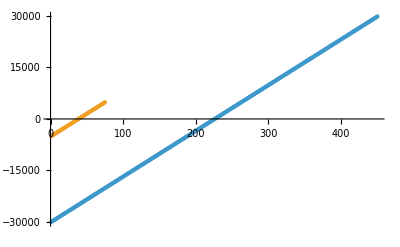

-30000.

29866.7

133.333

```mathematica
ListPlot[{xValues,yValues}]
xValues[[1]]
xValues[[-1]]
dx
```

```mathematica
prec=20
uOuterMin=1/10;(*The boundary of the inner subdomain*)
uOuterMax= 11/10;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=2;(*Number of outer subdomain*)
uOuterNodes=24;(*Number of points in each outer subdomains*)
uInnerNodes=12;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

20

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
{uValues1,uValues2,uValues3}=uValues;
Nx=nx;
```

#### Derivatives

```mathematica
Clear[d];
(*d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
dert=NDSolve`FiniteDifferenceDerivative[Derivative[1,0,0],{times,Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{4,"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{False,True,True}];
(*d[2,0]=NDSolve`FiniteDifferenceDerivative[Derivative[2,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,2]=NDSolve`FiniteDifferenceDerivative[Derivative[0,2],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,6]=NDSolve`FiniteDifferenceDerivative[Derivative[0,6],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[6,0]=NDSolve`FiniteDifferenceDerivative[Derivative[6,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
```

NDSolve`FiniteDifferenceDerivative::conw: There are insufficient points in dimension 1 to generate consistent finite different weights.

```mathematica
dt
```

0.219

```mathematica
15
```

15

#### Velocity Definition

```mathematica
(*ss=-10;*)
ClearAll[ss]
fy=Table[Obj[[ss,6,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
fx=Table[Obj[[ss,5,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
a3=Table[Obj[[ss,-2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
(*dya3=d[0,1][a3];
dxa3=d[1,0][a3];
uy=(fy-dya3)/a3;
ux=(fx-dxa3)/a3;*)
u0=(-a3)^(1/2);
ux=Table[(fx[[tt]]-d[1,0][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}] ;
uy=Table[(fy[[tt]]-d[0,1][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}] ;
Energy=ux^2+uy^2;
a=1;
b=ux[[1]]//Length;
c=1;
dd=uy[[1,1]]//Length;
x0=0;
y0=0;
ellipse[θ_,sigmax_,sigmay_]:={x0+sigmax Cos[θ],y0+sigmay Sin[θ]};
```

#### Inhomogeneous BBB Data Analysis

```mathematica
dt each
```

13.

```mathematica
50 3/4//N
```

37.5

```mathematica
Obj[[-1]]//Keys
```

{/data/125000/fields/Sd c=2,/data/125000/fields/S c=2,/data/125000/fields/A c=2,/data/125000/fields/Fx c=2,/data/125000/fields/Fx c=1,/data/125000/fields/Fy c=1,/data/125000/fields/Sd c=1,/data/125000/fields/Gd c=2,/data/125000/fields/Gd c=1,/data/125000/fields/Bd c=1,/data/125000/fields/Bd c=2,/data/125000/fields/Fy c=2,/data/125000/fields/A c=1,/data/125000/fields/S c=1}

Here I want to visualize the functions at a certain time and at a certain radius, hence in the XY plane.
I define the table SpecificFunction, where for each time (first entry, the “i” of the cycle), I just specify an object among the keys that we printed before (2nd entry), and I take a specific value of the radius. The GridSF is just the same but associates each value to the relative grid point, so that we will be able to print it.

```mathematica
(*Vorticity3D=Join[Table[(d[1,0][Obj[[ss,-3,;;,;;,r]]//Transpose]-d[0,1][Obj[[ss,4,;;,;;,r]]//Transpose]),{r,1,10}](*Table[(d[1,0][Obj[[ss,6,;;,;;,r]]//Transpose]-d[0,1][Obj[[ss,5,;;,;;,r]]//Transpose]),{r,1,10}]*)];*)
```

```mathematica
199/3//N
```

66.3333

```mathematica
Vorticity3D//Dimensions
```

{20,300,50}

```mathematica
ListContourPlot3D[Obj[[ss,4,;;,;;,;;]],BoxRatios->{2,12,2},ImageSize->Full,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(*ss=120;
ListContourPlot3D[Obj[[ss,-3]],BoxRatios->{2, 12, 2},ImageSize->Full,PlotLegends->Automatic]*)
```

-Graphics3D-

```mathematica
xi=Table[Obj[[ss,1,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
```

```mathematica
(*B=Table[Obj[[ss,ni,j,i,rii]],{ss,1,nt},{ni,{3,1}},{rii,1,Obj[[1,ni,1,1,;;]]//Length},{i,1,xValues//Length
},{j,1,yValues//Length}];
G=Table[Obj[[ss,ni,j,i,rii]],{ss,1,nt},{ni,{1,4}},{rii,1,Obj[[1,ni,1,1,;;]]//Length},{i,1,xValues//Length
},{j,1,yValues//Length}];*)
```

```mathematica
(*ss=-10;*)
ClearAll[ss]
fy=Table[Obj[[ss,6,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
fx=Table[Obj[[ss,5,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
a3=Table[Obj[[ss,-2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
(*dya3=d[0,1][a3];
dxa3=d[1,0][a3];
uy=(fy-dya3)/a3;
ux=(fx-dxa3)/a3;*)
u0=(-a3)^(1/2);
ux=Table[(fx[[tt]]-d[1,0][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}] ;
uy=Table[(fy[[tt]]-d[0,1][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}] ;
Energy=ux^2+uy^2;
a=1;
b=ux[[1]]//Length;
c=1;
dd=uy[[1,1]]//Length;
x0=0;
y0=0;
ellipse[θ_,sigmax_,sigmay_]:={x0+sigmax Cos[θ],y0+sigmay Sin[θ]};
```

```mathematica
Print["min ux:"<>ToString[Min[ux]]<>" N="<>ToString[nx]]
```

min ux:-0.0489506 N=100

```mathematica
midpoint=((ux[[1]]//Length)/2//Floor)-10;
ss=1;
ss1=(ux//Length)/2//Floor;
ss2=(ux//Length)-5;

Show[ListDensityPlot[(*((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)*)Join[((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,;;midpoint-1]],2],PlotRange->{All,All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],AspectRatio->ny/nx,GridLines->Automatic(*,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True*),ColorFunction->"ThermometerColors"(*,Contours->70*),ImageSize->Large,PlotRange->All](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
Show[ListDensityPlot[(*((d[1,0][uy[[ss1]]]-d[0,1][ux[[ss1]]])//Transpose)*)Join[((d[1,0][uy[[ss1]]]-d[0,1][ux[[ss1]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[ss1]]]-d[0,1][ux[[ss1]]])//Transpose)[[;;,;;midpoint-1]],2],PlotRange->{All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss1-1) dt each+init dt],AspectRatio->ny/nx,GridLines->Automatic(*,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True*),ColorFunction->"ThermometerColors"(*,Contours->70*),ImageSize->Large](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
Show[ListDensityPlot[(*((d[1,0][uy[[ss1]]]-d[0,1][ux[[ss1]]])//Transpose)*)Join[((d[1,0][uy[[ss2]]]-d[0,1][ux[[ss2]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[ss2]]]-d[0,1][ux[[ss2]]])//Transpose)[[;;,;;midpoint-1]],2],PlotRange->{All,All}, PlotLegends->True,
PlotLabel->"Vorticity t="<>ToString[(ss2-1) dt each+init dt],AspectRatio->ny/nx,GridLines->Automatic(*,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True*),ColorFunction->"ThermometerColors"(*,Contours->70*),ImageSize->Large](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

-Graphics-

Part::take: Cannot take positions 215 through -1 in -«1»+«1».

Part::take: Cannot take positions 1 through 214 in -«1»+«1».

Join::normal1: Expression (-«1»+«1»)^T⟦1;;All,215;;All⟧ at position 1 is expected to have nonatomic subexpression at level 2.

Part::take: Cannot take positions 215 through -1 in «1».

General::stop: Further output of Part::take will be suppressed during this calculation.

ListDensityPlot::arrayerr: Join[(-1. NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{450,PSFourier[«1»]},{{«451»},{«76»}},{True,True}][List]+NDSolve`FiniteDifferenceDerivativeFunction[Derivative[1,0],5,«1»,{{-30000.,«49»,«401»},{«1»}},{True,True}][List])^T⟦1;;All,215;;All⟧,(-1. NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,«1»,{{«451»},{«76»}},{True,True}][List]+«1»)^T⟦1;;All,1;;214⟧,2.] must be a valid array.

Show::gtype: ListDensityPlot is not a type of graphics.

Show[ListDensityPlot[Join[Transpose[(-NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],<>][List]+NDSolve`FiniteDifferenceDerivativeFunction[Derivative[1,0],<>][List])]⟦1;;All,215;;All⟧,Transpose[(-NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],<>][List]+NDSolve`FiniteDifferenceDerivativeFunction[Derivative[1,0],<>][List])]⟦1;;All,1;;214⟧,2],PlotRange→{All,All},PlotLegends→True,PlotLabel→vorticity t=933511.,AspectRatio→1/6,GridLines→Automatic,ColorFunction→ThermometerColors,ImageSize→Large]]

Part::partw: Part -4 of {{{0.0951792,0.0975353,0.100018,0.102652,0.105469,0.108506,0.111795,0.115367,0.119236,0.123399,0.127833,0.132487,«27»,0.0972655,0.096248,0.0955061,0.0949422,0.0944627,0.0939832,0.0934337,0.0927618,0.0919353,0.0909424,0.0897904,«25»},«49»,«400»}} does not exist.

Part::partw: Part -4 of {{{0.270032,0.266644,0.262462,0.257503,0.251782,0.245308,0.238081,0.230097,0.221345,0.211811,0.201483,0.19036,«27»,0.0827451,0.0880117,0.0930772,0.0980138,0.102904,0.107835,0.112889,0.118144,0.123665,0.129504,0.135701,«25»},{«1»},«47»,{«1»},«400»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 215 through -1 in -«1»+«1».

Part::take: Cannot take positions 1 through 214 in -«1»+«1».

Join::normal1: Expression (-«1»+«1»)^T⟦1;;All,215;;All⟧ at position 1 is expected to have nonatomic subexpression at level 2.

Part::take: Cannot take positions 215 through -1 in «1».

General::stop: Further output of Part::take will be suppressed during this calculation.

ListDensityPlot::arrayerr: Join[(«1»)^T⟦1;;All,215;;All⟧,(-1. NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{450,PSFourier[«1»]},{{«451»},{«76»}},{True,True}][{«1»}⟦-4⟧]+NDSolve`FiniteDifferenceDerivativeFunction[Derivative[1,0],5,«1»,{{«1»},{«1»}},{True,True}][«1»])^T⟦1;;All,1;;214⟧,2.] must be a valid array.

Show::gtype: ListDensityPlot is not a type of graphics.

```mathematica
TimesToPlot={6,100,200,300,400,500,636}
```

{6,100,200,300,400,500,636}

```mathematica
Table[ListDensityPlot[((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)(*Join[((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,;;midpoint-1]],2]*),PlotRange->{All,All,All}, PlotLegends->True,
PlotLabel->"vorticity Lt="<>ToString[((tt-1) dt each+init dt)/Lx],AspectRatio->ny/nx,GridLines->Automatic(*,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True*),ColorFunction->"ThermometerColors",ColorFunctionScaling->True,PlotLegends->BarLegend[{"ThermometerColors",{-10^-5,10^-5}}](*,Contours->70*),ImageSize->Large],{tt,TimesToPlot}]
```

Table::iterb: Iterator {tt,TimesToPlot} does not have appropriate bounds.

Table[ListDensityPlot[Transpose[(d[1,0][uy⟦tt⟧]-d[0,1][ux⟦tt⟧])],PlotRange→{All,All,All},PlotLegends→True,PlotLabel→vorticity Lt=<>ToString[((tt-1) dt each+init dt)/Lx],AspectRatio→ny/nx,GridLines→Automatic,ColorFunction→ThermometerColors,ColorFunctionScaling→True,PlotLegends→,ImageSize→Large],{tt,TimesToPlot}]

```mathematica
Export["/home/giulio/Pictures/vorticity_unsourced_N400_L1500_0d7ui12_1u12_q10_L1500_t"<>ToString[(ss-1) dt each+init dt]<>"jpeg",%]
```

```mathematica
"/home/giulio/Pictures/vorticity_unsourced_N400_L1500_0d7ui12_1u12_q10_L1500_t1965.jpeg"
```

/home/giulio/Pictures/vorticity_unsourced_N400_L1500_0d7ui12_1u12_q10_L1500_t1965.jpeg

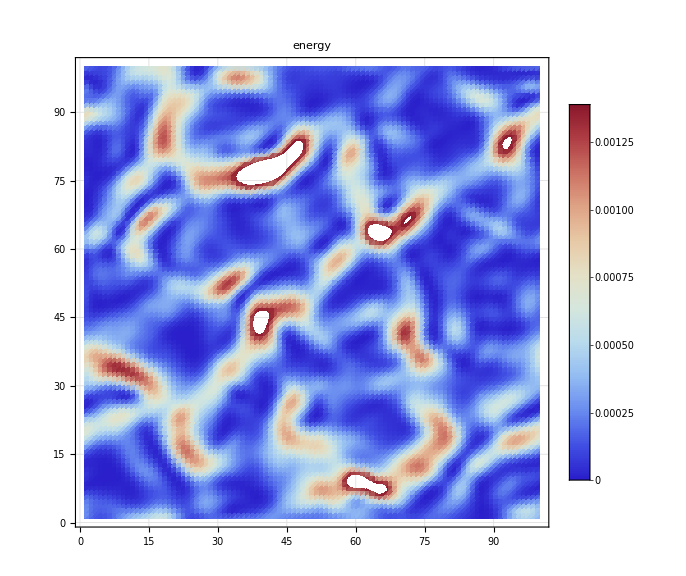

```mathematica
Show[ListDensityPlot[(Energy[[(-1)]]//Transpose),PlotRange->{All,All}, PlotLegends->True,
PlotLabel->"energy"(* t="<>ToString[(268-1) dt each+init dt]*),AspectRatio->ny/nx,GridLines->Automatic,ImageSize->Large,ColorFunction->"ThermometerColors"]]
```

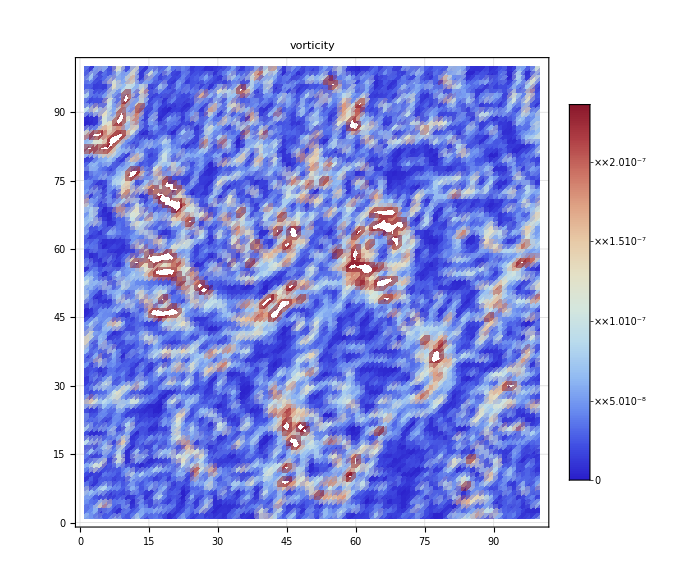

-Graphics-

```mathematica
times[[26]]
```

2600.

```mathematica
ss=-1;
VorticityTranslated=((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)(*Join[((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,;;midpoint-1]],2]*);
VorticityToPlot=Flatten[Table[{xValues[[i]],yValues[[j]],VorticityTranslated[[j,i]]},{i,1,nx},{j,1,ny}],1];
```

```mathematica
ListDensityPlot[VorticityToPlot, PlotLegends->True,
PlotLabel->"ω at t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->ny/nx,(*ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,*)ColorFunction->"ThermometerColors",(*PlotRange->{All,All,All},*)GridLines->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/junk_vorticity_field_"<>FileName<>"_t"<>ToString[(ss-1) dt each+init dt]<>"jpeg",%]
```

/home/giulio/Pictures/junk_vorticity_field_NBB_gaussian_Lx10000_Ly10000_3d3iu10_6d6u010_Nx75_Ny75_u0d3_tzero5000_tau200_A1d5_s0d5_dt0d1_t2200.jpeg

```mathematica
density=ListDensityPlot[VorticityToPlot,PlotRange->All,ColorFunction->"ThermometerColors",PlotLegends->True,PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Large,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])];

stream=ListStreamPlot[Table[{{xValues[[i]],yValues[[j]]},{ux[[ss,i,j]],uy[[ss,i,j]]}},{i,a,b},{j,c,dd}](*Join[Table[{{xValues[[i+1]],yValues[[j]]},{ux[[ss,i+midpoint,j]],uy[[ss,i+midpoint,j]]}},{i,0,midpoint},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[ss,i+1,j]],uy[[ss,i+1,j]]}},{i,0,midpoint},{j,c,dd}]]*),StreamPoints->Fine,StreamColorFunction->False,StreamStyle->{Arrowheads[0.007],Thick[0.05],White},PlotLegends->None,ImageSize->Large,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),LabelStyle->Directive[FontSize->16],BaseStyle->{FontSize->16},FrameLabel->{"x","y"}];

Show[density,stream,PlotRange->{All,All},ImageSize->Full]
```

ListDensityPlot::arrayerr: VorticityToPlot must be a valid array.

$Aborted

Show::gcomb: Could not combine the graphics objects in Show[ListDensityPlot[VorticityToPlot,PlotRange→All,ColorFunction→ThermometerColors,PlotLegends→True,PlotLabel→vorticity t=1130.,ImageSize→Large,AspectRatio→1.],stream,PlotRange→{All,All},ImageSize→Full].

Show[ListDensityPlot[VorticityToPlot,PlotRange→All,ColorFunction→ThermometerColors,PlotLegends→True,PlotLabel→vorticity t=1130.,ImageSize→Large,AspectRatio→1.],stream,PlotRange→{All,All},ImageSize→Full]

```mathematica
Export["/home/giulio/Pictures/velocity_vorticity_unsourced_N400_L1500_0d7ui12_1u12_q10_L1500_t"<>ToString[(ss-1) dt each+init dt]<>"jpeg",%]
```

/home/giulio/Pictures/velocity_vorticity_unsourced_N400_L1500_0d7ui12_1u12_q10_L1500_t1965.jpeg

```mathematica
(*Export["/home/giulio/Pictures/vorticity_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg",ListDensityPlot[VorticityToPlot,PlotRange->{All,All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),ColorFunction->"ThermometerColors"]]*)
```

/home/giulio/Pictures/vorticity_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg

```mathematica
100 3/2
```

150

```mathematica
10000 3/2
60000 3/2
```

15000

90000

```mathematica
tau=
```

```mathematica
Timeinterp[tt_]:=Piecewise[{{Cos[(Pi(tt-t1))/(2 ddt)]Ft1+Sin[(Pi(tt-t1))/(2 ddt)]Ft2,tt>=3dt&&tt<4dt},{Cos[(Pi(tt-t2))/(2 ddt)]Ft2+Sin[(Pi(tt-t2))/(2 ddt)]Ft3,tt>=4dt&&tt<5dt}}];
Timeinterp2[tt_]:=Piecewise[{{Cos[(Pi(tt-t1))/(2 ddt)]Ft1+Sin[(Pi(tt-t1))/(2 ddt)]Ft2,tt>=3dt&&tt<4dt},{Ft2,tt>=4dt&&tt<5dt},{Cos[(Pi(tt-t3))/(2 ddt)]Ft2+Sin[(Pi(tt-t3))/(2 ddt)]Ft3,tt>=5dt&&tt<6dt}}]
```

```mathematica
Timeinterp2[tt]/.t3->t2+ddt/.t2->t1+ddt/.t1->3ddt/.ddt->dt/.Ft1->1/.Ft2->2/.Ft3->5
```

Piecewise[{{Cos[78.5398 (-0.06+tt)]+2 Sin[78.5398 (-0.06+tt)], tt≥0.06&&tt<0.08}, {2, tt≥0.08&&tt<0.1}, {2 Cos[78.5398 (-0.1+tt)]+5 Sin[78.5398 (-0.1+tt)], tt≥0.1&&tt<0.12}, {0, True}}]

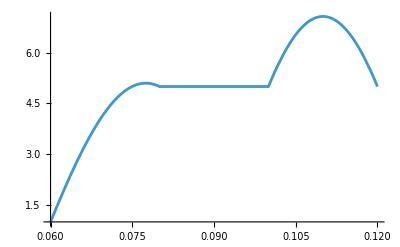

```mathematica
Plot[{Timeinterp2[tt]/.t3->t2+ddt/.t2->t1+ddt/.t1->3ddt/.ddt->dt/.Ft1->1/.Ft2->5/.Ft3->5},{tt,3dt,6dt}]
```

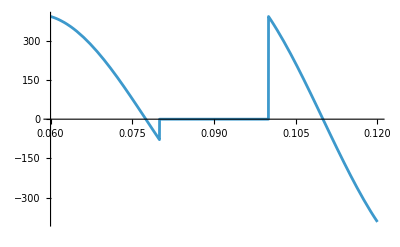

```mathematica
Plot[D[Timeinterp2[ttt]/.t3->t2+ddt/.t2->t1+ddt/.t1->3ddt/.ddt->dt/.Ft1->1/.Ft2->5/.Ft3->5,ttt]/.ttt->tt,{tt,3dt,6dt}]
```

```mathematica
ux[[1,1]]
```

{0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955,0.275955}

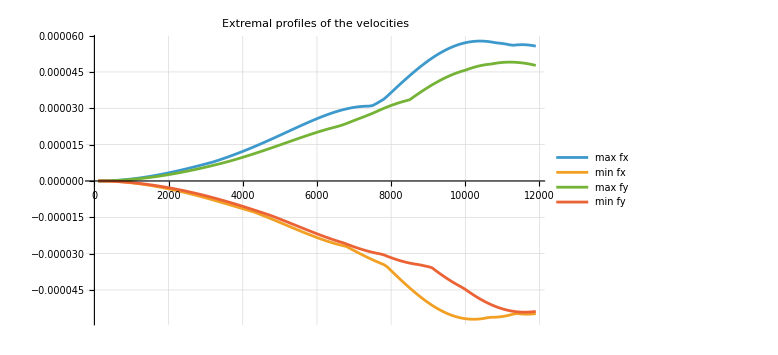

```mathematica
ListPlot[{{times,Map[Max,ux,2]}//Transpose,{times,Map[Min,ux,2]}//Transpose,{times,Map[Max,uy,2]}//Transpose,{times,Map[Min,uy,2]}//Transpose},ImageSize->Large(*,PlotRange->All*),PlotLegends->{"max fx","min fx","max fy","min fy"},Joined->True,GridLines->Automatic(*,GridLines->{{90000,times[[65]]}, {}},GridLinesStyle->Directive[Black]*),PlotRange->All,PlotLabel->"Extremal profiles of the velocities "(*"Lx=10000 Ly=20000 Nx="<>ToString[nx]<>" Ny= "<>ToString[ny]*)]
```

```mathematica
Export["/home/giulio/Pictures/velocities_extrema"<>FileName<>".jpeg",%]
```

/home/giulio/Pictures/velocities_extremaNBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219.jpeg

```mathematica
Min[ux]
Max[ux]
nx
```

-0.317689

0.374779

50

```mathematica
Min[ux]
Max[ux]
nx
```

-0.33724

0.38505

75

```mathematica
Min[ux]
Max[ux]
nx
```

-0.351624

0.392948

100

```mathematica
Export["/home/giulio/Pictures/velocities_extrema_N"<>ToString[nx]<>"_Lx10000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg",%]
```

/home/giulio/Pictures/velocities_extrema_N50_Lx10000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg

```mathematica
(*Plot[S0[tt,50000,20000,0.8,0,0,0.5,0,0,0.5],{tt,0,1/4 10^6},PlotRange->All,GridLines->Automatic]*)
```

```mathematica
ux//Length
```

101

```mathematica
Table[{{xValues[[i]],yValues[[j]]},{ux[[1,i,j]],uy[[1,i,j]]}},{i,1,nx
},{j,1,ny}]//Dimensions
```

{600,50,2,2}

```mathematica
times[[60]]
```

3900.

```mathematica
..
```

```mathematica
ux//Dimensions
```

{1,300,100}

```mathematica
Min[ux]
```

-0.179888

```mathematica
Export["/home/giulio/Pictures/velocities_vf_"<>FileName<>"t_"<>ToString[t dt each+init dt]<>"jpeg",%]
```

/home/giulio/Pictures/velocities_vf_NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec4t_599622.jpeg

```mathematica
Export["/home/giulio/Pictures/vorticit&velocity_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg",Show[density,stream,PlotRange->All]]
```

/home/giulio/Pictures/vorticit&velocity_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg

```mathematica
10^6/1132/24//N
10^6/1047/24//N
```

36.808

39.7962

```mathematica
6.6/20 0.8//N
```

0.264

```mathematica
xValues[[20]]
```

-1200.

```mathematica
ux//Length
```

24

```mathematica
dy
```

200.

```mathematica
ux//Dimensions
```

{56,50,100}

#### Plotting Stramlines and videos

```mathematica
90 each
```

5400000

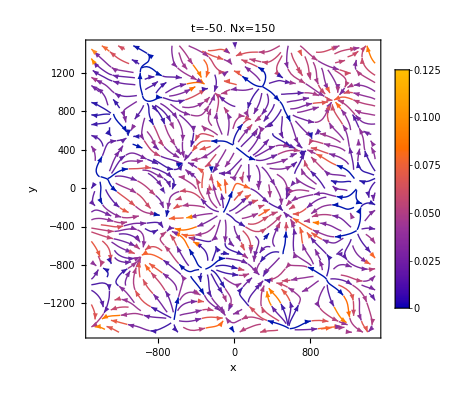

```mathematica
t=-1;
a=1;
b=ux[[1]]//Length;
c=1;
dd=uy[[1,1]]//Length;
midpoint=(ux[[1]]//Length)/2//Floor;
Show[(*Table[{{xValues[[i]],yValues[[j]]},{ux[[t,i,j]],uy[[t,i,j]]}},{i,1,nx
},{j,1,ny}]*)Join[Table[{{xValues[[i+1]],yValues[[j]]},{ux[[t,i+midpoint,j]],uy[[t,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[t,i+1,j]],uy[[t,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt]<>" Nx="<>ToString[nx](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

```mathematica
50 each
```

3000000

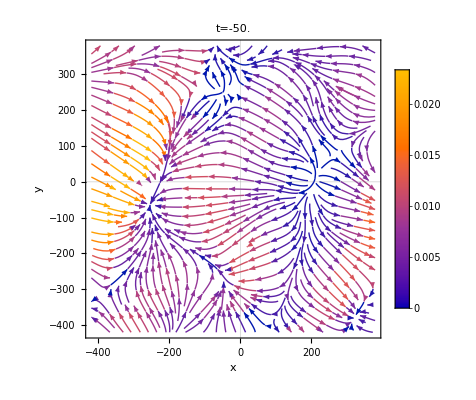

```mathematica
t=-1;
a=1(ux[[1]]//Length)/2-20//Floor;
b=(ux[[1]]//Length)/2+20//Floor;
c=(ux[[1,1]]//Length)/2-20//Floor;
dd=(ux[[1,1]]//Length)/2+20//Floor;
Show[Table[{{xValues[[i]],yValues[[j]]},{ux[[t,i,j]],uy[[t,i,j]]}},{i,a,b
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)StreamPoints->Fine,PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.008],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

```mathematica
Export["/home/giulio/Pictures/zoom_velocity_vector_field_Nx250_Ny50_Lx50000_Ly10000_u0d2_s0d5_t050000_tau20000_A0d8_t_1.2408_10e6.jpeg",%]
```

/home/giulio/Pictures/zoom_velocity_vector_field_Nx250_Ny50_Lx50000_Ly10000_u0d2_s0d5_t050000_tau20000_A0d8_t_1.2408_10e6.jpeg

```mathematica
600000/1221/24//N
```

20.475

```mathematica
6 2
```

12

```mathematica
3 3
```

9

```mathematica
(*Export["/home/giulio/Pictures/velocty_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8_spatialzoom.jpeg",Show[Table[{{xValues[[i]],yValues[[j]]},{ux[[t,i,j]],uy[[t,i,j]]}},{i,a,b
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)StreamPoints->100000,PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.008],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]]]*)
```

/home/giulio/Pictures/velocty_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8_spatialzoom.jpeg

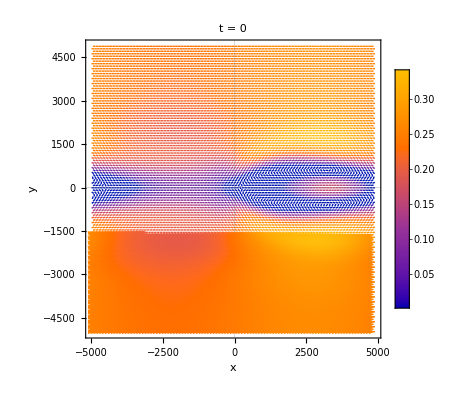

```mathematica
t=-1;
(*xLineInd=150;*)
Table[{{xValues[[i]],yValues[[j]]},{ux[[t,i,j]],1uy[[t,i,j]]}},{i,1,xValues//Length
},{j,1,yValues//Length}]//ListVectorPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t = 0"(*<>ToString[t dt each+init dt]*),VectorStyle->Arrowheads[0.008],VectorPoints->100 ,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),ImageSize->Large,LabelStyle->Directive[FontSize->20],BaseStyle->{FontSize->16},FrameLabel->{"x","y"},ColorFunction->"ColorBlindTones"]&
```

```mathematica
ux//Length
```

242

```mathematica
frames=Table[Join[Table[{{xValues[[i+1]],yValues[[j]]},{ux[[tt,i+midpoint,j]],uy[[tt,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[tt,i+1,j]],uy[[tt,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]](*Table[{{xValues[[i]],yValues[[j]]},{ux[[tt,i,j]],uy[[tt,i,j]]}},{i,a,b
},{j,c,dd}]*)//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[tt dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&,{tt,1,ux//Length}];//AbsoluteTiming
```

{53.1581,Null}

```mathematica
Export["/home/giulio/Videos/velocity_stream_"<>FileName<>".mp4",frames,"DisplayDurations"->20.0];//AbsoluteTiming
```

{27.2102,Null}

```mathematica
frames=Table[Show[ListDensityPlot[((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)(*Join[((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)[[;;,;;midpoint-1]],2]*),ColorFunction->"ThermometerColors"(*,ColorFunctionScaling->True,PlotLegends->BarLegend[{"ThermometerColors",{-10^-5,10^-5}}]*),
PlotLabel->"vorticity t="<>ToString[(tt-1) dt each+init dt],ImageSize->Large,AspectRatio->ny/nx,GridLines->Automatic](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)],{tt,1,ux//Length}];//AbsoluteTiming
```

{25.654,Null}

```mathematica
Export["/home/giulio/Videos/vorticity_field_"<>FileName<>".mp4",frames,"DisplayDurations"->100.0];//AbsoluteTiming
```

{14.4132,Null}

```mathematica
frames=Table[Show[ListDensityPlot[(*((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)*)(*Join[((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)[[;;,;;midpoint-1]],2]*)Energy[[tt]]//Transpose(*,PlotRange->{0,  Max[Energy]}*),ColorFunction->"ThermometerColors",ColorFunctionScaling->True,PlotLegends->BarLegend[{"ThermometerColors",{0, Max[Energy]}}],
PlotLabel->"energy t="<>ToString[(tt-1) dt each+init dt],ImageSize->Large,AspectRatio->ny/nx,GridLines->Automatic](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)],{tt,nt(*ux//Length*)}];//AbsoluteTiming
```

{36.4806,Null}

```mathematica
Export["/home/giulio/Videos/Energy_field_"<>FileName<>".mp4",frames,"DisplayDurations"->120.0];//AbsoluteTiming
```

{21.2567,Null}

```mathematica
6.6/24 0.4//N
```

0.11

```mathematica
ListPlot[Table[Cos[2 Pi/Lx x 15],{x,-Lx/2,Lx/2,Lx/200}],Joined->True,PlotMarkers->{"o"},PlotStyle->Dashed,ImageSize->Large]
```

-Graphics-

```mathematica
6.6/24 0.4
```

0.11

#### Wake analysis

```mathematica
Nx=nx
```

450

```mathematica
IntervalFinder[uuy_,pk1_,pk2_,xindex_]:=Module[{uy=uuy,peak1Value=pk1,peak2Value=pk2,xind=xindex,timeinitial,timefinal},
timeinitial=FirstPosition[uuy[[;;,xind,40]],n_ /;Abs[ n]>peak1Value][[1]];
timefinal=FirstPosition[uuy[[;;,xind,1]],n_ /;Abs[ n]>peak2Value][[1]];
{timeinitial,timefinal}
];
```

```mathematica
ProperAverage[uux_,uuy_,pk1_,pk2_]:=Module[{ux=uux,uy=uuy,peak1Value=pk1,peak2Value=pk2},
TimeIntervals=Table[IntervalFinder[uy,pk1,pk2,xx],{xx,Nx}];
Result=Table[Mean[ux[[TimeIntervals[[xx]][[1]];;TimeIntervals[[xx]][[2]],xx,;;]]],{xx,Nx}];
{Result,Table[{times[[TimeIntervals[[xx]][[1]]]],times[[TimeIntervals[[xx]][[2]]]]},{xx,Nx}]}
];
```

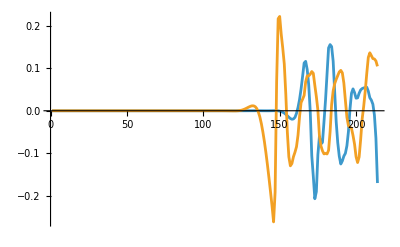

```mathematica
ListPlot[{uy[[;;,300,1]],uy[[;;,100,1]]},Joined->True,PlotRange->All]
```

```mathematica
times[[14]]
times[[80]]
```

61320.

350400.

```mathematica
TimeAverageIntervals=ProperAverage[ux,uy,0.0005,0.04][[2]];
```

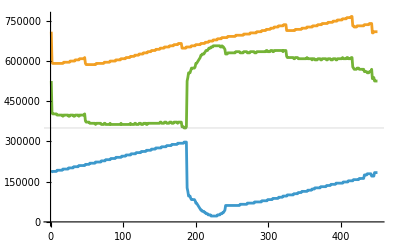

```mathematica
Show[ListPlot[{TimeAverageIntervals[[;;,1]],TimeAverageIntervals[[;;,2]],TimeAverageIntervals[[;;,2]]-TimeAverageIntervals[[;;,1]]},Joined->True,PlotRange->All,ImageSize->Full,GridLines->{{},{times[[80]]}}](*,Plot[FitTimeAverageIntervals[x],{x,600,1200},PlotStyle->{Dashed,Purple}]*)]
```

```mathematica
times[[28]]
```

61320.

```mathematica
60000/0.25
```

240000.

```mathematica
times[[55]]
```

240900.

{aa→4.95532,bb→32200.1}

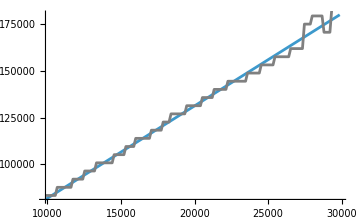

```mathematica
FitTimeAverageIntervals=NonlinearModelFit[Transpose[{Range[180,320],TimeAverageIntervals[[180;;320,2]]}],aa x+bb,{aa,bb},x];
FitTimeAverageIntervalsValues=NonlinearModelFit[Transpose[{xValues[[300;;450]],TimeAverageIntervals[[300;;450,1]]}],aa x+bb,{aa,bb},x];
(*FitTimeAverageIntervalsValues2=NonlinearModelFit[Transpose[{TimeAverageIntervals[[180;;320,2]],xValues[[180;;320]]}],aa x+bb,{aa,bb},x];*)
FitTimeAverageIntervalsValues["BestFitParameters"]
(*FitTimeAverageIntervalsValues2["BestFitParameters"]*)
Show[Plot[{FitTimeAverageIntervalsValues[x]},{x,xValues[[300]],xValues[[450]]}],ListPlot[Transpose[{xValues[[300;;450]],TimeAverageIntervals[[300;;450,1]]}],Joined->True,PlotRange->All,ImageSize->Medium,GridLines->{{},{times[[80]]}},PlotStyle->Gray]]
```

```mathematica
times[[225]]
```

492750.

```mathematica
xValues[[300;;450]]//Length
FitTimeAverageIntervalsValues//Length
```

151

1

```mathematica
(*FitTimeAverageIntervalsValuesFinal=NonlinearModelFit[Transpose[{TimeAverageIntervals[[300;;400,2]],xValues[[300;;400]]}],aa x+bb,{aa,bb},x]["BestFitParameters"]*)
```

```mathematica
tInitialIndex1=28;
speed=0.2;
stxIndEnd=243;
tInitialIndex2=tInitialIndex1+((xx-stxIndEnd)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Floor)/.xx->(xValues//Length)
tIndexIntervalFixed=60000/speed/dt/each//Floor;
```

91

```mathematica
60000/0.2/dt/each//Floor
```

136

```mathematica
ProperAverage3[uux_,uuy_]:=Module[{ux=uux,uy=uuy(*,peak1Value=pk1,peak2Value=pk2*)},
Result=Join[Table[Mean[ux[[tInitialIndex2+((xx-1)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Ceiling);;tInitialIndex2+((xx-1)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Ceiling)+tIndexIntervalFixed,xx,;;]]],{xx,1,stxIndEnd}],Table[Mean[ux[[tInitialIndex1+((xx-stxIndEnd)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Ceiling);;tInitialIndex1+((xx-stxIndEnd)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Ceiling)+tIndexIntervalFixed,xx,;;]]],{xx,stxIndEnd,Nx}]];
TimeIntervals=Join[Table[{tInitialIndex2+((xx-1)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Floor),tInitialIndex2+((xx-1)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Floor)+tIndexIntervalFixed},{xx,1,stxIndEnd}],Table[{tInitialIndex1+((xx-stxIndEnd)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Floor),tInitialIndex1+((xx-stxIndEnd)(xValues[[-1]]-xValues[[-2]])/speed/(times[[-1]]-times[[-2]])//Floor)+tIndexIntervalFixed},{xx,stxIndEnd,Nx}]];
{Result,Table[{times[[TimeIntervals[[xx]][[1]]]],times[[TimeIntervals[[xx]][[2]]]]},{xx,Nx}]}
]
```

```mathematica
meanUxAll=ProperAverage3[ux,uy][[1]];
```

```mathematica
ListContourPlot[meanUxAll//Transpose,AspectRatio->ny/nx,ImageSize->Large,PlotLegends->Automatic,GridLines->Automatic]
```

-Graphics-

```mathematica
times[[-1]]
```

937320.

```mathematica
TimeAverageIntervals=ProperAverage3[ux,uy][[2]];
```

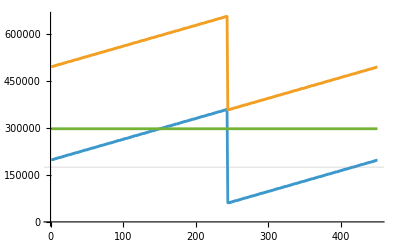

```mathematica
Show[ListPlot[{TimeAverageIntervals[[;;,1]],TimeAverageIntervals[[;;,2]],TimeAverageIntervals[[;;,2]]-TimeAverageIntervals[[;;,1]]},Joined->True,PlotRange->All,ImageSize->Full,GridLines->{{},{times[[80]]}}](*,Plot[FitTimeAverageIntervals[x],{x,600,1200},PlotStyle->{Dashed,Purple}]*)]
```

```mathematica
times[[60]]
```

350400.

```mathematica
60000/0.3
```

200000.

1200.78

1434.9

1420.77

1476.31

1414.39

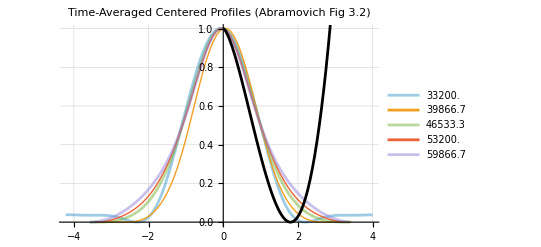

```mathematica
(*1. Time-average the velocity to remove vortex'noise'*)
(*tRange=70;;-1; 
meanUxAll=Mean[ux[[tRange,;;,;;]]];*)
getCleanNormalizedData[xIdx_]:=Module[{Uinf,localUx,u1Profile,u1m,yPeak,yc,normalizedY},
(*Uinf=ux[[1,1,1]];*)
(*Global U_inf*)
localUx=meanUxAll[[xIdx,;;]];
Uinf=Max[localUx];
u1Profile=Uinf-localUx;
(*Find the peak position to center the wake*)
u1m=Max[u1Profile];
yPeak=yValues[[First@Ordering[localUx,1]]];
u1Interp=Interpolation[Transpose[{yValues,u1Profile}]];
(*Find yc (distance from peak where deficit is half)*)(*Check right side*)yc=y/. FindRoot[u1Interp[yPeak+y]==0.5*u1m,{y,Lx/100}]//Quiet;
Print [yc];
(*Return centered and normalized data*)
Table[{(y-yPeak)/yc,u1Interp[y]/u1m},{y,Min[yValues],Max[yValues],dy}]]

(*Plotting multiple x-slices to check for collapse*)
xSlices={250,300,350,400,450};
Show[ListLinePlot[Table[getCleanNormalizedData[x],{x,xSlices}],PlotRange->All,PlotStyle->{Opacity[0.5],Thick},GridLines->Automatic,PlotLabel->"Time-Averaged Centered Profiles (Abramovich Fig 3.2)",PlotLegends->Table[-xValues[[1]]+xValues[[x]],{x,xSlices}]],Plot[(1-(y/1.8)^(3/2))^2,{y,0,3},PlotStyle->Black,PlotRange->All]]
```

```mathematica
ny
```

75

1434.9

1434.9

1200.78

1434.9

1420.77

1476.31

1414.39

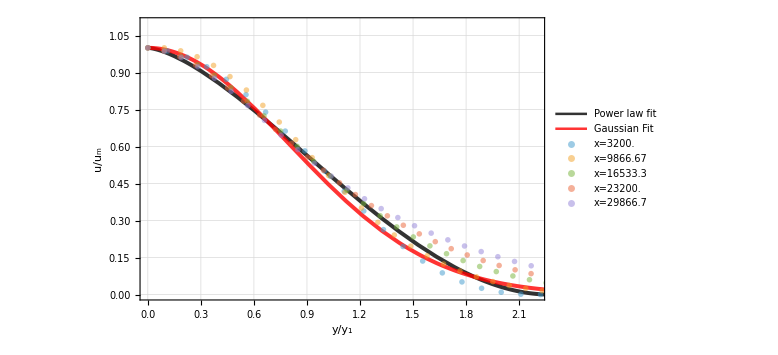

```mathematica
SelfSimilarityFit1=NonlinearModelFit[getCleanNormalizedData[300][[40;;60]],(1-(yy/CC)^(3/2))^2,{{CC,1.8}},yy];
SelfSimilarityFit2=NonlinearModelFit[getCleanNormalizedData[300],Exp[-CC yy^2],{{CC,1.8}},yy];
(*Print[SelfSimilarityFit["BestFitParameters"]];*)
Show[Plot[{(1-(y/CC)^(3/2))^2/.SelfSimilarityFit1["BestFitParameters"],Exp[-CC y^2]/.SelfSimilarityFit2["BestFitParameters"]},{y,0,5},PlotStyle->{{Black,Opacity[0.8],Thickness[0.005]},{Red,Opacity[0.8],Thickness[0.005]}},PlotLegends->Placed[LineLegend[{"Power law fit","Gaussian Fit"},LegendFunction->Framed],{Left,Bottom}],PlotRange->{{0,2.2},{0,1.1}},LabelStyle->{FontSize->20},ImageSize->Large,Frame->{True,True,True,True},FrameLabel->{y/Subscript[y, c], u/Subscript[u, m]},GridLines->Automatic],ListPlot[Table[getCleanNormalizedData[x],{x,xSlices}],PlotStyle->{Table[Opacity[0.5],{i,xSlices}]},GridLines->Automatic,PlotLegends->Placed[LineLegend[Table["x="<>ToString[xValues[[x]]//N],{x,xSlices}],LegendFunction->Framed],{Right,Top}],PlotRange->{{0,2},{0,1}},ImageSize->Large,PlotMarkers->{"OpenMarkers"},AxesLabel->{y/Subscript[y, c], u/Subscript[u, m]},LabelStyle->{FontSize->20}]]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_selfsimilarity"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_selfsimilarityNBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219.pdf

1200.78

1434.9

1420.77

1476.31

1414.39

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

1200.78

1434.9

1420.77

1476.31

1414.39

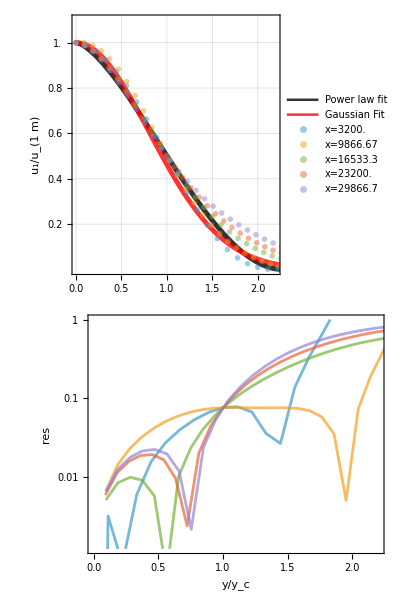

```mathematica
gaussParams=SelfSimilarityFit2["BestFitParameters"];
gaussFunc[y_]:=Exp[-CC y^2]/. gaussParams;
powLawFunc[y_]:=(1-(y/CC)^(3/2))^2/. SelfSimilarityFit1["BestFitParameters"];

allDataSlices=Table[getCleanNormalizedData[x],{x,xSlices}];

(*Calculate residuals for every slice*)
allResiduals=Table[Table[{pt[[1]],Abs[(pt[[2]]-gaussFunc[pt[[1]]])/pt[[2]]]},{pt,slice}],{slice,allDataSlices}];
commonWidth=700;
commonPaddingLeft=120;
sharedXRange={0,2.2};

(*Top Plot*)
topPlot=Show[Plot[{(1-(y/CC)^(3/2))^2/. SelfSimilarityFit1["BestFitParameters"],Exp[-CC y^2]/. SelfSimilarityFit2["BestFitParameters"]},{y,0,5},PlotStyle->{{Black,Opacity[0.8],Thickness[0.005]},{Red,Opacity[0.8],Thickness[0.005]}},PlotLegends->Placed[LineLegend[{"Power law fit","Gaussian Fit"},LegendFunction->Framed],{Left,Bottom}],PlotRange->{sharedXRange,{0,1.1}},ImageSize->{commonWidth,400}],ListPlot[Table[getCleanNormalizedData[x],{x,xSlices}],PlotStyle->Table[Opacity[0.5],{Length[xSlices]}],PlotMarkers->{"OpenMarkers",8},PlotLegends->Placed[LineLegend[Table["x="<>ToString[xValues[[x]]//N],{x,xSlices}],LegendFunction->Framed],{Right,Top}]],(*CRITICAL SETTINGS FOR ALIGNMENT*)PlotRange->{sharedXRange,{0,1.1}},ImageSize->{commonWidth,400},AspectRatio->Full,(*Forces the plot to fill the 400px height*)ImagePadding->{{commonPaddingLeft,20},{0,30}},(*Bottom padding must be 0*)Frame->True,LabelStyle->{FontSize->20},GridLines->Automatic,(*Use None for bottom FrameTicks to avoid the'0.0' being cut in half*)(*Inside topPlot*)FrameTicks->{{(*Left Axis:Manually define ticks from 0.2 up to 1.0 to avoid the bottom 0.0*)Table[{tick,tick},{tick,0.2,1.0,0.2}],Automatic},{Automatic,None} (*Bottom,Top*)},FrameLabel->{None,Style[Row[{"u_1","/","u_(1  m)"}],20]}];

(*Bottom Plot*)
bottomPlot=ListLogPlot[allResiduals,Joined->True,PlotStyle->Table[Directive[Opacity[0.7]],{Length[xSlices]}],Frame->True,FrameLabel->{Style[Row[{y,"/","y_c"}],20],Style["res",20]},ImageSize->{commonWidth,180},AspectRatio->Full,ImagePadding->{{commonPaddingLeft,20},{60,0}},(*Top padding must be 0*)PlotRange->{sharedXRange,{0.000,1}},(*Log scale cannot start at 0*)GridLines->{Automatic,Automatic},LabelStyle->{FontSize->18},FrameTicks->{{{0.001,0.01,0.10},None},(*Cleaned Log Ticks*){Automatic,Automatic}}](*Bottom Plot:Change to ListLogLinearPlot to match Top Plot's X-axis scaling*);

(*Assemble with 0 spacing*)
Column[{topPlot,bottomPlot},Spacings->0]
```

```mathematica
{{}}
```

```mathematica
getCleanNormalizedu1m[xIdx_]:=Module[{Uinf,localUx,u1Profile,u1m,yPeak,yc,normalizedY},
Uinf=ux[[1,1,1]];
(*Global U_inf*)
localUx=meanUxAll[[xIdx,;;]];
u1Profile=Abs[Uinf-localUx];
(*Find the peak position to center the wake*)
u1m=Max[u1Profile]]
```

```mathematica
nx
```

450

```mathematica
xstart=400;
xend=150;
```

```mathematica
(*1. Combine your data into a single list of {x,u1m}*)deficitData=Join[Table[{xValues[[xind]],getCleanNormalizedu1m[xind]},{xind,xstart,nx}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[nx]],getCleanNormalizedu1m[xind]},{xind,1,xend}]];

(*2. Perform the Nonlinear Fit*)
(*We use the form:a*(x-x0)^(-1/2)+offset*)
nlmDeficit=NonlinearModelFit[deficitData,aa*(x-x00)^(-1/2)+cc,{{aa,20},{cc},{x00,xValues[[xstart-1]]}},x(*,AccuracyGoal->20*)];

(*3. Extract the physical parameters*)
params=nlmDeficit["BestFitParameters"]
```

{aa→21.9363,cc→-0.0172937,x00→16696.3}

```mathematica
xValues[[xstart-1]]
```

23066.7

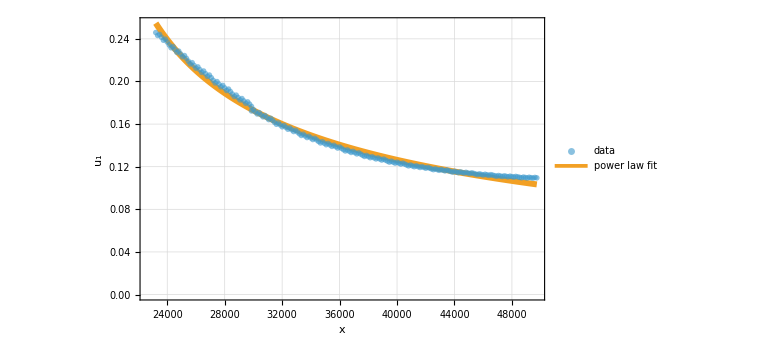

```mathematica
Show[ListPlot[{Join[Table[{xValues[[xind]](*(xValues[[xind]])*),getCleanNormalizedu1m[xind]},{xind,xstart,nx}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[nx]],getCleanNormalizedu1m[xind]},{xind,1,xend}](*,Table[getCleanNormalizedu1m[xind],{xind,1,220}]*)],Join[Table[{xValues[[xind]](*(xValues[[xind]])*),aa*(xValues[[xind]]-x00(*xValues[[610]]*))^(-1/2)+cc/.nlmDeficit["BestFitParameters"](*(((xind-620)/0.05)^(-1/2))-0.03*)},{xind,xstart,nx}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[nx]](*(xValues[[xind]])*),aa*(xValues[[xind]]-xValues[[1]]+xValues[[nx]]-x00(*xValues[[300]]*))^(-1/2)+cc/.nlmDeficit["BestFitParameters"](*(((xind-620)/0.05)^(-1/2))-0.03*)},{xind,1,xend}]]},ImageSize->Large,PlotStyle->{{Opacity[0.6]},{Opacity[1],Thickness[0.0075]}},PlotMarkers->{{"OpenMarkers",4},None},Joined->{False,True},PlotRange->{All,All(*{0,0.2}*)},LabelStyle->{FontSize->20},PlotLegends->Placed[LineLegend[{"data","power law fit"},LegendFunction->Framed],{Right,Top}],GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{x, Subscript[u, 1]},GridLines->Automatic]]
```

```mathematica
Export["/home/giulio/Pictures/LargeD_deficit"<>fileName<>".pdf",%]
```

/home/giulio/Pictures/LargeD_deficitLx200000_Ly20000_Nx1200_Ny120_dt20833d3_a1d_ux0d1_Am11_sx1o40.pdf

```mathematica
xend2=450;
```

```mathematica
(*Your data generation logic*)dataPoints=Join[Table[{xValues[[xind]],getCleanNormalizedu1m[xind]},{xind,xstart,xend2}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[xend2]],getCleanNormalizedu1m[xind]},{xind,1,xend}]];

dataFit=Join[Table[{xValues[[xind]],aa*(xValues[[xind]]-x00)^(-1/2)+cc/. nlmDeficit["BestFitParameters"]},{xind,xstart,xend2}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[xend2]],aa*(xValues[[xind]]-xValues[[1]]+xValues[[xend2]]-x00)^(-1/2)+cc/. nlmDeficit["BestFitParameters"]},{xind,1,xend}]];

(*Calculate Residuals:Difference in Y-values*)
dataResid=Transpose[{dataPoints[[All,1]],(dataPoints[[All,2]]-dataFit[[All,2]])/dataPoints[[All,2]]//Abs}];
```

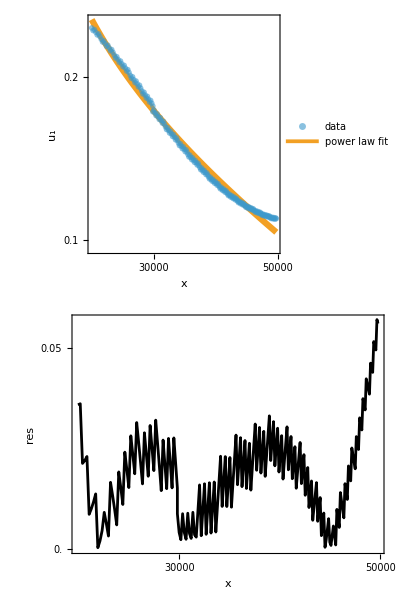

```mathematica
(*1. Define shared X-range to force alignment*)xMin=Min[dataPoints[[All,1]]];
xMax=Max[dataPoints[[All,1]]];
sharedXRange={xMin,xMax};

(*2. Define Shared Settings*)
commonWidth=600;
commonPadding={{80,20},{Automatic,Automatic}};
sharedGrid={Automatic,Automatic}; (*Same X-grid for both*)

(*3. Top Plot:Log-Log*)
topPlot=ListLogLogPlot[{dataPoints,dataFit},Joined->{False,True},PlotStyle->{{Opacity[0.6]},{Opacity[1],Thickness[0.0075]}},PlotMarkers->{{"OpenMarkers",4},None},Frame->True,FrameLabel->{x,Subscript[u,1]},ImageSize->{commonWidth,300},AspectRatio->Full,ImagePadding->{commonPadding[[1]],{0,30}},PlotRange->{sharedXRange,All},(*Force X-axis match*)GridLines->sharedGrid,LabelStyle->{FontSize->18},(*Remove X numbers from top plot*)FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotLegends->Placed[LineLegend[{"data","power law fit"},LegendFunction->Framed],{Right,Top}]];

(*4. Bottom Plot:Log-Linear (Log-x,Linear-y)*)
bottomPlot=ListLogLinearPlot[dataResid,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"x","res"},ImageSize->{commonWidth,100},AspectRatio->Full,ImagePadding->{commonPadding[[1]],{50,0}},PlotRange->{sharedXRange,All},(*Force X-axis match*)GridLines->sharedGrid,LabelStyle->{FontSize->18},FrameTicks->{{{0.00,0.05},None},{Automatic,None}}];


(*5. Assemble*)
Column[{topPlot,bottomPlot},Spacings->0]
```

```mathematica
{{}}
```

```mathematica
getCleanNormalizedyc[xIdx_]:=Module[{Uinf,localUx,u1Profile,u1m,yPeak,yc,normalizedY},
(*Uinf=ux[[1,1,1]];*)
(*Global U_inf*)
localUx=meanUxAll[[xIdx,;;]];
Uinf=Max[localUx];
u1Profile=Uinf-localUx;
(*Find the peak position to center the wake*)
u1m=Max[u1Profile];
(*yPeak=yValues[[First@Ordering[localUx,1]]];*)
u1Interp=Interpolation[Transpose[{yValues,u1Profile}]];
(*Find yc (distance from peak where deficit is half)*)(*Check right side*)yc=y/. FindRoot[u1Interp[y]-0.5*u1m==0,{y,Ly/100}]//Quiet;
{u1Interp,u1m,yc}];
```

```mathematica
xstart
```

400

```mathematica
(*Plot for yc*)
(*Prepare data list*)
xstart=400;
xend2=450;
xend=150;
data=Join[Table[{xValues[[xind]](*//Log*),getCleanNormalizedyc[xind][[3]]//Abs(*//Log*)},{xind,xstart,xend2,1}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[xend2]],getCleanNormalizedyc[xind][[3]]},{xind,1,xend,1}]];

(*Fit to the theoretical power law*)
nlm=NonlinearModelFit[data,aa*(x-x00)^(1/2)+bb/.nlmDeficit["BestFitParameters"][[3]],{aa,bb},x,AccuracyGoal->10];

(*Extract the parameters*)
{bestA,bestB,bestx0}={aa,bb,x00}/. nlm["BestFitParameters"]
```

{-3.84886,1901.79,x00}

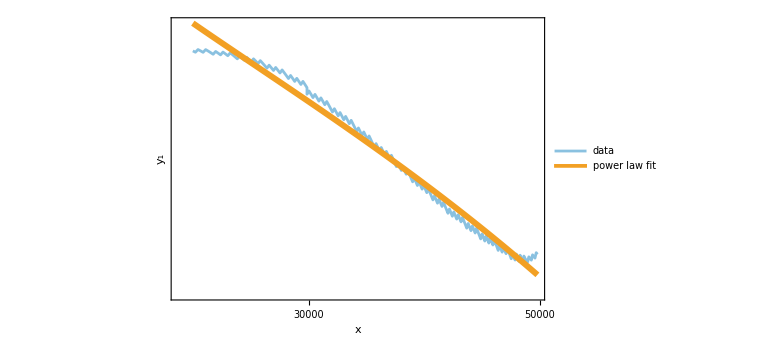

```mathematica
Show[ListLogLogPlot[{Join[Table[{xValues[[xind]](*//Log*),getCleanNormalizedyc[xind][[3]]//Abs(*//Log*)},{xind,xstart,xend2,1}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[xend2]],getCleanNormalizedyc[xind][[3]]},{xind,1,xend,1}]],Join[Table[{xValues[[xind]](*Log[xind]*),aa*(xValues[[xind]]-x00(*xValues[[xstart]]*))^(1/2)+bb/.nlmDeficit["BestFitParameters"][[3]]/. nlm["BestFitParameters"](*150(xind-600)^(1/2)+1000*)(*Log[(xind)^(1/2)]*)}(*-850*),{xind,xstart,xend2,1}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[xend2]],aa*(xValues[[xind]]-xValues[[1]]+xValues[[xend2]]-x00(*xValues[[xstart]]*))^(1/2)+bb/.nlmDeficit["BestFitParameters"][[3]]/. nlm["BestFitParameters"]},{xind,1,xend,1}]]},ImageSize->Large,PlotStyle->{{Opacity[0.6]},{Opacity[1],Thickness[0.0075]}},PlotMarkers->{(*{"OpenMarkers",4}*)None,None},Joined->{True,True},PlotRange->All,LabelStyle->{FontSize->20},PlotLegends->Placed[LineLegend[{"data","power law fit"},LegendFunction->Framed],{Left,Top}],GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{x,Subscript[y, c]},GridLines->Automatic]]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_width"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_widthNBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219.pdf

```mathematica
(*Your data generation logic*)dataPoints=Join[Table[{xValues[[xind]],getCleanNormalizedyc[xind][[3]]//Abs},{xind,xstart,xend2}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[xend2]],getCleanNormalizedyc[xind][[3]]},{xind,1,xend,1}]];

dataFit=Join[Table[{xValues[[xind]],aa*(xValues[[xind]]-x00)^(1/2)+bb/.nlmDeficit["BestFitParameters"][[3]]/. nlm["BestFitParameters"]},{xind,xstart,xend2}],Table[{xValues[[xind]]-xValues[[1]]+xValues[[xend2]],aa*(xValues[[xind]]-xValues[[1]]+xValues[[xend2]]-x00)^(1/2)+bb/.nlmDeficit["BestFitParameters"][[3]]/. nlm["BestFitParameters"]},{xind,1,xend}]];

(*Calculate Residuals:Difference in Y-values*)
dataResid=Transpose[{dataPoints[[All,1]],(dataPoints[[All,2]]-dataFit[[All,2]])/dataPoints[[All,2]]//Abs}];
```

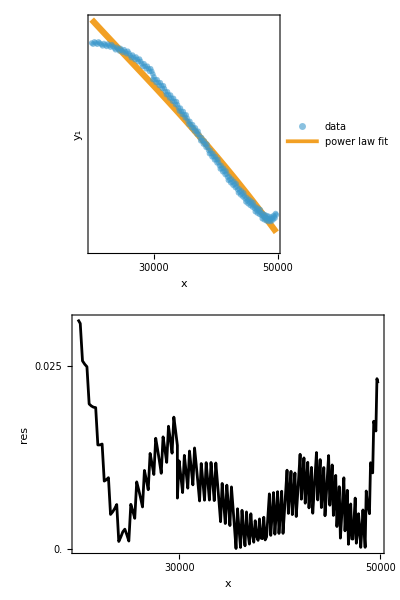

```mathematica
(*1. Define shared X-range to force alignment*)xMin=Min[dataPoints[[All,1]]];
xMax=Max[dataPoints[[All,1]]];
sharedXRange={xMin,xMax};

(*2. Define Shared Settings*)
commonWidth=600;
commonPadding={{80,20},{Automatic,Automatic}};
sharedGrid={Automatic,Automatic}; (*Same X-grid for both*)

(*3. Top Plot:Log-Log*)
topPlot=ListLogLogPlot[{dataPoints,dataFit},Joined->{False,True},PlotStyle->{{Opacity[0.6]},{Opacity[1],Thickness[0.0075]}},PlotMarkers->{{"OpenMarkers",4},None},Frame->True,FrameLabel->{x,Subscript[y, c]},ImageSize->{commonWidth,300},AspectRatio->Full,ImagePadding->{commonPadding[[1]],{0,30}},PlotRange->{sharedXRange,All},(*Force X-axis match*)GridLines->sharedGrid,LabelStyle->{FontSize->18},(*Remove X numbers from top plot*)FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotLegends->Placed[LineLegend[{"data","power law fit"},LegendFunction->Framed],{Left,Top}]];

(*4. Bottom Plot:Log-Linear (Log-x,Linear-y)*)
bottomPlot=ListLogLinearPlot[dataResid,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"x","res"},ImageSize->{commonWidth,100},AspectRatio->Full,ImagePadding->{commonPadding[[1]],{50,0}},PlotRange->{sharedXRange,All},(*Force X-axis match*)GridLines->sharedGrid,LabelStyle->{FontSize->18},FrameTicks->{{{0.00,0.025},None},{Automatic,None}}];


(*5. Assemble*)
Column[{topPlot,bottomPlot},Spacings->0]
```

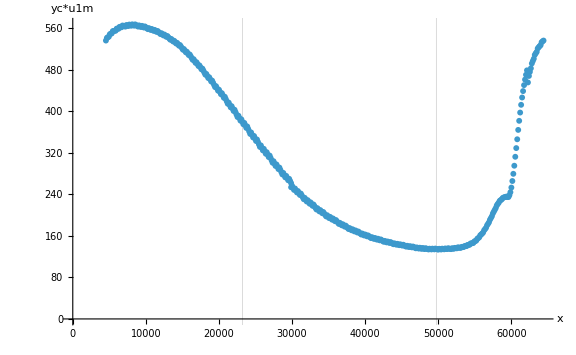

```mathematica
ListPlot[{Join[Table[{xValues[[xind]],getCleanNormalizedu1m[xind]getCleanNormalizedyc[xind][[3]]},{xind,260,450,1}],Table[{xValues[[xind]]+xValues[[450]]-xValues[[1]],getCleanNormalizedu1m[xind]getCleanNormalizedyc[xind][[3]]},{xind,1,260,1}]]}(*,PlotRange->All*),GridLines->{{xValues[[150]]+xValues[[450]]-xValues[[1]],xValues[[400]]},{}},ImageSize->Large(*,PlotLabel->"width deficit product"*),AxesLabel->{"x","yc*u1m"}]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_ycu1m_"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_ycu1m_NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219.pdf

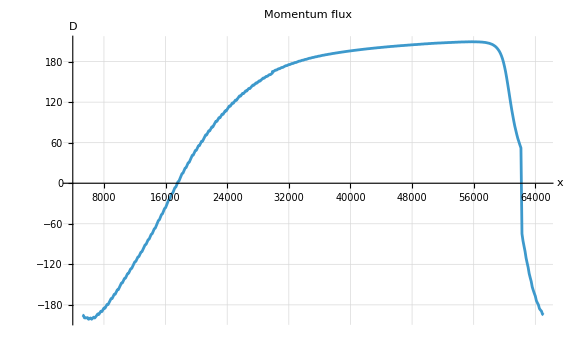

```mathematica
dy=Ly/ny;
(*Calculate Drag Force at a specific X-slice*)
getPhysicalDrag[xIdx_]:=Module[{localUx,integrand},localUx=meanUxAll[[xIdx,;;]];
(*Drag per unit depth=rho*integral[u*(Uinf-u) dy]*)(*Assuming rho=1 for the holographic fluid at the boundary*)
integrand=localUx*(0.3-localUx);
Total[integrand]*dy];

(*Check if Drag is constant downstream*)
dragTrend=Join[Table[{xValues[[i]],getPhysicalDrag[i]},{i,265,450,1}],Table[{xValues[[i]]+xValues[[450]]-xValues[[1]],getPhysicalDrag[i]},{i,1,265,1}]];
ListLinePlot[dragTrend,PlotLabel->"Momentum flux",PlotRange->All,ImageSize->Large,GridLines->Automatic,AxesLabel->{"x","D"}]
```

```mathematica
Export["/home/giulio/Pictures/Jecco_Drag_"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_Drag_NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219.pdf

```mathematica
ux[[1,1,1]]
```

0.275955

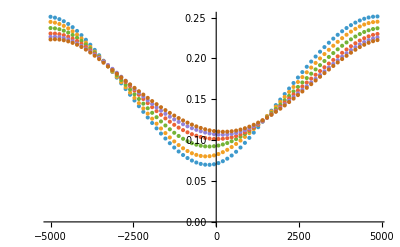

```mathematica
ListPlot[Table[{yValues,(*ux[[1,1,1]]-*)meanUxAll[[xind]]}//Transpose,{xind,400,450,10}]]
```

```mathematica
Momentum[xind_]:=ux[[1,1,1]]meanUxAll[[xind]];
```

{600,50}

Thermal wake

```mathematica
ListContourPlot[meanu0All//Transpose,AspectRatio->ny/nx,ImageSize->Large,PlotLegends->Automatic]
```

-Graphics-

-5785.75

-5713.05

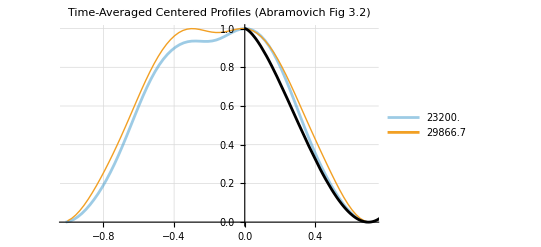

```mathematica
tRange=10;;-1; 
meanu0All=Mean[u0[[tRange,;;,;;]]];
getCleanNormalizedtheta[xIdx_]:=Module[{U0inf,localU0,u0Profile,u0m,yPeak,yc,normalizedY},
(*Uinf=ux[[1,1,1]];*)
(*Global U_inf*)
localU0=meanu0All[[xIdx,;;]];
U0inf=Max[localU0];
u0Profile=U0inf-localU0;
(*Find the peak position to center the wake*)
u0m=Max[u0Profile];
yPeak=yValues[[First@Ordering[localU0,1]]];
u1Interp=Interpolation[Transpose[{yValues,u0Profile}]];
(*Find yc (distance from peak where deficit is half)*)(*Check right side*)yc=y/. FindRoot[u1Interp[yPeak+y]==0.5*u0m,{y,-Lx/2}]//Quiet;
Print [yc];
(*Return centered and normalized data*)
Table[{(y-yPeak)/yc,u1Interp[y]/u0m},{y,Min[yValues],Max[yValues],dy}]]

(*Plotting multiple x-slices to check for collapse*)
xSlices={400,450};
Show[ListLinePlot[Table[getCleanNormalizedtheta[x],{x,xSlices}],PlotRange->All,PlotStyle->{Opacity[0.5],Thick},GridLines->Automatic,PlotLabel->"Time-Averaged Centered Profiles (Abramovich Fig 3.2)",PlotLegends->Table[xValues[[x]],{x,xSlices}]],Plot[(1-(y/0.7)^(3/2))^2,{y,0,3},PlotStyle->Black,PlotRange->All]]
```

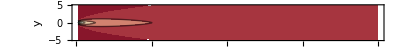

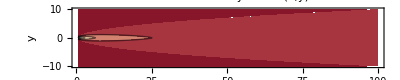

```mathematica
(*Parameters*)U=1;

(*Scaling laws*)
yyc[x_]:=Sqrt[x];
uu1m[x_]:=1/Sqrt[x];

(*Similarity variable*)
eta[x_,y_]:=Abs[y]/yyc[x];

(*Velocity deficit*)
uu1[x_,y_]:=Piecewise[{{uu1m[x]*(1-eta[x,y]^(3/2))^2,eta[x,y]<=1}},0]

(*Total velocity*)
uu[x_,y_]:=U-uu1[x,y]
ContourPlot[uu[x,y],{x,0.5,100},{y,-5,5},PlotPoints->50,ColorFunction->"ThermometerColors",FrameLabel->{"x","y"},PlotLabel->"2D Wake Velocity Field u(x,y)",PlotLegends->Automatic,PlotRange->All,AspectRatio->10/100,ImageSize->Full]
(*2D density plot*)
ContourPlot[uu[x,y],{x,0.5,100},{y,-10,10},PlotPoints->50,ColorFunction->"ThermometerColors",FrameLabel->{"x","y"},PlotLabel->"2D Wake Velocity Field u(x,y)",PlotLegends->Automatic,PlotRange->All,AspectRatio->20/100,ImageSize->Full]
```

#### Source Activation

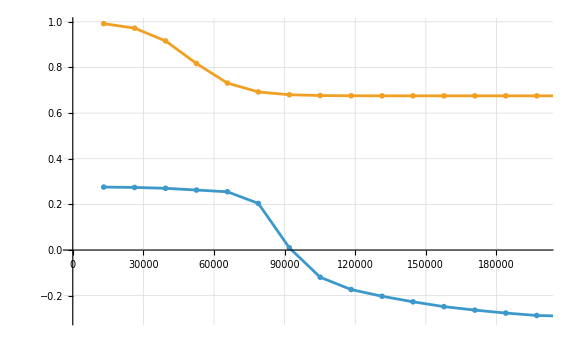

```mathematica
ListPlot[{Transpose[{times,Table[Min[ux[[sss]]],{sss,nt}]}],Transpose[{times,Table[S0[times[[sss]],50000,20000,0.8,0,0,0.5,0,0,0.5],{sss,nt}]}]},PlotRange->{{0,200000},All},Joined->True,GridLines->Automatic,PlotMarkers->"OpenMarkers",ImageSize->Large]
```

#### Visualising Vortices

```mathematica
myColorFunctionScaled=Function[s,Module[{n=2 s-1},(*convert 0..1->-1..1*)Which[n>0,Blend[{RGBColor[0,0,0],RGBColor[1,0.0,0.0]},n],n<0,Blend[{RGBColor[0,0,0],RGBColor[0.0,0.0,1]},-n],True,RGBColor[0,0,0]]]];
```

```mathematica
ux//Length
```

1

```mathematica
ss=ux//Length;
ListDensityPlot[Join[((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,;;midpoint]],2]//Abs,PlotRange->{All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->ny/nx,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,GridLines->Automatic,ClippingStyle->Red]
(*ListDensityPlot[Join[((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,;;midpoint]],2]//Abs,PlotRange->{All,All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->ny/nx,ColorFunctionScaling->True,PlotRange->All,ColorFunction->Hue,GridLines->Automatic]*)
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/vorticity_field_"<>FileName<>"_t"<>ToString[(ss-1) dt each+init dt]<>"jpeg",%]
```

/home/giulio/Pictures/vorticity_field_NBB_gaussian_Lx120000_Ly10000_3d3iu10_6d6u010_Nx600_Ny50_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec5_t709779.jpeg

```mathematica
ss=ux//Length;

u=Table[ux[[tt]],{tt,1,ux//Length}];
v=Table[uy[[tt]],{tt,1,ux//Length}];
uNorm=u/Sqrt[u^2+v^2];
vNorm=v/Sqrt[u^2+v^2];

uux=Table[d[1,0][u[[tt]]],{tt,1,ux//Length}];   (*∂u/∂x*)
uuy=Table[d[0,1][u[[tt]]],{tt,1,ux//Length}];   (*∂u/∂y*)

vx=Table[d[1,0][v[[tt]]],{tt,1,ux//Length}];   (*∂v/∂x*)
vy=Table[d[0,1][v[[tt]]],{tt,1,ux//Length}];  (*∂v/∂y*)

(*AbsVelocity=
*)
```

```mathematica
ux//Dimensions
```

{1,450,75}

```mathematica
Q//Dimensions
```

{}

```mathematica
Q=Table[((vx[[tt]]-uuy[[tt]])^2-(uux[[tt]]^2+vy[[tt]]^2+(uuy[[tt]]+vx[[tt]])^2))//Transpose,{tt,1,ux//Length}];
QTranslated=Table[Join[Q[[tt,;;,midpoint;;]],Q[[tt,;;,;;midpoint]],2],{tt,1,ux//Length}];
QToPlot=Table[Flatten[Table[{xValues[[i]],yValues[[j]],QTranslated[[tt,j,i]]},{i,1,nx},{j,1,ny}],1],{tt,1,ux//Length}];
```

Part::partd: Part specification vx⟦1⟧ is longer than depth of object.

Part::partd: Part specification uuy⟦1⟧ is longer than depth of object.

Part::partd: Part specification uux⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::take: Cannot take positions 290 through -1 in -uux⟦1⟧^2+(-uuy⟦1⟧+vx⟦1⟧)^2-(uuy⟦1⟧+vx⟦1⟧)^2-vy⟦1⟧^2.

Part::take: Cannot take positions 1 through 290 in -uux⟦1⟧^2+(-uuy⟦1⟧+vx⟦1⟧)^2-(uuy⟦1⟧+vx⟦1⟧)^2-vy⟦1⟧^2.

Join::normal1: Expression … at position 1 is expected to have nonatomic subexpression at level 2.

Part::take: Cannot take positions 290 through -1 in -uux⟦2⟧^2+(-uuy⟦2⟧+vx⟦2⟧)^2-(uuy⟦2⟧+vx⟦2⟧)^2-vy⟦2⟧^2.

General::stop: Further output of Part::take will be suppressed during this calculation.

Join::normal1: Expression … at position 1 is expected to have nonatomic subexpression at level 2.

General::stop: Further output of Join::normal1 will be suppressed during this calculation.

Part::partd: Part specification {Join[{Transpose[<<1>>], <<110>>}[[1,<<2>>]], <<1>>, 2], <<110>>}[[1,3,1]] is longer than depth of object.

Part::take: Cannot take positions 290 through -1 in -uux⟦1⟧^2+(-uuy⟦1⟧+vx⟦1⟧)^2-(uuy⟦1⟧+vx⟦1⟧)^2-vy⟦1⟧^2.

Part::take: Cannot take positions 1 through 290 in -uux⟦1⟧^2+(-uuy⟦1⟧+vx⟦1⟧)^2-(uuy⟦1⟧+vx⟦1⟧)^2-vy⟦1⟧^2.

Join::normal1: Expression … at position 1 is expected to have nonatomic subexpression at level 2.

Part::take: Cannot take positions 290 through -1 in -uux⟦2⟧^2+(-uuy⟦2⟧+vx⟦2⟧)^2-(uuy⟦2⟧+vx⟦2⟧)^2-vy⟦2⟧^2.

General::stop: Further output of Part::take will be suppressed during this calculation.

Join::normal1: Expression … at position 1 is expected to have nonatomic subexpression at level 2.

General::stop: Further output of Join::normal1 will be suppressed during this calculation.

Part::partw: Part 4 of … does not exist.

Part::partw: Part 5 of … does not exist.

Part::partw: Part 6 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {Join[{Transpose[<<1>>], <<110>>}[[1,<<2>>]], <<1>>, 2], <<110>>}[[1,3,2]] is longer than depth of object.

Part::partd: Part specification {Join[{Transpose[<<1>>], <<110>>}[[1,<<2>>]], <<1>>, 2], <<110>>}[[1,3,3]] is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
ss=-1;
ListContourPlot[QToPlot[[ss]],PlotRange->{All,All,{0,Max[Q[[ss]]]}}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->ny/nx,GridLines->{{26},{26}},ColorFunction->Hue(*(ColorData["BlueGreenYellow"][1-#]&)*),Contours->20,ClippingStyle->Red]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/Q_field_"<>FileName<>"_t"<>ToString[(ss-1) dt each+init dt]<>"jpeg",%]
```

/home/giulio/Pictures/Q_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8_t814680.jpeg

```mathematica
frames=Table[Show[ListContourPlot[QToPlot[[tt]],PlotRange->{All,All,{0,Max[Q[[tt]]]}}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->ny/nx,GridLines->{{26},{26}},ColorFunction->Hue(*(ColorData["BlueGreenYellow"][1-#]&)*),Contours->20,ClippingStyle->Red](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)],{tt,1,ux//Length}];//AbsoluteTiming
```

{47.1919,Null}

```mathematica
Export["/home/giulio/Videos/Q_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.mp4",frames,"DisplayDurations"->0.8];//AbsoluteTiming
```

{13.8539,Null}

```mathematica
ux//Length
```

109

```mathematica
ss=70
```

70

```mathematica
nSeeds=40;
yCenterMin=ymin/4;
yCenterMax=ymax/4;

xmin=Min[xValues];xmax=Max[xValues];
ymin=Min[yValues];ymax=Max[yValues];
biasedY[]:=Module[{y},While[True,y=RandomReal[{ymin,ymax}];
If[yCenterMin<=y<=yCenterMax,Return[y],(*always accept*)If[RandomReal[]<1/2,Return[y]]  (*accept outer with half prob*)];]]

Seeds=Table[{RandomReal[{xmin,xmax}],biasedY[]},{nSeeds}];
```

```mathematica
σ=(ymax-ymin)0.3

gaussianY[]:=Module[{y},While[True,y=RandomVariate[NormalDistribution[0,σ]];
If[ymin<=y<=ymax,Return[y]];]]

Seeds=Table[{RandomReal[{xmin,xmax}],gaussianY[]},{nSeeds}];
```

2960.

```mathematica
uu=Subdivide[0.001,0.999,nSeeds-1];   (*equispaced probabilities*)
yRaw=Quantile[NormalDistribution[0,σ],uu];
yVals=Clip[yRaw,{ymin,ymax}];
xVals=Subdivide[xmin,xmax,10(nSeeds-1)];

Seeds=Flatten[Table[{x,y},{x,xVals},{y,yVals}],1];
```

```mathematica
ListPlot[Seeds,AspectRatio->1/6,ImageSize->Full]
```

-Graphics-

```mathematica
Qdensity=Table[ListContourPlot[QToPlot[[tt]],PlotRange->{All,All,{0,Max[Q[[tt]]]}}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(tt-1) dt each+init dt],ImageSize->Full,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),GridLines->{{26},{26}},ColorFunction->Hue,Contours->20,ClippingStyle->Red],{tt,ux//Length,ux//Length,15}];//AbsoluteTiming
stream=Table[ListStreamPlot[Join[Table[{{xValues[[i+1]],yValues[[j]]},{uNorm[[tt,i+midpoint,j]],vNorm[[tt,i+midpoint,j]]}},{i,0,midpoint},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{uNorm[[tt,i+1,j]],vNorm[[tt,i+1,j]]}},{i,0,midpoint},{j,c,dd}]],StreamPoints->Seeds,StreamColorFunction->None,PlotLegends->None,ImageSize->Full,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),LabelStyle->Directive[FontSize->16],BaseStyle->{FontSize->16},FrameLabel->{"x","y"},MaxRecursion->4,StreamScale->None,StreamStyle->Thick,PlotRangePadding->None,PerformanceGoal->"Quality",Method->{"Streamlines"->{"MaxStepFraction"->1/500}}],{tt,ux//Length,ux//Length,15}];//AbsoluteTiming
VecField=Table[ListVectorPlot[Join[Table[{{xValues[[i+1]],yValues[[j]]},{uNorm[[tt,i+midpoint,j]],vNorm[[tt,i+midpoint,j]]}},{i,0,midpoint},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{uNorm[[tt,i+1,j]],vNorm[[tt,i+1,j]]}},{i,0,midpoint},{j,c,dd}]],VectorPoints->120,VectorColorFunction->None,VectorStyle->LightGray,AspectRatio->1/6],{tt,ux//Length,ux//Length,15}];//AbsoluteTiming
```

{0.935059,Null}

{2.16651,Null}

{0.969215,Null}

```mathematica
ss=ux//Length
```

109

```mathematica
frames=Table[Show[Qdensity[[tt]],stream[[tt]],PlotRange->All],{tt,1,ux//Length}];//AbsoluteTiming
```

```mathematica
Export["/home/giulio/Videos/Q&velocity_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.mp4",frames,"DisplayDurations"->0.8];//AbsoluteTiming
```

```mathematica
λci//Dimensions
```

{109,300,50}

```mathematica
λci=Table[MapThread[Module[{A={{#1,#2},{#3,#4}},vals},vals=Eigenvalues[A];
Max[Abs[Im[vals]]]   (*swirling strength=absolute imaginary part*)]&,{uux[[tt]],uuy[[tt]],vx[[tt]],vy[[tt]]},2],{tt,1,ux//Length}];
```

```mathematica
λciTranslated=Table[Join[(λci[[tt]]//Transpose)[[;;,midpoint;;]],(λci[[tt]]//Transpose)[[;;,;;midpoint-1]],2],{tt,1,ux//Length}];
λciToPlot=Table[Flatten[Table[{xValues[[i]],yValues[[j]],λciTranslated[[tt,j,i]]},{i,1,nx},{j,1,ny}],1],{tt,1,ux//Length}];
```

```mathematica
ListContourPlot[λciToPlot[[ss]],PlotRange->{All,All,{0,Max[λci]}}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->ny/nx,GridLines->{{26},{26}},ColorFunction->Hue,ColorFunctionScaling->True,Contours->30]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/lambdac_field_"<>FileName<>"_t"<>ToString[(ss-1) dt each+init dt]<>"jpeg",%]
```

/home/giulio/Pictures/lambdac_field_NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec4_t593052.jpeg

```mathematica
ListContourPlot[λciToPlot[[ss]],PlotRange->{All,All,{0,Max[λci]}}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->ny/nx,GridLines->{{26},{26}},ColorFunction->Hue,ColorFunctionScaling->True,Contours->30]
```

-Graphics-

```mathematica
frames=Table[Show[ListDensityPlot[Q,PlotRange->{All,All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(tt-1) dt each+init dt],ImageSize->Large,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),GridLines->{{26},{26}},ColorFunction->"ThermometerColors"](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)],{tt,1,ux//Length}];//AbsoluteTiming
```

{15.519,Null}

```mathematica
Export["/home/giulio/Videos/Q_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.mp4",frames,"DisplayDurations"->0.8];//AbsoluteTiming
```

Export::errframe: frames cannot be converted to an expression suitable for video export.

{1.7964,Null}

```mathematica
λdensity=(*Table[*)ListContourPlot[λciToPlot[[ss]],PlotRange->{All,All,{0,Max[λci[[ss]]]}}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),GridLines->{{26},{26}},ColorFunction->Hue,Contours->20,ClippingStyle->Red];

(*stream=ListStreamPlot[Join[Table[{{xValues[[i+1]],yValues[[j]]},{ux[[ss,i+midpoint,j]],uy[[ss,i+midpoint,j]]}},{i,0,midpoint},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[ss,i+1,j]],uy[[ss,i+1,j]]}},{i,0,midpoint},{j,c,dd}]],StreamPoints->Fine,StreamStyle->{Arrowheads[0.007],Thick[0.05],White},PlotLegends->None,ImageSize->Full,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),LabelStyle->Directive[FontSize->16],BaseStyle->{FontSize->16},FrameLabel->{"x","y"}];*)

Show[λdensity,stream,PlotRange->{All,All}]
Show[Qdensity,stream,PlotRange->All]
```

Part::partd: Part specification λciToPlot⟦120⟧ is longer than depth of object.

Part::partd: Part specification λci⟦120⟧ is longer than depth of object.

ListContourPlot::prng: The value of the option PlotRange -> {All,All,{0,λci⟦120⟧}} is not All, Full, Automatic, a positive machine number or an appropriate list of range specifications.

ListContourPlot::arrayerr: λciToPlot⟦120⟧ must be a valid array.

Show::gcomb: Could not combine the graphics objects in ….

Show[ListContourPlot[λciToPlot⟦120⟧,PlotRange→{All,All,{0,λci⟦120⟧}},PlotLegends→True,PlotLabel→vorticity t=781830.,ImageSize→Full,AspectRatio→0.16388,GridLines→{{26},{26}},ColorFunction→Hue,Contours→20,ClippingStyle→RGBColor[1, 0, 0]],{-Graphics-},PlotRange→{All,All}]

-Graphics-

```mathematica
Export["/home/giulio/Pictures/vorticit&velocity_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg",Show[density,stream,PlotRange->All]]
```

/home/giulio/Pictures/vorticit&velocity_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.jpeg

#### Boundary Stress Tensor

gauge

```mathematica
init=0;
end=1627000;
each=10000;
FNames=Table[StringJoin["gauge_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/home/giulio/University/PhD/Simulations/NBB_gaussian_L500_0d55iu10_1u010_N100_u0d01_tzero5000_tau2000_A0d675_s0d125/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[2]],"Attributes"][[3,1]];
Timing[xi=Table[Import[Name1[[i]],"Data"][[1,;;,;;,1]],{i,1,Name1//Length}]];//AbsoluteTiming
FNames//Length
snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00010000.h5 not found during Import.

Part::partd: Part specification $Failed⟦3,1⟧ is longer than depth of object.

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00000000.h5 not found during Import.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All,1⟧ is longer than depth of object.

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00010000.h5 not found during Import.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All,1⟧ is longer than depth of object.

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00020000.h5 not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{0.148125,Null}

163

dt = $Failed[[3,1]]

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_01620000.h5 not found during Import.

Part::partd: Part specification $Failed⟦3,2⟧ is longer than depth of object.

final time = Part[$Failed, 3, 2]

B at boundary

```mathematica
file="NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary";
init=990000;
end=1000000;
each=1000;
(*FNamesBulk=Table[StringJoin["bulk_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesBulk=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesBulk[[i]],".h5"],{i,FNamesBulk//Length}];
FNamesConstrained=Table[StringJoin["constrained_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesConstrained=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesConstrained[[i]],".h5"],{i,FNamesConstrained//Length}];*)
FNamesBoundary=Table[StringJoin["boundary_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesBoundary=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesBoundary[[i]],".h5"],{i,FNamesBoundary//Length}];
dt=Import[NamesBoundary[[2]],"Attributes"][[3,1]];
times=Table[tim dt each+init dt,{tim,0,(FNamesBoundary//Length)-1}];
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[NamesBoundary[[-1]],"Attributes"][[3,2]]//FullForm]]
snapshots=Table[(tim-1)  each+init ,{tim,1,times//Length}];
b3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/b13"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
g3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/g3"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
fx=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/fx1"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
fy=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/fy1"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
a3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/a3"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
(*Fxh=Table[Import[NamesConstrained[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/Fx c=2"][[;;,;;,-1]],{i,1,NamesBulk//Length}];
Fyh=Table[Import[NamesConstrained[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/Fy c=2"][[;;,;;,-1]],{i,1,NamesBulk//Length}];*)
```

dt = 0.0244444

final time = 24444.44444429339`

```mathematica
times[[1]]
```

0.

```mathematica
b3//Dimensions
```

{101,50,50}

```mathematica
times//Length
```

123

```mathematica
Import[NamesBoundary[[-1]],"Attributes"][[3,2]]
```

39600.

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/fy1,/data/0/fields/fx1,/data/0/fields/b13,/data/0/fields/a3,/data/0/fields/g3}

```mathematica
Tdd=Table[{{a3[[tt]],fx[[tt]],fy[[tt]]},{fx[[tt]],E^(-b3[[tt]])Cosh[g3[[tt]]],Sinh[g3[[tt]]]},{fy[[tt]],Sinh[g3[[tt]]],E^b3[[tt]] Cosh[g3[[tt]]]}},{tt,1,times//Length}];
```

source

```mathematica
S0tilt[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,phi_]:=1-1/2 (1+Tanh[(t-t0)/tau])*A*Exp[-1/2*((((x-x0) Cos[phi]+(y-y0) Sin[phi])^2)/(L sigmax)^2+((-(x-x0) Sin[phi]+(y-y0) Cos[phi])^2)/(L sigmay)^2)]//FullSimplify;
```

```mathematica
tzero=5000;
τ=2000;
Subscript[σ, x]=1/8 1500;
Subscript[σ, x]=1/8 1500;
Subscript[σ, y]=1/8 1500;
ϕ=0;
L=1500;
Amp=0.8;
```

```mathematica
σ=Table[S0tilt[times[[tt]],tzero,τ,Amp,xValues[[xx]],0,Subscript[σ, x],yValues[[yy]],0,Subscript[σ, y],ϕ],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
gbdyuu=Table[DiagonalMatrix[{-1,σ[[tt,xx,yy]],σ[[tt,xx,yy]]}],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
gbdydd=Table[Inverse[gbdyuu[[tt,xx,yy]]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
Tdd//Dimensions
Inverse[gbdyuu[[1,1,1]]]//Dimensions
gbdydd//Dimensions
```

{163,3,3,50,50}

{3,3}

{163,50,50,3,3}

```mathematica
Tud=Table[gbdydd[[tt,xx,yy]].Tdd[[tt,;;,;;,xx,yy]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
Tud[[1,1,1]]//MatrixForm
```

(1.00375 | 0.0484234 | 0.000183251
-0.0487562 | 1.00813 | 0.
-0.00018451 | 0. | 1.00561)

```mathematica
({{1.0085441512899103, 0.00997226868745104, 3.049476349842428*^-7}, {-0.03053769237288054, 3.062412445855567, 6.13882116020775*^-9}, {-9.338293380226364*^-7, 6.13882116020775*^-9, 3.0621101411680796}})
```

{{1.00854,0.00997227,3.04948×10^-7},{-0.0305377,3.06241,6.13882×10^-9},{-9.33829×10^-7,6.13882×10^-9,3.06211}}

```mathematica
Tdd//Dimensions
Tud//Dimensions
```

{163,3,3,50,50}

{163,50,50,3,3}

```mathematica
AllVecs=Table[Eigenvectors[Tud[[tt,xx,yy,;;,;;]]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
AllVecs[[1,;;,;;]]//Dimensions
```

{50,50,3,3}

```mathematica
AllVecs[[10,;;,;;,3,3]]
```

```mathematica
ϵ//Dimensions
```

{163,50,50,3}

```mathematica
ListContourPlot[ϵ[[-20,;;,;;,3]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[AllVecs[[-1,;;,;;,3,3]],PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
vecs=Table[Select[Eigenvectors[Tud[[tt,xx,yy,;;,;;]]](*//Re*),FreeQ[#,Complex](*Module[{u=#,norm},norm=u.gbdydd[[tt,xx,yy]].u;
Re[norm]<0  (*Pick only timelike ones*)]*)&],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
Eigen=Table[Select[Eigensystem[Tud[[tt,xx,yy,;;,;;]]](*//Re*),FreeQ[#[[2]],Complex](*Module[{u=#,norm},norm=u.gbdydd[[tt,xx,yy]].u;
Re[norm]<0  (*Pick only timelike ones*)]*)&],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}]
```

```mathematica
vecs//Dimensions
```

{163,50,50}

```mathematica
u0=vecs[[14;;150,;;,;;,1,1]];
uxx=vecs[[14;;150,;;,;;,1,2]];
uyy=vecs[[14;;150,;;,;;,1,3]];
```

```mathematica
ϵ=Table[Eigenvalues[Tud[[tt,xx,yy,;;,;;]]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
ListContourPlot[ϵ[[1,;;,;;]],PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
ListContourPlot[uyy[[1,;;,;;]],PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
each
```

2000

```mathematica
uxx//Dimensions
```

{244,50,50}

```mathematica
ListContourPlot
```

```mathematica
t=1;
t dt each+(init +64)dt
(*xLineInd=150;*)
Table[{{xValues[[i]],yValues[[j]]},{uxx[[t,j,i]],1uyy[[t,j,i]]}},{i,1,xValues//Length
},{j,1,yValues//Length}]//ListStreamPlot[#,StreamPoints->100000,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->{1000,500},GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt],VectorStyle->Arrowheads[0.01](*,VectorPoints->80*) ,StreamStyle->Arrowheads[0.01],AspectRatio->1/1,ImageSize->Large]&
```

246.009

-Graphics-

```mathematica
t=1;
a=10;
b=40;
c=10;
dd=40;
Table[{{xValues[[i]],yValues[[j]]},{uxx[[t,j,i]],uyy[[t,j,i]]}},{i,a,b
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->{1000,500},GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt],VectorStyle->Arrowheads[0.01],StreamStyle->Arrowheads[0.01],AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),ImageSize->Large]&
```

-Graphics-

#### Drag Forces

```mathematica
L
```

1500.

```mathematica
{157,45,55}
```

{157,45,55}

```mathematica
uy//Dimensions
```

{149,45,55}

```mathematica
DragForceFromTtiRing[ux_,uy_,xGrid_,yGrid_,x0_,y0_,sigmax_,sigmay_,epsilonInner_:0.6^2,epsilonOuter_:1.4^2]:=Module[{nt=Length[ux],nx=Length[xGrid],ny=Length[yGrid],dragForceList,dx,dy,ds,ringMask,normal,forceAtTime},(*Grid spacing*)
dx=xGrid[[2]]-xGrid[[1]];
dy=yGrid[[2]]-yGrid[[1]];
ds=Sqrt[dx^2+dy^2];(*Approximate arc element*)
(*Compute the mask over the grid*)ringMask=Table[If[epsilonInner<((x-x0)^2/sigmax^2+(y-y0)^2/sigmay^2)<epsilonOuter,1,0],{x,xGrid},{y,yGrid}];
normal[x_,y_]:=Module[{nnx,nny,norm},nnx=2 (x-x0)/sigmax^2;
nny=2 (y-y0)/sigmay^2;
norm=Sqrt[nnx^2+nny^2];
If[norm==0,{0,0},{nnx,nny}/norm]];
(*Compute force at each time step*)
dragForceList=Table[Module[{Fx=0.0,Fy=0.0,nvec,Tti},Do[If[ringMask[[i,j]]==1,nvec=normal[xGrid[[i]],yGrid[[j]]];
Tti={ux[[t,i,j]],uy[[t,i,j]]};
{Fx,Fy}+=-Tti*(nvec.{dx,dy});],{i,nx},{j,ny}];
{Fx,Fy}],{t,nt}];
{dragForceList,ringMask}];
```

```mathematica
RelativisticDragForce[ux_,uy_,en_,xGrid_,yGrid_,x0_,y0_,sigmax_,sigmay_,epsilonInner_:0.6^2,epsilonOuter_:1.4^2]:=Module[{nt=Length[ux],nx=Length[xGrid],ny=Length[yGrid],dragForceList,dx,dy,ringMask,normal,gammaFactor},(*Grid spacing*)dx=xGrid[[2]]-xGrid[[1]];
dy=yGrid[[2]]-yGrid[[1]];
(*Define the Ring Mask (Elliptical)*)ringMask=Table[With[{dist=(x-x0)^2/sigmax^2+(y-y0)^2/sigmay^2},If[epsilonInner<dist<epsilonOuter,1,0]],{x,xGrid},{y,yGrid}];
(*Unit Normal Vector to the Ellipse*)normal[x_,y_]:=Module[{nnx,nny,norm},nnx=2 (x-x0)/sigmax^2;
nny=2 (y-y0)/sigmay^2;
norm=Sqrt[nnx^2+nny^2];
If[norm==0,{0,0},{nnx,nny}/norm]];
(*Compute force at each time step*)dragForceList=Table[Module[{Fx=0.0,Fy=0.0,nvec,Txx,Txy,Tyx,Tyy,currentGamma,localE},Do[If[ringMask[[i,j]]==1,nvec=normal[xGrid[[i]],yGrid[[j]]];
localE=en[[t,i,j]];
(*Calculate Lorentz Gamma*)currentGamma=1/Sqrt[1-ux[[t,i,j]]^2-uy[[t,i,j]]^2];
(*Relativistic Stress Tensor Components for 2+1D (P=epsilon/2)*)(*Formula:T^ij=(epsilon+P) u^i u^j+P g^ij*)Txx=(3/2)*localE*(currentGamma*ux[[t,i,j]])^2+(1/2)*localE;
Txy=(3/2)*localE*(currentGamma*ux[[t,i,j]])*(currentGamma*uy[[t,i,j]]);
Tyx=Txy;
Tyy=(3/2)*localE*(currentGamma*uy[[t,i,j]])^2+(1/2)*localE;
(*Integrate flux:F_i=Integral(T_ij*n_j)*)(*We use dx or dy depending on the orientation,effectively dA*)Fx+=(Txx*nvec[[1]]+Txy*nvec[[2]])*dx*dy;
Fy+=(Tyx*nvec[[1]]+Tyy*nvec[[2]])*dx*dy;],{i,nx},{j,ny}];
{Fx,Fy}],{t,nt}];
{dragForceList,ringMask}]
```

```mathematica
u0//Dimensions
ux//Dimensions
```

{111,600,50}

{111,600,50}

```mathematica
{forces,rm}=RelativisticDragForce[ux,uy,u0,xValues,yValues,0,0,(0.5Ly)/(2Pi),(0.5 Ly)/(2Pi)];
```

```mathematica
ListContourPlot[Flatten[Table[{xValues[[i]],yValues[[j]],rm[[i,j]]},{i,nx},{j,ny}],1](*,PlotRange->{{-40,40},{-40,40}}*),AspectRatio->ny/nx]
```

-Graphics-

```mathematica
times,forces[[All,1]]//Dimensions
```

{102}

{102}

```mathematica
ListLinePlot[{Transpose[{times,forces[[All,1]]}],Transpose[{times,forces[[All,2]]}]},PlotLegends->{"Fx","Fy"},AxesLabel->{"t","Force"},PlotRange->All,ImageSize->Large,GridLines->Automatic,Ticks->Automatic]
```

-Graphics-

Now let’s try with continous functions

```mathematica
uxInterp=Table[ListInterpolation[ux[[t]],{xValues,yValues}],{t,nt}];
uyInterp=Table[ListInterpolation[uy[[t]],{xValues,yValues}],{t,nt}];
```

```mathematica
x0=0;
y0=0;
```

```mathematica
ellipse[θ_,sigmax_,sigmay_]:={x0+sigmax Cos[θ],y0+sigmay Sin[θ]};

(*Tangent and normal*)
tangent[θ_,sigmax_,sigmay_]:={-sigmax Sin[θ],sigmay Cos[θ]};

normal[θ_,sigmax_,sigmay_]:=Normalize@{Cos[θ]/sigmax,Sin[θ]/sigmay};

(*Arc element*)
ds[θ_,sigmax_,sigmay_]:=Norm[tangent[θ]] dθ;
```

```mathematica
L=-2yValues[[1]]
```

10000.

```mathematica
ParametricPlot[ellipse[θ,(0.5 L)/(2Pi),(0.5 L)/(2Pi)],{θ,0,2Pi}]
```

-Graphics-

```mathematica
computeDragForce[t_,σx_,σy_]:=Module[{uxf,uyf,Fx,Fy,sigmax=σx,sigmay=σy},
uxf=uxInterp[[t]];
uyf=uyInterp[[t]];
Fx=-NIntegrate[Module[{x,y,n},{x,y}=ellipse[θ,sigmax,sigmay];
n=normal[θ,sigmax,sigmay];
uxf[x,y]*n[[1]]*Norm[tangent[θ,sigmax,sigmay]]],{θ,0,2 Pi}];
Fy=-NIntegrate[Module[{x,y,n},{x,y}=ellipse[θ,sigmax,sigmay];
n=normal[θ,sigmax,sigmay];
uyf[x,y]*n[[2]]*Norm[tangent[θ,sigmax,sigmay]]],{θ,0,2 Pi}];
{Fx,Fy}];
```

```mathematica
dragForceList=Table[computeDragForce[t,(0.5Ly)/(2Pi),(0.5 Ly)/(2Pi)],{t,1,nt}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.429417}. NIntegrate obtained -5.29354×10^-12 and 9.00945×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.29474}. NIntegrate obtained -1.62701×10^-15 and 4.56136×10^-21 for the integral and error estimates.

```mathematica
ListLinePlot[{{times,dragForceList[[;;,1]]}//Transpose,{times,dragForceList[[;;,2]]}//Transpose},PlotRange->All,ImageSize->Large,PlotLegends->{"Drag Force","Lift Force"},GridLines->{{},{0.1,0.1^2}}]
```

-Graphics-

```mathematica
ListLinePlot[{forces[[All,1]],forces[[All,2]]},PlotLegends->{"Fx","Fy"},AxesLabel->{"t","Force"},PlotRange->All]
```

-Graphics-

#### Mode Analysis

```mathematica
uyMeanx=Mean/@Transpose[uy//Abs,{1,3,2}];
uxMeanx=Mean/@Transpose[ux,{1,3,2}];
```

```mathematica
ListContourPlot[uxMeanx,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
uyFFT=Fourier/@uyMeanX;
```

```mathematica
uyAmps=Abs[uyFFT];
```

```mathematica
ListLinePlot[Log[uyAmps[[All,#]]]&/@Range[1,3],PlotLegends->Placed[Range[1,10],Above],PlotLabel->"Log Amplitude of Modes vs. Time",AxesLabel->{"Time Step","log|A_n(t)|"}]
```

-Graphics-

```mathematica
ListLinePlot[uyAmps[[;;100,#]]&/@Range[1,10],PlotLegends->Placed[Range[1,10],Above],PlotLabel->"Log Amplitude of Modes vs. Time",AxesLabel->{"Time Step","log|A_n(t)|"},PlotRange->All]
```

-Graphics-

```mathematica
modeN=uyAmps[[All,1]];
fit=LinearModelFit[Transpose[{Range[Length[modeN]],Log[modeN]}],x,x];
growthRate=fit["BestFitParameters"][[1]]
```

-35.868

```mathematica
ListLinePlot[Abs[Fourier[uyMeanX[[-1]]]],PlotLabel->"FFT at time t",PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Log[uyAmps[[All,1]]]]  (*Primary mode amplitude*)
```

-Graphics-

```mathematica
fit=LinearModelFit[Transpose[{Range[300],Log[uyAmps[[All,1]]]}],x,x];
growthRate=fit["BestFitParameters"][[1]]
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«290»},{-56.0698,-38.7597,-38.5651,-38.398,-38.2706,-38.1442,-38.035,-37.9364,-37.8433,-37.7617,«675»}} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

BestFitParameters

#### QNM Data Analysis

This section is about a superficial QNM analysis but is not commented!

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/fy1,/data/0/fields/fx1,/data/0/fields/b13,/data/0/fields/a3,/data/0/fields/g3}

```mathematica
Transpose[{times[[;;aa]],(1+Obj[[;;aa,-1,1,1,1]])}]
```

{{0.5,1.},{1.,1.},{1.5,1.},{2.,1.},{2.5,1.},{3.,1.},{3.5,1.},{4.,1.},{4.5,1.00001},{5.,1.00004},{5.5,1.0002}}

```mathematica
a
```

1

```mathematica
nt
```

81

```mathematica
aa=nt;
w1i=-0.6;
AreaFit=NonlinearModelFit[Transpose[{times[[;;aa]],(1+Obj[[;;aa,-1,1,1,1]])}],Ain+da(1-Exp[-tt (2w1i)]),{Ain,da},{tt}];
```

```mathematica
ListPlot[{Transpose[{times[[;;aa]],Table[AreaFit[times[[tind]]],{tind,1,aa}]}],Transpose[{times[[;;aa]],(1+Obj[[;;aa,-1,1,1,1]])}]},PlotRange->All,Joined->True]
```

-Graphics-

```mathematica
AreaFit["BestFitParameters"]
AreaFit[10]
```

{Ain→0.999085,da→0.000641026}

0.999726

```mathematica
(*fy1=Obj[[;;,1,;;,;;,1]];
fx1=Obj[[;;,2,;;,;;,1]];
g3=Obj[[;;,-1,;;,;;,1]];*)
a4=Obj[[;;,2,;;,;;,1]];
```

```mathematica
a4[[-1,1,1]]//FullForm
```

```mathematica
-0.9499999996305506
```

-0.95

```mathematica
ListPlot[a4[[;;,1,1]]-a4[[1,1,1]]]
```

-Graphics-

```mathematica
fy1[[-1,1,1]]
fx1[[-1,1,1]]
```

9.80632×10^-15

-6.26397×10^-15

```mathematica
2.934078881559211*^-14
```

2.93408×10^-14

```mathematica
7.958018822646281*^-15
```

7.95802×10^-15

```mathematica
fy1[[;;,1,1]]//ListPlot
```

-Graphics-

```mathematica
a4Horizon=Obj[[;;,-2,;;,;;,1]];
```

```mathematica
Lastg3=Obj[[-1,-1,1,1,1]];
```

```mathematica
fx1//Dimensions
```

{5,50,50}

```mathematica
fx1=fx;
```

```mathematica
fx1=Obj[[;;,2,;;,;;,1]];
fy1=Obj[[;;,1,;;,;;,1]];
(*g3=Obj[[;;,1,;;,;;,1]];*)
(*b1=Obj[[;;,1,;;,;;,1]];
b2=Obj[[;;,3,;;,;;,1]];
a4=Obj[[;;,2,;;,;;,1]];*)
```

```mathematica
ListContourPlot[fy1[[20]]]
```

-Graphics-

```mathematica
1-(-a4Horizon[[-1,10,1]])^(1/4)//FullForm
```

0.729938

```mathematica
a4Horizon[[2,10,1]]/a4Horizon[[1,10,1]]
```

0.992191

```mathematica
E^-30//N
```

```mathematica
g3[[1,1,1]]^4
```

0.0000488899

```mathematica
Timess[[5000]]
```

150.

```mathematica
10 10 0.003
```

0.3

```mathematica
a4Horizon//Dimensions
```

{109,50,600}

```mathematica
ListContourPlot[a4Horizon[[150]],AspectRatio->1/12,ImageSize->Full,PlotRange->All,PlotLegends->Automatic]
```

Part::partw: Part 150 of {{{-0.00525463, -0.00525463, -0.00525463, -0.00525463, -0.00525463, -0.00525463, <<591>>, -0.00525463, -0.00525463, -0.00525463}, <<49>>}, <<108>>} does not exist.

ListContourPlot::arrayerr: {{{-0.00525463, -0.00525463, -0.00525463, -0.00525463, -0.00525463, <<592>>, -0.00525463, -0.00525463, -0.00525463}, <<49>>}, <<108>>}[[150]] must be a valid array.

$Aborted

```mathematica
Timess=Table[(*dt*)dt (1(*each*) i),{i,0,(a4Horizon//Length)-1}];
Show[Table[ListPlot[Transpose[{Timess,a4Horizon[[;;,xx,1]]^(-1/4)/a4Horizon[[1,xx,1]]^(-1/4)}],PlotStyle->{RGBColor[xx/(a4Horizon[[1,;;,1]]//Length),0.01,0.5],Opacity[0.5]},(*Joined->True,*)PlotRange->All,GridLines->{Automatic}],{xx,5,(*a4Horizon[[1,;;,1]]//Length*)6}],PlotRange->All, PlotRange->All]
```

-Graphics-

```mathematica
Table[1+g3[[t,1,1]] (E^(2 0.1 Timess[[t]])-1),{t,1,999}];
```

```mathematica
g3[[;;,1,1]]//Length
```

5000

```mathematica
ListPlot[Table[1+g3[[t,1,1]]^2 (E^(2 0.1 Timess[[t]])-1),{t,1,999}]]
```

-Graphics-

```mathematica
( 2 4.75424828181694102162317308916543566812627111042109822299035709775135175404699`55.)^-1
```

0.1051690972708126957478928121644224979862742346551882409

```mathematica
ListPlot[{fy1[[;;,1,1]]-fy1[[-1,1,1]]//Abs//Log,g3[[;;,1,1]]-g3[[-1,1,1]]//Abs//Log},AxesLabel->{"t","Log_e"},PlotLegends->{"f_x","g"},PlotRange->All,Joined->True,GridLines->{Automatic},GridLinesStyle->Dashed]
```

-Graphics-

```mathematica
ListPlot[{g3[[;;400,1,1]]-g3[[-1,1,1]]//Abs//Log},AxesLabel->{"t","Log_e"},PlotLegends->{"f_x","g"},PlotRange->All,Joined->True,GridLines->{Automatic},GridLinesStyle->Dashed]
```

-Graphics-

```mathematica
(SeriesCoefficient[u^-2 Sinh[u^4 g3[[1,1,10]]],{u,0,2}])^4//Normal
fx1[[1,1,1]]^4
```

0.0000488899

1.37861×10^-10

```mathematica
tInd=200;
Solve[E^(-b2[[tInd,1,1]])Sinh[g3[[tInd,1,1]]]==Ag E^(- 0.10(Timess[[tInd]])),Ag]
Solve[E^(-b2[[tInd,1,1]])Sinh[fx1[[tInd,1,1]]]==Afx E^(- 0.10(Timess[[tInd]])),Afx]
```

{{Ag→6.0857×10^-8}}

{{Afx→-1.74399×10^-7}}

```mathematica
aaa=1;
bbb=250;
```

```mathematica
fx1[[;;,1,1]]//Length
```

251

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
FitResfx=Fit[Transpose[{Timess[[aaa;;bbb]],(fx1[[aaa;;bbb,1,1]]-fx1[[-1,1,1]])//Abs//Log}],{1,tt},tt]
```

-2.05169-0.136008 tt

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
FitResg=Fit[Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb,1,1]]-g3[[-1,1,1]])//Abs//Log}],{1,tt},tt]
```

-3.11604-2.8505 tt

#### g Fits

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/fy1,/data/0/fields/fx1,/data/0/fields/b13,/data/0/fields/a3,/data/0/fields/g3}

```mathematica
nt
```

201

```mathematica
g3=Obj[[;;,-1,;;,;;,-1]];
```

```mathematica
ListContourPlot[g3[[100,;;,;;]]//Transpose,PlotRange->All]
```

-Graphics-

```mathematica
w1gi->4.759861241115798,w1gr->5.162073812553917,w2gi->2.745919736473629,w2gr->3.118311850837873
```

```mathematica
w0r=3.11945159116590140667726984186100634853095499472948675543440431717732681278292`55. ;
w0i=2.74667574434060639673424074409714552362302736020758738193586675171449584142752`55.;
w1r=5.16952097576222954940461885889722499194572185535488411636773071714438971882811`55. ;
w1i=4.76357011692046086364514648370905218950138549522150190381951475957642922361821`55. ;
w2r=7.1879308259996117388`10.;
w2i=6.7695649090762023235`10.;
w10r=21.213025329117309941952636088323838764;
w10i=20.7772323845847696293696401231951973538;
```

```mathematica
A0oft[t_]:=1-E^((w0i-w1i)(t))Cos[(w0r-w1r)t(*(t-t0)+ϕ0*)];
A1oft[t_]:=1-E^((w1i-4.817343912819517)t)Cos[(w1r-5.10630467802839)t](*Sin[-(w0r-w1r)(t-t0)+ϕ1]*);
(*A1inoft[t_]:=E^((w1i-4.817343912819517)t)Cos[(w1r-5.10630467802839)t]*)(*Sin[-(w0r-w1r)(t-t0)+ϕ1]*)
```

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/fy1,/data/0/fields/fx1,/data/0/fields/b13,/data/0/fields/a3,/data/0/fields/g3}

```mathematica
times[[-1]]
```

12.02

```mathematica
g3=Obj[[;;,5,;;,;;,1]];
g3//Length
ListPlot[Table[g3[[;;,1,y]](*g3[[-1,1,y]]*)//Re//Abs//Log,{y,1,1,2}],PlotRange->All,ImageSize->Full,Joined->True]
```

1001

-Graphics-

```mathematica
Dimensions[k0AmplitudeTime]
```

{201}

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
yGrid=yValues(*Table[y,{y,0,Ly-Ly/ny,Ly/ny}]*); (*Assuming a uniform grid*)

(*1. Reduce the data:Since x is constant,we take the first x-slice*)
(*g3 dimensions:[time,x,y]->g32D dimensions:[time,y]*)
g32D=g3[[All,1,All]];

(*2. Define the projection kernel for k=1*)
(*We use Exp[-I*k*y] where k=1*)
kernel0=Exp[-I*0*yGrid(2Pi)/Ly];

kValue=1;
kernel1=Exp[-I*kValue*yGrid(2Pi)/Ly];

kValue2=2;
kernel2=Exp[-I*kValue2*yGrid(2Pi)/Ly];
kValue3=3;
kernel3=Exp[-I*kValue3*yGrid(2Pi)/Ly];
kernel4=Exp[-I*4*yGrid(2Pi)/Ly];


(*3. Perform the Spatial Projection (Fourier Transform) for each time step*)
(*This results in a 1D list of complex amplitudes indexed by time*)
k0AmplitudeTime=Map[#.kernel0/ny&,g32D];
k1AmplitudeTime=Map[#.kernel1/ny&,g32D];
k2AmplitudeTime=Map[#.kernel2/ny&,g32D];
k3AmplitudeTime=Map[#.kernel3/ny&,g32D];
k4AmplitudeTime=Map[#.kernel4/ny&,g32D];

(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{(k0AmplitudeTime)//Re//Abs//Log,k1AmplitudeTime//Re//Abs//Log,k2AmplitudeTime//Re//Abs//Log,k3AmplitudeTime//Re//Abs//Log,(k4AmplitudeTime)//Re//Abs//Log},PlotRange->All(*{{0,150},{-30,-18}}*),FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Full,PlotLegends->Placed[{"k=0","k=1 ","k=2","k=3","k=4"},{Right,Top}],GridLines->Automatic]
```

-Graphics-

```mathematica
E^-12//N
```

6.14421×10^-6

```mathematica
nt
```

1001

```mathematica
aaa=10;
bbb=nt;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(k2AmplitudeTime[[aaa;;bbb]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(k2AmplitudeTime[[aaa;;bbb]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
FitResgWr=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)(A1 E^(-wi1 (t-t01))Cos[wr1(t-t01)+ϕ1])+A2 Exp[-wi2(t-t01)](*Cos[0(t-t02)+ϕ2]*)(*//Abs//Log*) 
,{{A1,0.05},{A2,0.05^3},ϕ1,ϕ2,{wi1,2.69},{wi2,0.61},{wr1,2},{wr2,10^-10},{t01,-9},t02},{t},MaxIterations->5000,ConfidenceLevel->0.9999999999];
FitResgWr["BestFitParameters"]
```

{A1→-0.00294074,A2→-0.00113797,ϕ1→2.57434,ϕ2→1.,wi1→2.49711,wi2→0.609193,wr1→2.00934,wr2→1.×10^-10,t01→1.11082,t02→1.}

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->Placed[{"numerical"},{Right,Top}],GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->Placed[{"fit"},{Right,Top}],PlotStyle->{PointSize[0.006],Thickness[0.009],Opacity[0.4],RGBColor[0.9,.6,0.3]}],Plot[{(A2//Abs) Exp[-wi2(t-t01)]/.FitResgWr["BestFitParameters"]//Abs//Log},{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->Placed[{"fund fit"},{Right,Top}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],Plot[{(A1 E^(-wi1 (t-t01))Cos[wr1(t-t01)+ϕ1])/.FitResgWr["BestFitParameters"]//Abs//Log},{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->Placed[{"1st ot fit"},{Right,Top}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.1,.1,0.3]}],PlotRange->{All,{-30,0}},AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
ClearAll[t];
aaa=400;
bbb=900;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Datag3=Transpose[{Timess[[aaa;;bbb]],(k2AmplitudeTime[[aaa;;bbb]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(k2AmplitudeTime[[aaa;;bbb]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
FitResgWr2=NonlinearModelFit[Datag3Log,-wi (t-t0)+0.05^3(*A2 E^(-wi (t-t0))*)(*Cos[wr (t-t0)+ϕ]*)(*+A2 E^(-wi2 (t-t0))Cos[0 (t-t0)+ϕ2]/.FitResgWr["BestFitParameters"]*)(*//Abs//Log*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{(*a1g,a2g,A2,A0,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,*)wi,wr,ϕ,{A2,0.05^3},ϕ2,{t0,1.1108156185790576},wi2,wr2},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
FitResgWr2["BestFitParameters"]
```

{wi→0.618795,wr→1.,ϕ→1.,A2→0.000125,ϕ2→1.,t0→-9.79442,wi2→1.,wr2→1.}

```mathematica
0.05^3
```

0.000125

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[FitResgWr2[t],{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
k0AmplitudeTime[[;;]]-k0AmplitudeTime[[-1]]//Re//Length
Timess//Length
```

9001

9002

```mathematica
Show[ListPlot[Transpose[{Timess[[;;-2]],(k1AmplitudeTime[[;;]]-k1AmplitudeTime[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.6],RGBColor[0.6,0.7,0.6]},PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Full,Joined->True],Plot[FitResgWr[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st phase fit"},PlotStyle->{Blue,Opacity[0.8],Dashed},PlotLegends->Placed["Numerical", {Center}]],Plot[FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"2nd phase fit"},PlotStyle->{Red,Opacity[0.8],Dashed}],Plot[FitResgWr[t]+FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st+2nd"},PlotStyle->{Black,Opacity[0.4],Point}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Timess[[;;-2]],(k0AmplitudeTime[[;;]]-k0AmplitudeTime[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}],PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.6],RGBColor[0.6,0.7,0.6]},PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Full,Joined->True],Plot[FitResgWr[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st phase fit"},PlotStyle->{Blue,Opacity[0.8],Dashed},PlotLegends->Placed["Numerical", {Center}]],Plot[FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"2nd phase fit"},PlotStyle->{Red,Opacity[0.8],Dashed}],Plot[FitResgWr[t]+FitResgWr2[t]//Abs//Log,{t,Timess[[1]],Timess[[-1]]},PlotLegends->{"1st+2nd"},PlotStyle->{Black,Opacity[0.4],Point}],PlotRange->{{0,9.8},{-60,0.1}},AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/Jecco_QNM_gxy"<>FileName<>".pdf",%]
```

/home/giulio/Pictures/Jecco_QNM_gxyBB_QNM_4D_L10_N100_uAH1_0d1ui12_2u024_A0d05_k0_o1_dt0d001.pdf

```mathematica
aaa2=370;
bbb=1400;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Lastg3=g3[[-1,1,1]];
Datag3=Transpose[{Timess[[aaa;;bbb]],(k0AmplitudeTime[[aaa;;bbb]]-k0AmplitudeTime[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*-Lastg3*)(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(k0AmplitudeTime[[aaa;;bbb]]-k0AmplitudeTime[[-1]]//Re(*g3[[aaa;;bbb,1,1]]*)(*Lastg3*))//Abs//Log}];
```

```mathematica
ClearAll[t];
FitResgWr=NonlinearModelFit[Datag3,(*-wi (t-t0)+A1*)A1 E^(-wi (t-t0))Cos[wr (t-t0)+ϕ1](*//Abs//Log*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]+*)(*A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*) (*A0oft[t]*)(*+a1g  E^(-w1gi (t))Cos[w1gr (t-t0)+ϕ1g]*)(*+a2g E^(-w2gi (t-t0))Cos[ w2gr (t-t0)+ϕ2g] *)
,{(*a1g,a2g,A2,A0,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,*)A1,ϕ1,t0,wi,wr},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->5000,ConfidenceLevel->0.9999999999];
```

```mathematica
FitResgWr["BestFitParameters"]
```

{A1→0.0134975,ϕ1→-0.2329,t0→0.268328,wi→4.91663,wr→3.16171}

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
ListPlot[Datag3]
```

-Graphics-

```mathematica
Plot[{A0oft[t]/.FitResgWr["BestFitParameters"]},{t,0,8},PlotRange->All]
```

-Graphics-

```mathematica
Plot[{A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]/.FitResgWr["BestFitParameters"],A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] A0oft[t]/.FitResgWr["BestFitParameters"]},{t,0,8},PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
Plot[{A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]/.FitResgWr["BestFitParameters"]//Abs//Log,A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] A0oft[t]/.FitResgWr["BestFitParameters"]//Abs//Log(*0.05 A1 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]*) (*A0oft[t]*)(*/.FitResgWr["BestFitParameters"]//Abs//Log*)},{t,0,8},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] (*A0oft[t]*)/.FitResgWr["BestFitParameters"],0.2 A1 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1] (*A0oft[t]*)/.FitResgWr["BestFitParameters"],0.2 A2 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2] (*A0oft[t]*)/.FitResgWr["BestFitParameters"](*,0.25 E^(-w1i (t-times[[aaa]]))Cos[w1r (t-times[[aaa]])+ϕ1]/.FitResgWr["BestFitParameters"]*)(*,0.1 E^(-w2i (t-times[[aaa]]))Cos[w2r (t-times[[aaa]])+ϕ2] (*A0oft[t]*)/.FitResgWr["BestFitParameters"]//Abs//Log*)(*,A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] A0oft[t]/.FitResgWr["BestFitParameters"]//Abs//Log,0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]/.FitResgWr["BestFitParameters"]//Abs//Log*)},{t,0,3},PlotRange->All]
```

-Graphics-

```mathematica
A0oft[0]
```

0

```mathematica
aaa
```

6

```mathematica
ListPlot[FitResgWr["FitResiduals"]//Abs//Log,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(g3[[aaa;;bbb,1,1]]-g3[[-1,1,1]]-Map[FitResgWr,times[[aaa;;bbb]]])//Abs//Log,PlotRange->All]
```

-Graphics-

```mathematica
aaaPost=aaa+60;
bbbPost=aaa+130;
```

```mathematica
Datag3Post=Transpose[{Timess[[aaaPost;;bbbPost]],((g3[[aaaPost;;bbbPost,1,1]]-g3[[-1,1,1]]-Map[FitResgWr,times[[aaaPost;;bbbPost]]]))(*//Abs//Log*)}];
Datag3LogPost=Transpose[{Timess[[aaaPost;;bbbPost]],((g3[[aaaPost;;bbbPost,1,1]]-g3[[-1,1,1]]-Map[FitResgWr,times[[aaaPost;;bbbPost]]]))//Abs//Log}];
ListPlot[Datag3LogPost]
```

-Graphics-

```mathematica
FitResgWrPost=NonlinearModelFit[Datag3Post(*Post*),A 0.1 E^(-wi (t-t0))Cos[wr(t-t0)+ϕ],{A,t0,wi,wr,ϕ},{t(*,Timess[[aaa]],Timess[[bbb]]*)}];
```

```mathematica
FitResgWrPost["BestFitParameters"]
```

{A→-10.1477,t0→-3.92034,wi→3.74895,wr→-3.30255,ϕ→6.46047}

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
Show[ListPlot[Datag3LogPost,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResgWrPost[t]//Abs//Log,{t,Timess[[aaaPost]],Timess[[bbbPost]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]},PlotRange->All],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
ListPlot[FitResgWrPost["FitResiduals"]//Abs//Log,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb,1,1]]-g3[[-1,1,1]])//Abs//Log}](*,Transpose[{Timess[[aaa;;bbb]],g3[[1]]+g3[[2,1]]  Timess[[aaa;;bbb]]}]*),Transpose[{Timess[[aaa;;bbb]],FitResg[[1]]+FitResg[[2,1]]  Timess[[aaa;;bbb]]}]},AxesLabel->{"t","Log_e"},PlotLegends->{"f_x","m=4.73"}(*,PlotRange->All*),Joined->True,GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large]
```

-Graphics-

I subtract the initial data mode solution to the data

```mathematica
OTSol=Table[A E^(- wi(Timess[[t]]-t0))Cos[wr(Timess[[t]]-t0)]/.FitResgWr["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
```

```mathematica
Timess(*[[1;;100]]*)//Length
```

102

```mathematica
aaaSub=90;
bbbSub=250;
```

```mathematica
90
```

```mathematica
ListPlot[{{Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3
)-OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose,Transpose[{Timess[[aaaSub;;bbbSub]],g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3//Abs//Log}],{Timess[[aaaSub;;bbbSub]],(*(g3[[aaaSub;;bbbSub,1,1]]-g3[[-1,1,1]])-*)OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose},Joined->True,ImageSize->Large,GridLines->{{},{-11.2}}]
```

-Graphics-

```mathematica
Data3gSub={Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]}//Transpose;
Data3gLogSub={Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose;
```

```mathematica
FitResgWrSub=NonlinearModelFit[Data3gSub,(A E^(-wi(t-t0))Cos[wr(t-t0)])(*A2 +wi2 (t-t0)*)+A2 E^(-0.1 (t-t0))(*0.0001*)(*A3 E^(- wi3(t-t000))Cos[-wr3(t-t000)]*)(*/.t0->-0.2709949114246018*)(*/.DominantFit*),{A,wr,wi,t0,A2,wi2,t00,A3,wr3,wi3,t000},{t},ConfidenceLevel->.9999,MaxIterations->100000];
```

```mathematica
FitResgWrSub["BestFitParameters"]
```

{A→0.0000918635,wr→-10.6146,wi→12.3218,t0→0.161172,A2→-0.0000925724,wi2→1.,t00→1.,A3→1.,wr3→1.,wi3→1.,t000→1.}

```mathematica
Show[ListPlot[Data3gLogSub,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResgWrSub[t]//Abs//Log,{t,Timess[[aaaSub]],Timess[[bbbSub]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
FitResgWrSub["BestFitParameters"]
```

{A→0.0000918635,wr→-10.6146,wi→12.3218,t0→0.161172,A2→-0.0000925724,wi2→1.,t00→1.,A3→1.,wr3→1.,wi3→1.,t000→1.}

```mathematica
OTSol2=Table[FitResgWrSub[Timess[[t]]],{t,1,Timess(*[[1;;100]]*)//Length}];
```

```mathematica
ListPlot[{(*{Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3[[1,1]])//Abs//Log}//Transpose*){Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose,{Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]-OTSol2[[aaaSub;;bbbSub]]//Abs//Log}//Transpose},Joined->True,ImageSize->Large,GridLines->{{},{-11.2}},PlotRange->All]
```

-Graphics-

#### fx Fits

```mathematica
fy1=Obj[[;;,1,;;,;;,1]];
fx1=Obj[[;;,2,;;,;;,1]];
```

```mathematica
ListContourPlot[fx1[[20]]//Transpose,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListPlot[fy1[[1000,1]]]
```

-Graphics-

```mathematica
frames=Table[Show[ListPlot[(*((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)*)(*Join[((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)[[;;,midpoint;;]],((d[1,0][uy[[tt]]]-d[0,1][ux[[tt]]])//Transpose)[[;;,;;midpoint-1]],2]*)fy1[[tt,1]]//Transpose,PlotRange->All,
PlotLabel->"fy t="<>ToString[(tt-1) dt each+init dt],ImageSize->Large,GridLines->Automatic](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)],{tt,nt(*ux//Length*)}];//AbsoluteTiming
```

{29.0832,Null}

```mathematica
Export["/home/giulio/Videos/QNM_fy_"<>FileName<>".mp4",frames,"DisplayDurations"->55.0];//AbsoluteTiming
```

{116.084,Null}

```mathematica
ListPlot[(*-fx1[[;;,1,1]]*)Table[+fy1[[;;,50,y]](*-(-fx1[[-1,1,1]]*)(*-fy1[[-1,50,50]]*)//Abs//Log,{y,50,63,1}],PlotRange->All,ImageSize->Large,Joined->True]
```

-Graphics-

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
yGrid=yValues(*Table[y,{y,0,Ly-Ly/ny,Ly/ny}]*); (*Assuming a uniform grid*)

(*1. Reduce the data:Since x is constant,we take the first x-slice*)
(*g3 dimensions:[time,x,y]->g32D dimensions:[time,y]*)
fx2D=fx1[[All,1,All]];

(*2. Define the projection kernel for k=1*)
(*We use Exp[-I*k*y] where k=1*)
kernel0=Exp[-I*0*yGrid(2Pi)/Ly];

kValue=1;
kernel1=Exp[-I*kValue*yGrid(2Pi)/Ly];

kValue2=2;
kernel2=Exp[-I*kValue2*yGrid(2Pi)/Ly];
kernel3=Exp[-I*3*yGrid(2Pi)/Ly];
kernel4=Exp[-I*4*yGrid(2Pi)/Ly];

(*3. Perform the Spatial Projection (Fourier Transform) for each time step*)
(*This results in a 1D list of complex amplitudes indexed by time*)
k0AmplitudeTime=Map[#.kernel0/ny&,fx2D];
k1AmplitudeTime=Map[#.kernel1/ny&,fx2D];
k2AmplitudeTime=Map[#.kernel2/ny&,fx2D];
k3AmplitudeTime=Map[#.kernel3/ny&,fx2D];
k3AmplitudeTime=Map[#.kernel4/ny&,fx2D];

(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{k0AmplitudeTime//Re//Abs//Log,Re[k1AmplitudeTime]//Re//Abs//Log,Re[k2AmplitudeTime]//Abs//Log,k3AmplitudeTime//Re//Abs//Log,k4AmplitudeTime//Re//Abs//Log},PlotRange->All,FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Large,PlotLegends->Placed[{"k=0","k=1","k=2","k=3","k=4"}, {Right,Center}]]
```

-Graphics-

```mathematica
aaa=160;
bbb=900;
```

```mathematica
Timess=times;
Datafx=Transpose[{Timess[[aaa;;bbb]],Re[k2AmplitudeTime[[aaa;;bbb]]](*//Abs//Log*)}];
DatafxLog=Transpose[{Timess[[aaa;;bbb]],(Re[k2AmplitudeTime[[aaa;;bbb]]])//Abs//Log}];
```

```mathematica
ClearAll[t];
fxFit=NonlinearModelFit[Datafx,(*A1- wi(t-t0)*) A E^(wi(t-t0))Cos[wr(t-t0)](*//Abs//Log*),{A,wr,t0,wi},{t(*,Timess[[aaa]],Timess[[bbb]]*)},ConfidenceLevel->0.9999999];
```

```mathematica
fxFit["BestFitParameters"]
```

{A→-6.32925×10^-6,wr→1.25092,t0→9.837,wi→-0.135366}

```mathematica
Bands[t_]=fxFit["MeanPredictionBands"];
```

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
Show[ListPlot[DatafxLog,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[{fxFit[t](*,Bands[t]*)}//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]},{Thickness[0.001]}},Filling->{2->{1}}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

I subtract the initial data mode solution to the data

```mathematica
fxFitVec=Table[A E^(-wi(Timess[[t]]))/.fxFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
fxFitVecLog=Table[A+ (-  wi(Timess[[t]]))/.fxFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
```

```mathematica
Timess(*[[1;;100]]*)//Length
```

787

```mathematica
E^-5//N
```

0.00673795

```mathematica
aaaSub=1;
bbbSub=50;
```

```mathematica
ListPlot[{{Timess[[aaaSub;;bbbSub]],(((fx1[[aaaSub;;bbbSub,1,1]]-fx1[[-1,1,1]]))-fxFitVec[[aaaSub;;bbbSub]])//Abs//Log}//Transpose(*,{Timess[[aaaSub;;bbbSub]],fyFitVec[[aaaSub;;bbbSub]]}//Transpose*),Transpose[{Timess[[aaaSub;;bbbSub]],fx1[[aaaSub;;bbbSub,1,1]]-fx1[[-1,1,1]]//Abs//Log}]},(*Joined->True,*)ImageSize->Large,GridLines->{{},{-11.2}},PlotRange->All]
```

-Graphics-

```mathematica
Data3fxSub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-fy1[[-1,1,1]])-fyFitVec[[aaaSub;;bbbSub]]}//Transpose;
Data3fyLogSub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-fy1[[-1,1,1]])-fyFitVec[[aaaSub;;bbbSub]]//Abs//Log}//Transpose;
```

```mathematica
FitResfyWrSub=NonlinearModelFit[Data3fyLogSub,(A E^(wi(t-t0))+Cos[3(t-t0)])(*A2 +wi2 (t-t0)*)(*+A2 E^(-0.1 (t-t0))*)(*0.0001*)(*A3 E^(- wi3(t-t000))Cos[-wr3(t-t000)]*)(*/.t0->-0.2709949114246018*)(*/.DominantFit*),{A,wr,wi,t0},{t},ConfidenceLevel->.9,MaxIterations->100000];
```

```mathematica
FitResfyWrSub["BestFitParameters"]
```

{A→-8.08584,wr→1.,wi→0.0154088,t0→20.9726}

```mathematica
Show[ListPlot[Data3fyLogSub,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResfyWrSub[t](*//Abs//Log*),{t,Timess[[aaaSub]],Timess[[bbbSub]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

#### fy Fits

```mathematica
(*Parameters-Adjust these to match your simulation setup*)
yGrid=yValues(*Table[y,{y,0,Ly-Ly/ny,Ly/ny}]*); (*Assuming a uniform grid*)

(*1. Reduce the data:Since x is constant,we take the first x-slice*)
(*g3 dimensions:[time,x,y]->g32D dimensions:[time,y]*)
fx2D=fy1[[All,1,All]];

(*2. Define the projection kernel for k=1*)
(*We use Exp[-I*k*y] where k=1*)
kernel0=Exp[-I*0*yGrid(2Pi)/Ly];

kValue=1;
kernel1=Exp[-I*kValue*yGrid(2Pi)/Ly];

kValue2=2;
kernel2=Exp[-I*kValue2*yGrid(2Pi)/Ly];

(*3. Perform the Spatial Projection (Fourier Transform) for each time step*)
(*This results in a 1D list of complex amplitudes indexed by time*)
k0AmplitudeTime=Map[#.kernel0/ny&,fx2D];
k1AmplitudeTime=Map[#.kernel1/ny&,fx2D];
k2AmplitudeTime=Map[#.kernel2/ny&,fx2D];

(*4. Visualization*)
(*Plot the real part (oscillations) and the Magnitude (decay)*)
ListLinePlot[{k0AmplitudeTime//Re//Abs//Log,k1AmplitudeTime//Re//Abs//Log,k2AmplitudeTime//Re//Abs//Log},PlotRange->All,FrameLabel->{"Time Index","Amplitude"},PlotLabel->"Evolution of Modes",ImageSize->Large,PlotLegends->Placed[{"k=0","k=1","k=2"}, {Right,Center}]]
```

-Graphics-

```mathematica
aaa=800;
bbb=900;
```

```mathematica
Timess=times;
Datafy=Transpose[{Timess[[aaa;;bbb]],Re[k1AmplitudeTime[[aaa;;bbb]]](*//Abs//Log*)}];
DatafyLog=Transpose[{Timess[[aaa;;bbb]],(Re[k1AmplitudeTime[[aaa;;bbb]]])//Abs//Log}];
```

```mathematica
ClearAll[t];
fyFit=NonlinearModelFit[DatafyLog,(*A1- wi(t-t0)*) A E^(wi(t-t0))(*Cos[wr(t-t0)]*)//Abs//Log,{A,wr,t0,wi},{t(*,Timess[[aaa]],Timess[[bbb]]*)},ConfidenceLevel->0.9999999];
```

```mathematica
fyFit["BestFitParameters"]
```

{A→-0.00845276,wr→1.,t0→-0.819566,wi→-0.659782}

```mathematica
Bands[t_]=fyFit["MeanPredictionBands"];
```

Experimental`NumericalFunction::nnum: The function value Log[0.00845276 ⅇ^(-0.659782 (0.819566+Re[t]))] is not a number at {A,wr,t0,wi} = {-0.00845276,1.,-0.819566,-0.659782}.

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
Show[ListPlot[DatafyLog,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[{fyFit[t](*,Bands[t]*)}(*//Abs//Log*),{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]},{Thickness[0.001]}},Filling->{2->{1}}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

```mathematica
Timess=times;
aaa=800;
bbb=900;
```

```mathematica
ListPlot[{Transpose[{Timess[[aaa;;bbb]],(k1AmplitudeTime[[aaa;;bbb]]-k1AmplitudeTime[[-1]])//Re//Abs//Log}],Transpose[{Timess[[aaa;;bbb]],fyFit/@(times[[aaa;;bbb]])(*(( Function[{t},A E^(wi(t-t0))/.fyFit["BestFitParameters"]])/@times[[aaa;;bbb]])//Re//Abs//Log*)}],Transpose[{Timess[[aaa;;bbb]],(k1AmplitudeTime[[aaa;;bbb]])-(( Function[{t},A E^(wi(t-t0))/.fyFit["BestFitParameters"]])/@times[[aaa;;bbb]])//Re//Abs//Log}]},ImageSize->Large,PlotStyle->{{PointSize[0.012],Thickness[0.01],Opacity[0.1],RGBColor[0.9,.1,0.3]},{Opacity[1],Thickness[0.001],Dashed,Black},{Opacity[0.6]}},Joined->True]
```

-Graphics-

```mathematica
DatafySubFund=Transpose[{Timess[[aaa;;bbb]],(k1AmplitudeTime[[aaa;;bbb]])-(( Function[{t},A E^(wi(t-t0))/.fyFit["BestFitParameters"]])/@times[[aaa;;bbb]])//Re(*//Abs//Log*)}];
DatafySubFundLog=Transpose[{Timess[[aaa;;bbb]],(k1AmplitudeTime[[aaa;;bbb]])-fyFit/@(times[[aaa;;bbb]])//Re//Abs//Log}];
```

```mathematica
fySubFundFit=NonlinearModelFit[DatafySubFund,(*A E^( -wi(t))*) (A E^(- wi(t-t0))Cos[wr(t-t0)]),{A,wr,t0,wi},{t(*,Timess[[aaa]],Timess[[bbb]]*)},ConfidenceLevel->0.9999999];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
fySubFundFit["BestFitParameters"]
```

{A→17.6051,wr→0.0527716,t0→22.3351,wi→-0.0163456}

```mathematica
Bands[t_]=fyFit["MeanPredictionBands"];
```

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
Show[ListPlot[DatafyLog,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[{fyFit[t](*,Bands[t]*)}(*//Abs//Log*),{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]},{Thickness[0.001]}},Filling->{2->{1}}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

I subtract the initial data mode solution to the data

```mathematica
fyFitVec=Table[A E^(-wi(Timess[[t]]))/.fyFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
fyFitVecLog=Table[A+ (-  wi(Timess[[t]]))/.fyFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
```

```mathematica
Timess(*[[1;;100]]*)//Length
```

1601

```mathematica
E^-5//N
```

0.00673795

```mathematica
aaaSub=1;
bbbSub=1599;
```

```mathematica
ListPlot[{{Timess[[aaaSub;;bbbSub]],(((fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1))-fyFitVec[[aaaSub;;bbbSub]])//Abs//Log}//Transpose(*,{Timess[[aaaSub;;bbbSub]],fyFitVec[[aaaSub;;bbbSub]]}//Transpose*),Transpose[{Timess[[aaaSub;;bbbSub]],fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1//Abs//Log}]},(*Joined->True,*)ImageSize->Large,GridLines->{{},{-11.2}},PlotRange->All]
```

-Graphics-

```mathematica
Data3fySub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1)-fyFitVec[[aaaSub;;bbbSub]]}//Transpose;
Data3fyLogSub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1)-fyFitVec[[aaaSub;;bbbSub]]//Abs//Log}//Transpose;
```

```mathematica
FitResfyWrSub=NonlinearModelFit[Data3fySub,(A E^(-wi(t-t0))Cos[100wr(t-t0)])(*A2 +wi2 (t-t0)*)(*+A2 E^(-0.1 (t-t0))*)(*0.0001*)(*A3 E^(- wi3(t-t000))Cos[-wr3(t-t000)]*)(*/.t0->-0.2709949114246018*)(*/.DominantFit*),{A,wr,wi,t0},{t},ConfidenceLevel->.9,MaxIterations->100000];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

```mathematica
FitResfyWrSub["BestFitParameters"]
```

{A→-3.51346×10^-129,wr→0.0000401047,wi→0.754306,t0→392.512}

```mathematica
Show[ListPlot[Data3fyLogSub,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResfyWrSub[t]//Abs//Log,{t,Timess[[aaaSub]],Timess[[bbbSub]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

-Graphics-

#### Convergence Analysis

```mathematica
precision=50;
```

```mathematica
init=0;
end=2744;
each=28;
FNames=Table[StringJoin["gauge_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/home/giulio/University/PhD/JeccoGt2/examples/convergence_tests/t10_Nx16/",
FNames[[i]],".h5"],{i,FNames//Length}];
Name2=Table[StringJoin["/home/giulio/University/PhD/JeccoGt2/examples/convergence_tests/t10_Nx32/",
FNames[[i]],".h5"],{i,FNames//Length}];
(*Name3=Table[StringJoin["/home/giulio/University/PhD/Simulations/convergence_tests/t10_Nx64/",
FNames[[i]],".h5"],{i,FNames//Length}]*)
dt=N[Import[Name1[[2]],"Attributes"][[3,1]],precision];
times=Table[tim dt each+init dt,{tim,1,Name1//Length}];
```

```mathematica
dt//FullForm
```

0.00363636

```mathematica
DataL=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}];
```

```mathematica
DataM=Table[Import[Name2[[i]],"Data"](*[[1]]*),{i,1,Name2//Length}];
```

```mathematica
DataH=Table[Import[Name3[[i]],"Data"](*[[1]]*),{i,1,Name3//Length}];
```

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
```

```mathematica
DataL[[1,1,1]]//Precision
```

MachinePrecision

```mathematica
xValues[[1]]//Precision
```

MachinePrecision

```mathematica
xValues=Range[bx,ax,(ax 2)/(DataL[[1,1,1]]//Length)][[1;;-2]];
yValues=Range[by,ay,(ay 2)/(DataL[[1,1]]//Length)][[1;;-2]];
nx=xValues//Length;
ny=yValues//Length;
```

```mathematica
xValues
```

{-5.,-4.375,-3.75,-3.125,-2.5,-1.875,-1.25,-0.625,0.,0.625,1.25,1.875,2.5,3.125,3.75,4.375}

```mathematica
(ax 2)/(DataL[[1,1,1]]//Length)//FullForm
```

0.625

```mathematica
AL=Join[DataL[[;;,-3]],DataL[[;;,4]],DataL[[;;,-4]],DataL[[;;,-9]],4];
AM=Join[DataM[[;;,-3]],DataM[[;;,4]],DataM[[;;,-4]],DataM[[;;,-9]],4];
AH=Join[DataH[[;;,-3]],DataH[[;;,4]],DataH[[;;,-4]],DataH[[;;,-9]],4];
```

Part::partw: Part -3 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},{«1»},«12»,{«1»},{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|> does not exist.

Part::partw: Part 4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},{«1»},«12»,{«1»},{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|> does not exist.

Part::partw: Part -4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},{«1»},«12»,{«1»},{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::normal1: Expression {<|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},«14»,{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|>,«10»}⟦«1»⟧ at position 1 is expected to have nonatomic subexpression at level 4.

Part::partw: Part -3 of <|/data/0/fields/xi→{«1»}|> does not exist.

Part::partw: Part 4 of <|/data/0/fields/xi→{«1»}|> does not exist.

Part::partw: Part -4 of <|/data/0/fields/xi→{«1»}|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::normal1: Expression {«1»}⟦1;;All,-3⟧ at position 1 is expected to have nonatomic subexpression at level 4.

Part::partw: Part -3 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.00980171},{-0.019509},{-0.0290285},{-0.0382683},{-0.0471397},{-0.055557},{-0.0634393},{-0.0707107},{-0.077301},{-0.083147},«42»,{0.0881921},{0.083147},{0.077301},{0.0707107},{0.0634393},{0.055557},{0.0471397},{0.0382683},{0.0290285},{0.019509},{0.00980171}},«62»,{«1»}}|> does not exist.

Part::partw: Part 4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.00980171},{-0.019509},{-0.0290285},{-0.0382683},{-0.0471397},{-0.055557},{-0.0634393},{-0.0707107},{-0.077301},{-0.083147},«42»,{0.0881921},{0.083147},{0.077301},{0.0707107},{0.0634393},{0.055557},{0.0471397},{0.0382683},{0.0290285},{0.019509},{0.00980171}},«62»,{«1»}}|> does not exist.

Part::partw: Part -4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.00980171},{-0.019509},{-0.0290285},{-0.0382683},{-0.0471397},{-0.055557},{-0.0634393},{-0.0707107},{-0.077301},{-0.083147},«42»,{0.0881921},{0.083147},{0.077301},{0.0707107},{0.0634393},{0.055557},{0.0471397},{0.0382683},{0.0290285},{0.019509},{0.00980171}},«62»,{«1»}}|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::normal1: Expression «1» at position 1 is expected to have nonatomic subexpression at level 4.

```mathematica
AL1=DataL[[;;,-3]];
AL2=DataL[[;;,4]];
AL3=DataL[[;;,-4]];
AL4=DataL[[;;,-9]];
```

```mathematica
AM1=DataM[[;;,-3]];
AM2=DataM[[;;,4]];
AM3=DataM[[;;,-4]];
AM4=DataM[[;;,-9]];
```

```mathematica
AH1=DataH[[;;,-3]];
AH2=DataH[[;;,4]];
AH3=DataH[[;;,-4]];
AH4=DataH[[;;,-9]];
```

```mathematica
Ax=0.1;
nx=1;
vx=1;
xMax=5;
Lx=10;
a4=-1;
Lx=10;
Exactxi[t_,x_,y_]:=Ax Sin[2 Pi nx/Lx(xMax-x+vx t)];
ExactA[t_,x_,y_,u_]:=1/u^2+2 Exactxi[t,x,y]/u+Exactxi[t,x,y]^2+a4 u;
ExactAOuter[t_,x_,y_,u_]:=ExactA[t,x,y,u];
ExactAInner[t_,x_,y_,u_]:=1/u(ExactA[t,x,y,u]-(1/u^2+2 Exactxi[t,x,y]/u+Exactxi[t,x,y]^2+a4 u/(1+Exactxi[t,x,y] u-2D[Exactxi[tt,x,y],tt]/.tt->t)));
```

```mathematica
Timess=times;
```

```mathematica
ExactxiVect=Table[Exactxi[Timess[[t]],xValues[[j]],yValues[[i]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length}];
```

```mathematica
ExactAInnerVect=Table[ExactAInner[Timess[[t]],xValues[[j]],yValues[[i]],uValues1[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,2,uValues1//Length}];
```

```mathematica
ExactAOuter2Vect=Table[ExactAOuter[Timess[[t]],xValues[[j]],yValues[[i]],uValues2[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,uValues2//Length}];
ExactAOuter3Vect=Table[ExactAOuter[Timess[[t]],xValues[[j]],yValues[[i]],uValues3[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,uValues3//Length}];
ExactAOuter4Vect=Table[ExactAOuter[Timess[[t]],xValues[[j]],yValues[[i]],uValues4[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,uValues4//Length}];
```

#### Absolute Convergence

```mathematica
t=-1;
times[[t]]
x=10;
ListPlot[{ExactxiVect[[t,x]]-DataL[[t,1,x,;;,1]],(ExactxiVect[[t,x]]-DataM[[t,1,x,;;;;2,1]])(*,(ExactxiVect[[t,x]]-DataH[[t,1,x,;;;;4,1]])*)}]
```

10.08

-Graphics-

```mathematica
t=-1;
x=8;
(*ListPlot[{DataL[[t,1,;;,x,1]]-DataM[[t,1,;;;;2,x,1]],2^2(DataM[[t,1,;;;;2,x,1]]-DataH[[t,1,;;;;4,x,1]])},PlotLabel->"Self Convergence"]*)
ListPlot[{DataL[[t,1,x,;;,1]]-ExactxiVect[[t,x]],(DataM[[t,1,x,;;;;2,1]]-ExactxiVect[[t,x,;;]])(*,4(DataH[[t,1,x,;;;;4,1]]-ExactxiVect[[t,x,;;]])*)},PlotLabel->"Absolute Convergence"]
```

-Graphics-

```mathematica
ListPlot[{ExactxiVect[[t,x,2;;]],DataM[[t,1,x,3;;;;2,1]],DataH[[t,1,x,5;;;;4,1]]}]
ListPlot[{ExactxiVect[[t,x,;;]],DataM[[t,1,x,;;;;2,1]],DataH[[t,1,x,;;;;4,1]]}]
```

-Graphics-

-Graphics-

```mathematica
LminusEInner=AL1[[;;,;;,;;,2;;]]-ExactAInnerVect;
MminusEInner=AM1[[;;,;;;;2,;;;;2,2;;]]-ExactAInnerVect;
HminusEInner=AH1[[;;,;;;;4,;;;;4,2;;]]-ExactAInnerVect;
```

```mathematica
t=10;
ListPlot[{4HminusEInner[[t,x,2;;,-1]],2MminusEInner[[t,x,2;;,u]],LminusEInner[[t,x,;;-2,u]]},PlotRange->All]
```

-Graphics-

```mathematica
AM2[[;;,2;;;;2,2;;;;2,;;]]//Dimensions
ExactAOuter2Vect[[;;,;;-2,;;-2]]//Dimensions
```

{99,16,16,28}

{99,15,15,28}

```mathematica
MminusEOuter2=AM2[[;;,;;;;2,;;;;2,;;]]-ExactAOuter2Vect[[;;,;;,;;]];
MminusEOuter3=AM3[[;;,;;;;2,;;;;2,;;]]-ExactAOuter3Vect[[;;,;;,;;]];
MminusEOuter4=AM4[[;;,;;;;2,;;;;2,;;]]-ExactAOuter4Vect[[;;,;;,;;]];
```

```mathematica
HminusEOuter2=AH2[[;;,;;;;4,;;;;4,;;]]-ExactAOuter2Vect[[;;,;;,;;]];
HminusEOuter3=AH3[[;;,;;;;4,;;;;4,;;]]-ExactAOuter3Vect[[;;,;;,;;]];
HminusEOuter4=AH4[[;;,;;;;4,;;;;4,;;]]-ExactAOuter4Vect[[;;,;;,;;]];
```

```mathematica
LminusEOuter2=AL2[[;;,;;,;;,;;]]-ExactAOuter2Vect[[;;,;;,;;]];
LminusEOuter3=AL3[[;;,;;,;;,;;]]-ExactAOuter3Vect[[;;,;;,;;]];
LminusEOuter4=AL4[[;;,;;,;;,;;]]-ExactAOuter4Vect[[;;,;;,;;]];
```

```mathematica
u=1;
x=-1;
y=10;
t=-1;
```

```mathematica
a4
```

-1

```mathematica
ListPlot[{HminusEOuter2[[t,x,;;,u]],1MminusEOuter2[[t,x,;;,u]],LminusEOuter2[[t,x,;;,u]]},PlotRange->All]
```

-Graphics-

```mathematica
SumLinnerSquareSum=Table[Sum[LminusEInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumLouterSquareSum=Table[Sum[LminusEOuter2[[ti,x,y,u]]^2+LminusEOuter3[[ti,x,y,u]]^2+LminusEOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,2,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumMinnerSquareSum=Table[Sum[MminusEInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumMouterSquareSum=Table[Sum[MminusEOuter2[[ti,x,y,u]]^2+MminusEOuter3[[ti,x,y,u]]^2+MminusEOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,2,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumHinnerSquareSum=Table[Sum[HminusEInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumHouterSquareSum=Table[Sum[HminusEOuter2[[ti,x,y,u]]^2+HminusEOuter3[[ti,x,y,u]]^2+HminusEOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,2,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
```

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13534,-1.13582,-1.13638,-1.13704,-1.13771,-1.13837,-1.13894,-1.13939,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

Part::partw: Part 12 of {-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»} does not exist.

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13534,-1.13582,-1.13638,-1.13704,-1.13771,-1.13837,-1.13894,-1.13939,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

Part::partw: Part 12 of {-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»} does not exist.

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

Part::partw: Part 12 of {-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»} does not exist.

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

```mathematica
Lsqrt=Table[Sqrt[SumLinnerSquareSum[[ti]]+SumLouterSquareSum[[ti]]],{ti,1,SumLinnerSquareSum//Length}];
Msqrt=Table[Sqrt[SumMinnerSquareSum[[ti]]+SumMouterSquareSum[[ti]]],{ti,1,SumLinnerSquareSum//Length}];
Hsqrt=Table[Sqrt[SumHinnerSquareSum[[ti]]+SumHouterSquareSum[[ti]]],{ti,1,SumLinnerSquareSum//Length}];
```

```mathematica
{Table[Lsqrt[[i]]/Msqrt[[i]],{i,1,Msqrt//Length}],Table[Msqrt[[i]]/Hsqrt[[i]],{i,1,Msqrt//Length}]}//ListPlot[{Transpose[{Range[0,dt end,dt each],#[[1]]}],Transpose[{Range[0,dt end,dt each],#[[2]]}]}(*,Joined->True*),PlotRange->All,GridLines->{{},{4,4.4}},AxesLabel->{"time"}(*,PlotLabel->"ξ Convergence test",PlotLegends->{"(| SubscriptBox[ξ, 16] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[ξ, 32] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])","(| SubscriptBox[ξ, 32] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[ξ, 64] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])"}*)]&
```

-Graphics-

```mathematica
ListPlot[Hsqrt]
```

-Graphics-

#### Self Convergence

```mathematica
LminusMInner=AL1[[;;,;;,;;,;;]]-AM1[[;;,;;;;2,;;;;2,;;]];
MminusHInner=AM1[[;;,;;;;2,;;;;2,;;]]-AH1[[;;,;;;;4,;;;;4,;;]];
```

```mathematica
LminusMOuter2=AL2[[;;,;;,;;,;;]]-AM2[[;;,;;;;2,;;;;2,;;]];
MminusHOuter2=AM2[[;;,;;;;2,;;;;2,;;]]-AH2[[;;,;;;;4,;;;;4,;;]];
```

```mathematica
LminusMOuter3=AL3[[;;,;;,;;,;;]]-AM3[[;;,;;;;2,;;;;2,;;]];
MminusHOuter3=AM3[[;;,;;;;2,;;;;2,;;]]-AH3[[;;,;;;;4,;;;;4,;;]];
```

```mathematica
LminusMOuter4=AL4[[;;,;;,;;,;;]]-AM4[[;;,;;;;2,;;;;2,;;]];
MminusHOuter4=AM4[[;;,;;;;2,;;;;2,;;]]-AH4[[;;,;;;;4,;;;;4,;;]];
```

```mathematica
t=-1;
x=10;
y=1;
u=-1;
ListPlot[{4MminusHOuter2[[t,x,2;;,u]],LminusMOuter2[[t,x,;;-2,u]]},PlotLabel->"Self Converge at t="<>ToString[times[[t]]]]
```

-Graphics-

```mathematica
Sum[1,{i,1,10}]
```

10

```mathematica
LMInnerTotal=Table[Sum[LminusMInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
LMOutTotal=Table[Sum[LminusMOuter2[[ti,x,y,u]]^2+LminusMOuter3[[ti,x,y,u]]^2+LminusMOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
```

```mathematica
MHInnerTotal=Table[Sum[MminusHInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
MHOutTotal=Table[Sum[MminusHOuter2[[ti,x,y,u]]^2+MminusHOuter3[[ti,x,y,u]]^2+MminusHOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
```

```mathematica
LMsqrt=Table[Sqrt[LMInnerTotal[[ti]]+LMOutTotal[[ti]]],{ti,1,LMOutTotal//Length}];
MHsqrt=Table[Sqrt[MHInnerTotal[[ti]]+MHOutTotal[[ti]]],{ti,1,MHOutTotal//Length}];
```

```mathematica
Table[dt  i,{i,0,end,each}]//Length
MHsqrt//Length
```

99

99

```mathematica
{Table[LMsqrt[[i]]/MHsqrt[[i]],{i,2,MHsqrt//Length}]}//ListPlot[{Transpose[{Table[dt  i,{i,1,end,each}],#[[1]]}](*,Transpose[{Range[0,dt end,dt each],#[[2]]}]}*)}(*,Joined->True*),PlotRange->All,GridLines->{{},{4}},AxesLabel->{"time"},PlotLabel->"A self Convergence test",PlotLegends->{"(| SubscriptBox[A, 16] - SubscriptBox[A, 32]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[A, 32] - SubscriptBox[A, 64]SuperscriptBox[|, FractionBox[1, 2]])"(*,"(| SubscriptBox[ξ, 32] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[ξ, 64] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])"*)}]&
```

-Graphics-

```mathematica
LMsqrt[[-1]]/MHsqrt[[-1]]
```

4.43967

```mathematica
{LMsqrt,4MHsqrt}//ListPlot
```

-Graphics-

#### Velocity fluctuations

```mathematica
uxMeanBorder=Table[ux[[t,1]] //Total ,{t,ux//Length}]/(ux[[1,1]]//Length);
ListPlot[uxMeanBorder//Transpose,PlotLegends->Automatic,AspectRatio->ny/nx,ImageSize->Full,PlotRange->All]
```

-Graphics-

```mathematica
uxBorderFluctuations=Table[ux[[t]]-uxMeanBorder[[t]],{t,ux//Length}];
```

```mathematica
tStart=1;
VelocityNorm=Table[Abs[ux[[t]]]^2+Abs[uy[[t]]]^2,{t,tStart,nt}];
```

```mathematica
ClearAll[t]
VelocityMean=Sum[VelocityNorm[[t]],{t,VelocityNorm//Length}]/(VelocityNorm//Length);
uxMean=Sum[ux[[t]]  ,{t,VelocityNorm//Length}]/(VelocityNorm//Length);
uyMean=Sum[uy[[t]],{t,VelocityNorm//Length}]/(VelocityNorm//Length);
```

```mathematica
VelocityFluctuations=Table[VelocityNorm[[t]]-VelocityMean,{t,VelocityNorm//Length}];
uxFluc=Table[-ux[[tStart+(t-1)]]+uxMean,{t,VelocityNorm//Length}];
uyFluc=Table[-uy[[tStart+(t-1)]]+uyMean,{t,VelocityNorm//Length}];
```

```mathematica
ListContourPlot[uxMean//Transpose,AspectRatio->ny/nx,ImageSize->Full,PlotLegends->Automatic,PlotRange->All]
ListContourPlot[uyMean//Transpose,AspectRatio->ny/nx,ImageSize->Full,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
TurbKin=1/2Table[uxFluc[[tt]]^2+uyFluc[[tt]]^2,{tt,1,VelocityNorm//Length}];
```

```mathematica
ss=30;
ListContourPlot[TurbKin[[ss]]//Transpose,AspectRatio->ny/nx,ImageSize->Large,PlotLegends->Automatic,PlotRange->All]
ListContourPlot[uxFluc[[ss]]//Transpose,AspectRatio->ny/nx,ImageSize->Large,PlotLegends->Automatic,PlotRange->All]
ListContourPlot[ux[[ss+tStart]]//Transpose,AspectRatio->ny/nx,ImageSize->Large,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ux//Length
```

552

```mathematica
ss=30;
ListDensityPlot[((d[1,0][uy[[ss+tStart]]]-d[0,1][ux[[ss+tStart]]])//Transpose),AspectRatio->1/6,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,ImageSize->Full,PlotLegends->Automatic]
ListDensityPlot[((d[1,0][uyFluc[[ss]]]-d[0,1][uxFluc[[ss]]])//Transpose),AspectRatio->1/6,ImageSize->Full,PlotLegends->Automatic,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,PlotRange->All]
```

-Graphics-

Part::partd: Part specification uyFluc⟦30⟧ is longer than depth of object.

Part::partd: Part specification uxFluc⟦30⟧ is longer than depth of object.

ListDensityPlot::arrayerr: (-1. «1»[uxFluc⟦30⟧]+«1»)^T must be a valid array.

ListDensityPlot[Transpose[(-NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],<>][uxFluc⟦30⟧]+NDSolve`FiniteDifferenceDerivativeFunction[Derivative[1,0],<>][uyFluc⟦30⟧])],AspectRatio→1/6,ImageSize→Full,PlotLegends→Automatic,ColorFunction→myColorFunctionScaled,ColorFunctionScaling→True,PlotRange→All]

```mathematica
ux//Length
```

111

```mathematica
ss=36;
Show[ListDensityPlot[((d[1,0][uyFluc[[ss]]]-d[0,1][uxFluc[[ss]]])//Transpose)//Abs,AspectRatio->1/6,ImageSize->Full,PlotLegends->Automatic,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,PlotRange->All],Table[{uxFluc[[ss,i,j]],uyFluc[[ss,i,j]]},{i,1,nx
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*)(*,StreamColorFunction->"BeachColors"*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
Show[ListDensityPlot[((d[1,0][uy[[ss+tStart]]]-d[0,1][ux[[ss+tStart]]])//Transpose),AspectRatio->1/6,ImageSize->Full,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,PlotLegends->Automatic],Table[{ux[[ss+tStart,i,j]],uy[[ss+tStart,i,j]]},{i,1,nx
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*)(*,StreamColorFunction->"BrightBands"*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

-Graphics-

-Graphics-

```mathematica
Show[ListDensityPlot[TurbKin[[ss]]//Transpose,AspectRatio->1/6,ImageSize->Full,PlotLegends->Automatic,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,PlotRange->All],Table[{uxFluc[[ss,i,j]],uyFluc[[ss,i,j]]},{i,1,nx
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

-Graphics-

```mathematica
Show[ListDensityPlot[((d[1,0][uyMean]-d[0,1][uxMean])//Transpose),AspectRatio->1/6,ImageSize->Full,PlotRange->All,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,PlotLegends->Automatic],Table[{uxFluc[[ss,i,j]],uyFluc[[ss,i,j]]},{i,1,nx
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamColorFunction->False,StreamStyle->{Arrowheads[0.007],Thick[0.05],White},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
Show[ListDensityPlot[((d[1,0][uyMean]-d[0,1][uxMean])//Transpose),AspectRatio->1/6,ImageSize->Full,PlotRange->All,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,PlotLegends->Automatic],Table[{ux[[ss+tStart,i,j]],uy[[ss+tStart,i,j]]},{i,1,nx
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamColorFunction->False,StreamStyle->{Arrowheads[0.007],Thick[0.05],White},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

-Graphics-

-Graphics-

```mathematica
WakeDeficit=uxMean[[100,3-0]]-Join[uxMean[[midpoint;;,25]],uxMean[[;;midpoint,25]]];
uyDeficit=uyMean[[10]];
```

```mathematica
ListPlot[{WakeDeficit}]
```

-Graphics-

```mathematica
ss=100;
ListPlot[{(*Join[uxFluc[[ss,midpoint+10;;,25]],uxFluc[[ss,;;midpoint+10,25]]],*)Join[ux[[ss,midpoint;;,25]],ux[[ss,;;midpoint,25]]]}]
```

-Graphics-

```mathematica
frames=Table[ListPlot[Join[uxFluc[[tt,midpoint-10;;,25]],uxFluc[[tt,;;midpoint-10,25]]],PlotRange->All],{tt,1,ux//Length}];//AbsoluteTiming
```

Part::partw: Part 48 of {{«1»},«46»} does not exist.

Part::pkspec1: The expression {{«1»},«46»} cannot be used as a part specification.

Part::partd: Part specification 47⟦0,2,0,47,0,2,0⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

$Aborted

```mathematica
frames[[120]]
```

-Graphics-

```mathematica
Export["/home/giulio/Videos/wake_deficit_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8.mp4",frames,"DisplayDurations"->0.8];//AbsoluteTiming
```

{6.46463,Null}

```mathematica
(uxFluc//Length)/2
```

114

```mathematica
frames=Table[Join[Table[{{xValues[[i+1]],yValues[[j]]},{uxFluc[[tt,i+midpoint,j]],uyFluc[[tt,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{uxFluc[[tt,i+1,j]],uyFluc[[tt,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]](*Table[{{xValues[[i]],yValues[[j]]},{ux[[tt,i,j]],uy[[tt,i,j]]}},{i,a,b
},{j,c,dd}]*)//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[tt dt each+(init+ tStart) dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&,{tt,1,uxFluc//Length,2}];//AbsoluteTiming
```

{70.3123,Null}

```mathematica
Export["/home/giulio/Videos/Fluc_velocity_stream_field_Nx300_Ny50_Lx60000_Ly10000_u0d3_s0d5_t050000_tau20000_A0d8_uh6d6.mp4",frames,"DisplayDurations"->1.0];//AbsoluteTiming
```

```mathematica
ss=95;
Show[ListDensityPlot[((d[1,0][uy[[ss]]]-d[0,1][uxBorderFluctuations[[ss]]])//Transpose),AspectRatio->1/6,ImageSize->Full,PlotRange->All,ColorFunction->myColorFunctionScaled,ColorFunctionScaling->True,PlotLegends->Automatic],Table[{uxBorderFluctuations[[ss,i,j]],uy[[ss,i,j]]},{i,1,nx
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamColorFunction->False,StreamStyle->{Arrowheads[0.007],Thick[0.05],White},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

-Graphics-

```mathematica
frames=Table[Join[Table[{{xValues[[i+1]],yValues[[j]]},{uxBorderFluctuations[[tt,i+midpoint,j]],uy[[tt,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{uxBorderFluctuations[[tt,i+1,j]],uy[[tt,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]](*Table[{{xValues[[i]],yValues[[j]]},{ux[[tt,i,j]],uy[[tt,i,j]]}},{i,a,b
},{j,c,dd}]*)//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[tt dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&,{tt,1,ux//Length}];//AbsoluteTiming
```

{94.6823,Null}

```mathematica
Export["/home/giulio/Videos/boundary_velocity_stream_"<>FileName<>".mp4",frames,"DisplayDurations"->20.0];//AbsoluteTiming
```

{30.4601,Null}

#### Power Spectra Of The Velocity

```mathematica
ClearAll[t];
fux=Table[Fourier[(*ux[[t]]*)Obj[[t,2,;;,;;,1]],FourierParameters->{1,-1}],{t,nt}];
fuy=Table[Fourier[(*uy[[t]]*)Obj[[t,1,;;,;;,1]],FourierParameters->{1,-1}],{t,nt}];
```

```mathematica
power=Table[Abs[fux[[t]]]^2+Abs[fuy[[t]]]^2,{t,nt}];
```

```mathematica
power//Dimensions
```

{260,100,100}

```mathematica
Clear[RadialPowerSpectrum]
(*RadialPowerSpectrum[ps_,Lx_?NumericQ,Ly_?NumericQ,dk_:Automatic]:=Module[{nx,ny,dkx,dky,dkBin,kx,ky,kxgrid,kygrid,kgrid,binIdxGrid,flat,groups,means,maxBin,kVals,meanVals},{nx,ny}=Dimensions[ps];
dkx=1.0/Lx;dky=1.0/Ly;
dkBin=If[dk===Automatic,Max[dkx,dky],dk];
(*build centered frequency coordinates*)
kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
(*grids and radial wavenumber*)
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
kgrid=Sqrt[kxgrid^2+kygrid^2];
(*assign integer bin indices*)
binIdxGrid=Floor[kgrid/dkBin];
flat=Transpose[{Flatten[binIdxGrid],Flatten[ps]}];
(*group by integer bin index—THIS is the correct form*)
groups=GroupBy[flat,First->Last];
means=Mean/@groups;
(*construct uniform bin centers and fill missing bins*)
maxBin=Max[Keys[means]];
meanVals=Table[Lookup[means,i,0.],{i,0,maxBin}];
kVals=(Range[0,maxBin]+0.5)*dkBin;
{kVals,meanVals}]*)
Clear[RadialEnergySpectrum]
RadialEnergySpectrum[ps_,Lx_?NumericQ,Ly_?NumericQ,dk_:Automatic]:=Module[{nx,ny,dkx,dky,dkBin,kx,ky,kxgrid,kygrid,kgrid,binIdxGrid,flat,groups,sums,maxBin,Evals,kVals},{nx,ny}=Dimensions[ps];
If[!IntegerQ[nx]||!IntegerQ[ny],Print["Error: ps must be a 2D numeric array. Dimensions: ",Dimensions[ps]];
Return[$Failed];];
dkx=2 Pi/Lx;(*angular wavenumber spacing*)
dky=2 Pi/Ly;
dkBin=If[dk===Automatic,Max[dkx,dky],dk];
(*build centered frequency coordinates (angular)*)kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
kgrid=Sqrt[kxgrid^2+kygrid^2];
(*integer bin index for each mode*)
binIdxGrid=Floor[kgrid/dkBin];
(* build list of {binIndex,value} pairs*)
flat=Flatten[Table[{binIdxGrid[[i,j]],ps[[i,j]]},{i,1,nx},{j,1,ny}],1];
(*group by bin index and TOTAL energy per bin*)
groups=GroupBy[flat,First->Last];
sums=Total/@groups;
(*sum energy in each bin*)
maxBin=Max[Keys[sums]];
Evals=Table[Lookup[sums,i,0.]/dkBin,{i,0,maxBin}];
(*divide by bin width*)
kVals=(Range[0,maxBin]+0.5)*dkBin;
{kVals,Evals}]
```

```mathematica
AA=Table[RadialEnergySpectrum[power[[tt]], Lx,Ly],{tt,1,nt}];//AbsoluteTiming
```

{4.24719,Null}

```mathematica
AA//Dimensions
```

{260,2,71}

```mathematica
t=ux//Length;
in=1;
en=100;
ea=2;
TimesToPlot={260(*,50,75,*)(*,100,150,200,*)(*,300,500,*)(*ux//Length*)(*,400,600,800,1000*)}
Show[ListLogLogPlot[Join[Table[Transpose[{ AA[[tt,1]],AA[[tt,2]]}],{tt,TimesToPlot}]],FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},GridLines->{{((dx)^2+(dx)^2)^(-1/2)2Pi(*,15/4 2Pi/(   Lx ),15/2 2Pi/(   Lx )*)(*,15 2Pi/(   Lx ),30 2Pi/(   Lx ),45 2Pi/(   Lx )*),115 2Pi/(Lx),120 2Pi/(Lx)},{}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum N"<>ToString[nx]<>" L"<>ToString[Lx],ImageSize->Large,Joined->True,PlotStyle->Join[Table[Directive[Opacity[0.45]],{t,TimesToPlot-1}],{Directive[Opacity[1]]}],PlotMarkers->o,PlotLegends->{Table["t/L="<>ToString[((tt-1) dt each+init dt)/Lx],{tt,TimesToPlot}]},PlotRange->{All,All(*{10^2,10^9}*)}(*{{3 10^-3,0.03},{10^-12,1}}*)],ListLogLogPlot[Join[{Transpose[{AA[[t,1]]^1,(+100)/10^1( AA[[t,1]])^(-5/3)}](*,Transpose[{AA[[t,1]]^1,+( AA[[t,1]])^-5/(2 10^2)}]*)}],Joined->True,PlotStyle->{{Opacity[0.4],Black,Dashed},{Opacity[0.2],Black}}](*,ListLogLogPlot[Transpose[{ AA[[1,1]],Sum[AA[[tt,2]],{tt,5,nt}]/(nt-5)}],PlotStyle->{Opacity[0.9],Red},PlotMarkers->"x"]*)]
```

{260}

-Graphics-

```mathematica
-Graphics-
(*ss=-10;*)
ClearAll[ss]
fy=Table[Obj[[ss,6,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
fx=Table[Obj[[ss,5,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
a3=Table[Obj[[ss,-2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
(*dya3=d[0,1][a3];
dxa3=d[1,0][a3];
uy=(fy-dya3)/a3;
ux=(fx-dxa3)/a3;*)
u0=(-a3)^(1/2);
ux=Table[(fx[[tt]]-d[1,0][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}] ;
uy=Table[(fy[[tt]]-d[0,1][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}] ;
Energy=ux^2+uy^2;
a=1;
b=ux[[1]]//Length;
c=1;
dd=uy[[1,1]]//Length;
x0=0;
y0=0;
ellipse[θ_,sigmax_,sigmay_]:={x0+sigmax Cos[θ],y0+sigmay Sin[θ]};
```

```mathematica
N[2(1/12)^3,20]
```

0.0011574074074074074074

```mathematica
ListPlot[Table[Sin[15 2 Pi/3000 x],{x,0,500,3000/150//Floor}],Joined->True,PlotMarkers->"OpenMarkers"]
```

-Graphics-

```mathematica
2Pi/Lx
```

0.0020944

-Graphics-

```mathematica
AA//Dimensions
```

{283,2,107}

-Graphics-

-Graphics-

-Graphics-

```mathematica
0.001 32
```

0.032

```mathematica
Export["/home/giulio/Pictures/energy_power_spectrum_zoom_"<>FileName<>".jpeg",%]
```

/home/giulio/Pictures/energy_power_spectrum_zoom_QHS_FullBBB_3p1_150_L3000_3d3ui12_1u12_MM50000_M20_k15_Am0d005_delta10_seed1235_w1d5.jpeg

```mathematica
tt=ux//Length;
ListLogLogPlot[{Transpose[{ AA[[tt,1]],AA[[tt,2]]}],Transpose[{ AA1[[tt,1]],AA1[[tt,2]]}],Transpose[{AA1[[tt,1]],AA1[[tt,1]]^(-5/3)/10^2}]},FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},GridLines->{{((dx)^2+(dx)^2)^(-1/2)2Pi,50 2Pi/(   100000 ),10 2Pi/(   100000 )},{}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum",ImageSize->Large,Joined->True,PlotStyle->{{Opacity[0.7]},{Opacity[0.7]},{Opacity[0.7],Dashed}},PlotMarkers->{o,o,None}]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/energy_power_spectrum_zoom_"<>FileName<>".jpeg",%]
```

/home/giulio/Pictures/energy_power_spectrum_zoom_QHS_FullBBB_3p1_100_L3000_0d7ui12_1u12_MM50000_M20_k30_Am0d005_delta10_seed1235_w1d5.jpeg

```mathematica
dk[1]=NDSolve`FiniteDifferenceDerivative[Derivative[1],AA[[1,1]], "DifferenceOrder"->2];
LogDer2=Table[AA[[1,1]](dk[1][AA[[tt,2]]])/AA[[tt,2]],{tt,AA//Length}];
Power::infy: "Infinite expression \!\(\*FractionBox[\"1\", \"0.`\"]\) encountered."
t=100;
in=2;
en=100;
ea=2;
TimesToPlot={ux//Length(*,165,365*)(*,50,75,*)(*,100,150,200,*)(*,300,500,*)(*ux//Length*)(*,400,600,800,1000*)}
Show[ListPlot[Join[Table[Transpose[{ AA[[tt,1]],LogDer2[[tt]]}],{tt,TimesToPlot}]](*,Transpose[{BB[[t,1]]^-1,BB[[t,2]]}],Transpose[{CC[[t,1]]^-1,CC[[t,2]]}]*),FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},PlotRange->{{3.14 10^-3,0.027},{-5,1}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum",ImageSize->Large(*,Ticks->None*),Joined->True,PlotStyle->Join[Table[Directive[Opacity[0.45],Dashed],{t,TimesToPlot-1}],{Directive[Opacity[1]]}],PlotMarkers->o,PlotLegends->{Table["t/L="<>ToString[((tt-1) dt each+init dt)/Lx],{tt,TimesToPlot}]}](*,ListPlot[Join[Table[Transpose[{ AA[[tt,1]],LogDer2[[tt]]}],{tt,TimesToPlot}]](*,Transpose[{BB[[t,1]]^-1,BB[[t,2]]}],Transpose[{CC[[t,1]]^-1,CC[[t,2]]}]*),FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},PlotRange->{{0.01,0.06},{-5,5}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum",ImageSize->Large(*,Ticks->None*),Joined->True,(*PlotStyle->Join[Table[Directive[Opacity[0.45],Dashed],{t,TimesToPlot-1}],{Directive[Opacity[1]]}],*)PlotMarkers->o,PlotLegends->{Table["t/L="<>ToString[((tt-1) dt each+init dt)/Lx],{tt,TimesToPlot}]}]*),ListPlot[Transpose[{ AA[[1,1]],AA[[1,1]] 0 -5/3}],PlotRange->All,(*PlotRange->{{0.023,0.103},{-3,0}},*)PlotStyle->{Opacity[0.4],Red},Joined->True](*,ListPlot[Transpose[{ AA[[1,1]],Sum[LogDer[[tt]],{tt,200,nt}]/(nt-200)}],PlotStyle->{Opacity[0.9],Red},PlotMarkers->"x"]*)]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy

{107}

-Graphics-

```mathematica
ListLogLogPlot[Join[Join[Table[Transpose[{ AA[[tt,1]],+( AA[[t,1]])^(5/3)AA[[tt,2]]}],{tt,TimesToPlot}]](*,{Transpose[{AA[[t,1]]^1,20+0 (+( AA[[t,1]])^(-5/3))/(5 10^6)}]}*)](*,Transpose[{BB[[t,1]]^-1,BB[[t,2]]}],Transpose[{CC[[t,1]]^-1,CC[[t,2]]}]*),FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},GridLines->{{40 2Pi/(   1500 )},{2 10^-6}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum",ImageSize->Large(*,Ticks->None*),Joined->True,PlotStyle->Join[Table[Directive[Opacity[0.45]],{t,TimesToPlot-1}],{Directive[Opacity[1]]}],PlotMarkers->o,PlotLegends->{Table["t/L="<>ToString[((tt-1) dt each+init dt)/Lx],{tt,TimesToPlot}]},PlotRange->{{5 10^-4,0.055},All}](*ListLogLogPlot[Join[{Transpose[{AA[[t,1]]^1,10+0 (+( AA[[t,1]])^(-5/3))/10^-1}]}],Joined->True,PlotStyle->{{Opacity[0.2],Black},{Opacity[0.2],Black}}]]*)
```

-Graphics-

```mathematica
ClearAll[ss];
ClearAll[t];
framesPowerSpectra=Table[ListLogLogPlot[{Transpose[{ AA[[t,1]](*/(2Pi)*),AA[[t,2]]}],Transpose[{AA[[t,1]](*/(2Pi)^1*),(+( AA[[t,1]](*/(2Pi)*))^(-5/3))/10^6}]},PlotLabel->Style[" t="<>ToString[(t-1) dt each+init dt],20],AxesLabel->{Style["k ",15],Style["P",15]},PlotRange->All,ImageSize->Large,Joined->{False,True},PlotLegends->{None,"k^(-5/3)"},PlotStyle->{{Magenta,Thick},(*first line:red and thick*){Purple,Dashed,Thick}  (*second line:blue,thick and dashed*)},LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16}],{t,1,nt}];
```

```mathematica
framesPowerSpectra[[-1]]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/power_spectra_hom_sourced.jpeg",%]
```

/home/giulio/Pictures/power_spectra_hom_sourced.jpeg

```mathematica
Export["/home/giulio/Videos/power_spectra_"<>FileName<>".mp4",framesPowerSpectra]
```

/home/giulio/Videos/power_spectra_QHS_FullBBB_3p1_150_L3000_3d3ui12_1u12_MM20_M20_k15_Am0d005_delta5000_seed1235_w1d5_NS2.mp4

```mathematica
ListLogLogPlot[{Transpose[{kvals,Values[Pk[[2]]]}],Transpose[{kvals,Values[Pk[[-1]]]}],Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}]},PlotLabel->Style["fy t="<>ToString[(ss-1) dt each+init dt],20],AxesLabel->{Style["k ",15],Style["P",15]},PlotRange->All,ImageSize->Large,Joined->True,PlotLegends->{None,"k^(-5/3)"},PlotStyle->{{Magenta,Thick},(*first line:red and thick*){Purple,Dashed,Thick}  (*second line:blue,thick and dashed*)},LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16}]
```

-Graphics-

```mathematica
Dimensions[fux]
```

{49,150,150}

```mathematica
ClearAll[ComputeHelmholtzTimeHistory]
```

```mathematica
ComputeHelmholtzTimeHistory[fux_,fuy_,Lx_,Ly_]:=Module[{nt,nx,ny,dkx,dky,kx,ky,kxgrid,kygrid,k2,kDotU,uLx,uLy,uTx,uTy,psL,psT,uhatX,uhatY,spectrumL,spectrumT},{nt,nx,ny}=Dimensions[fux];
uhatX=fux;
uhatY=fuy;
dkx=2. Pi/Lx;
dky=2. Pi/Ly;
(*1. Construct the k-grid*)kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
(*Coordinate grids*)kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
k2=kxgrid^2+kygrid^2;
k2[[1,1]]=1.0;(*Regularization for DC mode*)(*2. Perform Projections over all time steps*)kDotU=Table[(kxgrid*uhatX[[tt]]+kygrid*uhatY[[tt]]),{tt,nt}];
uLx=Table[(kDotU[[tt]]/k2)*kxgrid,{tt,nt}];
uLy=Table[(kDotU[[tt]]/k2)*kygrid,{tt,nt}];
uTx=uhatX-uLx;
uTy=uhatY-uLy;
(*3. Compute 2D Power Spectra*)
psL=Table[Abs[uLx[[tt]]]^2+Abs[uLy[[tt]]]^2,{tt,nt}];
psT=Table[Abs[uTx[[tt]]]^2+Abs[uTy[[tt]]]^2,{tt,nt}];
(*Zero out the DC mode energy for all time steps*)
Do[psL[[tt,1,1]]=0.0;psT[[tt,1,1]]=0.0,{tt,nt}];
(*4. Radial Integration (Turning 2D grids into 1D {kVals,Evals})*)spectrumL=Table[RadialEnergySpectrum[psL[[tt]],Lx,Ly],{tt,nt}];
spectrumT=Table[RadialEnergySpectrum[psT[[tt]],Lx,Ly],{tt,nt}];
(*Returns a list:{{{kVals,EvalsL_t1},{kVals,EvalsL_t2}...},{{kVals,EvalsT_t1},{kVals,EvalsT_t2}...}}*){spectrumL,spectrumT}]
```

```mathematica
{AApsL,AApsT}=ComputeHelmholtzTimeHistory[fux,fuy,Lx,Ly];//AbsoluteTiming
```

{8.7417,Null}

```mathematica
t=ux//Length;
in=1;
en=100;
ea=2;
TimesToPlot={t(*,50,75,*)(*,100,150,200,*)(*,300,500,*)(*ux//Length*)(*,400,600,800,1000*)}
Show[ListLogLogPlot[{Transpose[{ AApsT[[TimesToPlot[[-1]],1]],AApsT[[TimesToPlot[[-1]],2]]}],Transpose[{ AApsL[[TimesToPlot[[-1]],1]],AApsL[[TimesToPlot[[-1]],2]]}]},FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},GridLines->{{(*((dx)^2+(dx)^2)^(-1/2)*)(*2Pi*)(*,15/4 2Pi/(   Lx ),15/2 2Pi/(   Lx )*)60 2Pi/(   Lx )(*,30 2Pi/(   Lx ),45 2Pi/(   Lx ),60 2Pi/(Lx),90 2Pi/(Lx)*)},{}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum N"<>ToString[nx]<>" L"<>ToString[Lx]<>"at "<>"t/L="<>ToString[((TimesToPlot[[-1]]-1) dt each+init dt)/Lx],ImageSize->Large,Joined->True,PlotStyle->Join[Table[Directive[Opacity[0.45]],{t,TimesToPlot-1}],{Directive[Opacity[1]]}],PlotMarkers->o,PlotLegends->Placed[{"Transverse","Longitudinal"},{Right,Top}],PlotRange->All],ListLogLogPlot[Join[{Transpose[{AA[[t,1]]^1,(+5)/1( AA[[t,1]])^(-5/3)}],Transpose[{AA[[t,1]]^1,+( AA[[t,1]])^-5/10^2}]}],Joined->True,PlotStyle->{{Opacity[0.4],Black,Dashed},{Opacity[0.2],Black}}](*,ListLogLogPlot[Transpose[{ AA[[1,1]],Sum[AA[[tt,2]],{tt,5,nt}]/(nt-5)}],PlotStyle->{Opacity[0.9],Red},PlotMarkers->"x"]*)]
```

{111}

-Graphics-

#### Energy Transfer

```mathematica
ClearAll[t];
fux=Table[Fourier[ux[[t]],FourierParameters->{1,-1}],{t,nt}];
fuy=Table[Fourier[uy[[t]],FourierParameters->{1,-1}],{t,nt}];
```

```mathematica
Lx
```

3000.

```mathematica
(*---CONFIGURATION---*)
{nt,nx,ny}=Dimensions[ux];
(*If your ux is {time,nx,ny},ensure these match.Adjust Lx/Ly as needed*)

(*---1. PRE-COMPUTE K-GRIDS---*)
kx=2. Pi/Lx*If[EvenQ[nx],Join[Range[0,nx/2-1],{0},Range[-nx/2+1,-1]],Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]];
ky=2. Pi/Ly*If[EvenQ[ny],Join[Range[0,ny/2-1],{0},Range[-ny/2+1,-1]],Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]];
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];

(*---2. DEFINE THE FLUX FUNCTION---*)
ClearAll[ComputeFluxTransfer];
ComputeFluxTransfer[t_Integer]:=Module[{duxdx,duxdy,duydx,duydy,advX,advY,fAdvX,fAdvY,Tgrid,dkx,dky,dkBin,kgrid,binIdxGrid,flat,groups,sums,maxBin,Tshell,kVals,PiFlux},(*A.Derivatives in Fourier Space*)
duxdx=Re[InverseFourier[I*kxgrid*fux[[t]],FourierParameters->{1,-1}]];
duxdy=Re[InverseFourier[I*kygrid*fux[[t]],FourierParameters->{1,-1}]];
duydx=Re[InverseFourier[I*kxgrid*fuy[[t]],FourierParameters->{1,-1}]];
duydy=Re[InverseFourier[I*kygrid*fuy[[t]],FourierParameters->{1,-1}]];
(*B.Advection term:(u.grad) u*)
advX=ux[[t]]*duxdx+uy[[t]]*duxdy;
advY=ux[[t]]*duydx+uy[[t]]*duydy;
(*C.Transfer function T(k)*)
fAdvX=Fourier[advX,FourierParameters->{1,-1}];
fAdvY=Fourier[advY,FourierParameters->{1,-1}];
Tgrid=-Re[Conjugate[fux[[t]]]*fAdvX+Conjugate[fuy[[t]]]*fAdvY];
(*D.Radial Binning (Your Logic)*)
dkx=2. Pi/Lx;
dky=2. Pi/Ly;
dkBin=Max[dkx,dky];
kgrid=Sqrt[kxgrid^2+kygrid^2];
binIdxGrid=Floor[kgrid/dkBin];
flat=Flatten[Table[{binIdxGrid[[i,j]],Tgrid[[i,j]]},{i,nx},{j,ny}],1];
groups=GroupBy[flat,First->Last];
sums=Total/@groups;
maxBin=Max[Keys[sums]];
Tshell=Table[Lookup[sums,i,0.],{i,0,maxBin}];
kVals=(Range[0,maxBin]+0.5)*dkBin;
(*E.Accumulate for Flux*)
PiFlux=Accumulate[Tshell];
{kVals,Tshell}];

(*---3. RUN FOR ALL TIME AND PLOT LAST STEP---*)
allFluxData=Table[ComputeFluxTransfer[t],{t,1,nt}];
```

```mathematica
(*Visualization of the final state*)
finalKVals=allFluxData[[-20,1]];
finalPiVals=allFluxData[[-20,2]];
```

```mathematica
GraphicsGrid[{{ListPlot[{Transpose[{allFluxData[[10,1]],allFluxData[[10,2]]}](*,Transpose[{allFluxData[[-10,1]],allFluxData[[-10,2]]}],Transpose[{allFluxData[[-1,1]],allFluxData[[-1,2]]}]*)},(*Adjust k-range based on your peak*)AxesLabel->{"k","π(k)"},(*PlotLabel->"Energy Flux T(k) at t="<>ToString[nt],*)PlotStyle->{Thick,Red},PlotRange->All(*,Epilog->{Line[{{0.04,0},{0.04,0}}] (*Placeholder for markers*)}*),GridLines->{{((dx)^2+(dx)^2)^(-1/2)2Pi,15 2Pi/(   Lx ),30 2Pi/(   Lx )},{}},GridLinesStyle->Directive[Black, Dashed,Thin],Joined->True,PlotLegends->{times[[10]](*,times[[nt-10]],times[[nt-1]]*)},ImageSize->Medium],ListPlot[{Transpose[{allFluxData[[-10,1]],allFluxData[[-10,2]]}](*,Transpose[{allFluxData[[-10,1]],allFluxData[[-10,2]]}],Transpose[{allFluxData[[-1,1]],allFluxData[[-1,2]]}]*)},(*Adjust k-range based on your peak*)AxesLabel->{"k","π(k)"},(*PlotLabel->"Energy Flux T(k) at t="<>ToString[nt],*)PlotStyle->{Thick,Red},PlotRange->All(*,Epilog->{Line[{{0.04,0},{0.04,0}}] (*Placeholder for markers*)}*),GridLines->{{((dx)^2+(dx)^2)^(-1/2)2Pi,15 2Pi/(   Lx ),30 2Pi/(   Lx )},{}},GridLinesStyle->Directive[Black, Dashed,Thin],Joined->True,PlotLegends->{times[[nt-10]](*,times[[nt-10]],times[[nt-1]]*)},ImageSize->Medium]},{ListPlot[{Transpose[{allFluxData[[-5,1]],allFluxData[[-5,2]]}](*,Transpose[{allFluxData[[-10,1]],allFluxData[[-10,2]]}],Transpose[{allFluxData[[-1,1]],allFluxData[[-1,2]]}]*)},(*Adjust k-range based on your peak*)AxesLabel->{"k","π(k)"},(*PlotLabel->"Energy Flux T(k) at t="<>ToString[nt],*)PlotStyle->{Thick,Red},PlotRange->All(*,Epilog->{Line[{{0.04,0},{0.04,0}}] (*Placeholder for markers*)}*),GridLines->{{((dx)^2+(dx)^2)^(-1/2)2Pi,15 2Pi/(   Lx ),30 2Pi/(   Lx )},{}},GridLinesStyle->Directive[Black, Dashed,Thin],Joined->True,PlotLegends->{times[[nt-5]](*,times[[nt-10]],times[[nt-1]]*)},ImageSize->Medium],ListPlot[{Transpose[{allFluxData[[-2,1]],allFluxData[[-2,2]]}](*,Transpose[{allFluxData[[-10,1]],allFluxData[[-10,2]]}],Transpose[{allFluxData[[-1,1]],allFluxData[[-1,2]]}]*)},(*Adjust k-range based on your peak*)AxesLabel->{"k","π(k)"},(*PlotLabel->"Energy Flux T(k) at t="<>ToString[nt],*)PlotStyle->{Thick,Red},PlotRange->All(*,Epilog->{Line[{{0.04,0},{0.04,0}}] (*Placeholder for markers*)}*),GridLines->{{((dx)^2+(dx)^2)^(-1/2)2Pi(*,15 2Pi/(   Lx )*),60 2Pi/(   Lx )},{}},GridLinesStyle->Directive[Black, Dashed,Thin],PlotLegends->{times[[nt-1]](*,times[[nt-10]],times[[nt-1]]*)},ImageSize->Medium,Joined->True]}},ImageSize->Full]
```

-Graphics-

```mathematica
nt
```

54

```mathematica
ListLogLogPlot[{Transpose[{allFluxData[[10,1]],allFluxData[[10,2]]//Abs}],Transpose[{allFluxData[[50,1]],allFluxData[[50,2]]//Abs}],Transpose[{allFluxData[[54,1]],allFluxData[[54,2]]//Abs}]},(*Adjust k-range based on your peak*)AxesLabel->{"k","π(k)"},PlotLabel->"Energy Flux T(k) at t="<>ToString[nt],PlotStyle->{{Opacity[0.5]},{Opacity[0.5]},{Opacity[0.5]}},PlotRange->All(*,Epilog->{Line[{{0.04,0},{0.04,0}}] (*Placeholder for markers*)}*),GridLines->{{((dx)^2+(dx)^2)^(-1/2)2Pi,60 2Pi/(   Lx )},{}},GridLinesStyle->Directive[Black, Dashed,Thin],Joined->True,PlotLegends->{times[[3]],times[[nt-10]],times[[nt-1]]},ImageSize->Large]
```

-Graphics-

#### Power Spectra Of metric components

```mathematica
fx//Dimensions
```

{622,100,100}

```mathematica
(*transfg3=Table[Fourier[g3[[t]],FourierParameters->{1,-1}],{t,nt}];*)
```

```mathematica
transffx=Table[Fourier[fx[[t]],FourierParameters->{1,-1}],{t,nt}];
```

```mathematica
transffy=Table[Fourier[fy[[t]],FourierParameters->{1,-1}],{t,nt}];
```

```mathematica
kxVals=(2 Pi/Lx)*Join[Range[0,nx/2-1],Range[-nx/2,-1]];

kyVals=(2 Pi/Ly)*Join[Range[0,ny/2-1],Range[-ny/2,-1]];
```

```mathematica
ListContourPlot[transffx[[10]]]
```

ListContourPlot::arrayerr: {{{0.0115677+0. ⅈ,0.0061862+0.00297778 ⅈ,0.00141528+0.000615327 ⅈ,0.00210624+0.0015307 ⅈ,-0.00119743+0.00034182 ⅈ,0.00127446+0.00168911 ⅈ,-0.00121389-0.00106089 ⅈ,«37»,1.62565×10^-6-1.85366×10^-6 ⅈ,1.87495×10^-6-1.51247×10^-6 ⅈ,2.07133×10^-6-1.17209×10^-6 ⅈ,2.20841×10^-6-8.6329×10^-7 ⅈ,2.28721×10^-6-5.67789×10^-7 ⅈ,2.34067×10^-6-2.805×10^-7 ⅈ,«50»},{«1»},«47»,{«1»},«50»}} must be a valid array.

```mathematica
kxVals
```

{0.,0.00418879,0.00837758,0.0125664,0.0167552,0.020944,0.0251327,0.0293215,0.0335103,0.0376991,0.0418879,0.0460767,0.0502655,0.0544543,0.0586431,0.0628319,0.0670206,0.0712094,0.0753982,0.079587,0.0837758,0.0879646,0.0921534,0.0963422,0.100531,0.10472,0.108909,0.113097,0.117286,0.121475,0.125664,0.129852,0.134041,0.13823,0.142419,0.146608,0.150796,0.154985,0.159174,0.163363,0.167552,0.17174,0.175929,0.180118,0.184307,0.188496,0.192684,0.196873,0.201062,0.205251,-0.20944,-0.205251,-0.201062,-0.196873,-0.192684,-0.188496,-0.184307,-0.180118,-0.175929,-0.17174,-0.167552,-0.163363,-0.159174,-0.154985,-0.150796,-0.146608,-0.142419,-0.13823,-0.134041,-0.129852,-0.125664,-0.121475,-0.117286,-0.113097,-0.108909,-0.10472,-0.100531,-0.0963422,-0.0921534,-0.0879646,-0.0837758,-0.079587,-0.0753982,-0.0712094,-0.0670206,-0.0628319,-0.0586431,-0.0544543,-0.0502655,-0.0460767,-0.0418879,-0.0376991,-0.0335103,-0.0293215,-0.0251327,-0.020944,-0.0167552,-0.0125664,-0.00837758,-0.00418879}

```mathematica
First@First@Position[kxVals,2 2Pi/Lx]
```

3

```mathematica
ix1=First@First@Position[kxVals,2 Pi/Lx];
iy1=First@First@Position[kyVals,2 Pi/Ly];
```

```mathematica
A11[t_]:=Module[{kx=kxVals[[ix1]],ky=kyVals[[iy1]]},(-ky*transffx[[t,ix1,iy1]]+kx*transffy[[t,ix1,iy1]])/Sqrt[kx^2+ky^2]]
```

```mathematica
A10[t_]:=Module[{kx=kxVals[[ix1]],ky=kyVals[[iy1]]},(transffx[[t,ix1,1]])/Sqrt[kx^2+ky^2]]
A20[t_]:=Module[{kx=kxVals[[ix1]],ky=kyVals[[iy1]]},(transffx[[t,3,1]])/Sqrt[kx^2+ky^2]]
```

```mathematica
P11[t_]:=Abs[A11[t]]^2;
P10[t_]:=Abs[A10[t]]^2;
P20[t_]:=Abs[A20[t]]^2;
```

```mathematica
tt
```

tt

```mathematica
ListPlot[{Transpose[{times[[;;100]],Table[P10[tt],{tt,100}]}]},PlotRange->All,Joined->True]
ListLogPlot[Transpose[{times[[;;100]],Table[P11[tt],{tt,100}]}],PlotRange->All,Joined->True]
ListLogPlot[Transpose[{times[[;;100]],Table[P20[tt],{tt,100}]}],PlotRange->All,Joined->True]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[RadialPowerSpectrum]
(*RadialPowerSpectrum[ps_,Lx_?NumericQ,Ly_?NumericQ,dk_:Automatic]:=Module[{nx,ny,dkx,dky,dkBin,kx,ky,kxgrid,kygrid,kgrid,binIdxGrid,flat,groups,means,maxBin,kVals,meanVals},{nx,ny}=Dimensions[ps];
dkx=1.0/Lx;dky=1.0/Ly;
dkBin=If[dk===Automatic,Max[dkx,dky],dk];
(*build centered frequency coordinates*)
kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
(*grids and radial wavenumber*)
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
kgrid=Sqrt[kxgrid^2+kygrid^2];
(*assign integer bin indices*)
binIdxGrid=Floor[kgrid/dkBin];
flat=Transpose[{Flatten[binIdxGrid],Flatten[ps]}];
(*group by integer bin index—THIS is the correct form*)
groups=GroupBy[flat,First->Last];
means=Mean/@groups;
(*construct uniform bin centers and fill missing bins*)
maxBin=Max[Keys[means]];
meanVals=Table[Lookup[means,i,0.],{i,0,maxBin}];
kVals=(Range[0,maxBin]+0.5)*dkBin;
{kVals,meanVals}]*)
Clear[RadialEnergySpectrum]
RadialEnergySpectrum[ps_,Lx_?NumericQ,Ly_?NumericQ,dk_:Automatic]:=Module[{nx,ny,dkx,dky,dkBin,kx,ky,kxgrid,kygrid,kgrid,binIdxGrid,flat,groups,sums,maxBin,Evals,kVals},{nx,ny}=Dimensions[ps];
If[!IntegerQ[nx]||!IntegerQ[ny],Print["Error: ps must be a 2D numeric array. Dimensions: ",Dimensions[ps]];
Return[$Failed];];
dkx=2 Pi/Lx;(*angular wavenumber spacing*)dky=2 Pi/Ly;
dkBin=If[dk===Automatic,Max[dkx,dky],dk];
(*build centered frequency coordinates (angular)*)kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
kgrid=Sqrt[kxgrid^2+kygrid^2];
(*integer bin index for each mode*)binIdxGrid=Floor[kgrid/dkBin];
(*SAFELY build list of {binIndex,value} pairs*)flat=Flatten[Table[{binIdxGrid[[i,j]],ps[[i,j]]},{i,1,nx},{j,1,ny}],1];
(*group by bin index and TOTAL energy per bin*)groups=GroupBy[flat,First->Last];
sums=Total/@groups;(*sum energy in each bin*)maxBin=Max[Keys[sums]];
Evals=Table[Lookup[sums,i,0.]/dkBin,{i,0,maxBin}];(*divide by bin width*)kVals=(Range[0,maxBin]+0.5)*dkBin;
{kVals,Evals}]
```

```mathematica
power=Abs[transffx+transffy]^2;
```

```mathematica
ListContourPlot[power[[106]],PlotRange->{{0,30},{0,30},All}]
```

-Graphics-

```mathematica
Ly
```

1500.

```mathematica
AA=Table[RadialEnergySpectrum[power[[tt]],Lx,Ly],{tt,1,nt}];//AbsoluteTiming
```

{9.48734,Null}

```mathematica
(*AA=Table[RadialPowerSpectrum[power[[tt]],Lx,Ly],{tt,1,nt}];*)
```

```mathematica
AA//Dimensions
```

{622,2,71}

```mathematica
AA[[10,2]]
```

{0.0331568,16.7441,73.1189,194.058,218.892,240.909,261.46,392.754,538.338,441.462,483.303,431.281,522.41,997.558,12665.9,4321.23,375.894,94.2507,31.8184,13.0204,7.80563,2.94239,1.87054,0.814278,0.481234,0.410776,0.169514,0.110833,0.106775,0.129235,0.0435715,0.0238163,0.015838,0.0106164,0.00821727,0.00531027,0.00388157,0.00271301,0.00191277,0.00168619,0.000757628,0.000533964,0.000371276,0.000279539,0.000186295,0.000133887,0.000103226,0.0000817846,0.0000660073,0.0000536375,0.0000462548,0.0000303012,0.0000156675,5.98398×10^-6,3.73028×10^-6,2.37992×10^-6,7.25742×10^-7,1.9245×10^-7,3.99734×10^-8,2.30617×10^-8,1.57332×10^-8,1.0221×10^-8,8.47094×10^-9,5.72×10^-9,3.10958×10^-9,3.88056×10^-9,1.37882×10^-9,1.89574×10^-9,5.89091×10^-10,3.81663×10^-10,2.34156×10^-10}

```mathematica
ts=Transpose[{ AA[[2,1]],AA[[2,2]] /. 0->Missing["NotAvailable"]}];
cleanTS=Select[ts,#[[2]]!=0&];
```

```mathematica
ts[[10]]
```

{0.0397935,215.054}

```mathematica
nt
```

622

```mathematica
t=fx//Length;
in=2;
en=100;
ea=2;
ts=Transpose[{ AA[[1,1]],AA[[1,2]] /. 0->Missing["NotAvailable"]}];
cleanTS=Select[ts,#[[2]]!=0&];
TimesToPlot={2,50,200,300,400(*2,100,200,300,400,500*)(*,50,75,*)(*,100,150,200,*)(*,300,500,*)(*ux//Length*)(*,400,600,800,1000*)}
Show[ListLogLogPlot[Join[(*{cleanTS},*)Join[Table[Transpose[{ AA[[tt,1]],AA[[tt,2]]}],{tt,TimesToPlot}]]],Joined->True(*,Transpose[{BB[[t,1]]^-1,BB[[t,2]]}],Transpose[{CC[[t,1]]^-1,CC[[t,2]]}]*),FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},GridLines->{{15 2Pi/(  1500 ),2^(1/2) 2Pi/(  10 )},{}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum",ImageSize->Large(*,Ticks->None*),PlotStyle->Join[Table[Directive[Opacity[0.45]],{t,TimesToPlot}],{Directive[Opacity[1]]}],PlotMarkers->o,PlotLegends->{Join[{"t=0"},Table["t="<>ToString[(tt-1) dt each+init dt],{tt,TimesToPlot}]]}]]
```

{2,50,200,300,400}

-Graphics-

```mathematica
AA[[1,1]]
```

{0.314159,0.942478,1.5708,2.19911,2.82743,3.45575,4.08407,4.71239,5.34071,5.96903,6.59734,7.22566,7.85398,8.4823,9.11062,9.73894,10.3673,10.9956,11.6239,12.2522,12.8805,13.5088,14.1372,14.7655,15.3938,16.0221,16.6504,17.2788,17.9071,18.5354,19.1637,19.792,20.4204,21.0487,21.677,22.3053,22.9336,23.5619,24.1903,24.8186,25.4469,26.0752,26.7035,27.3319,27.9602,28.5885,29.2168,29.8451,30.4734,31.1018,31.7301,32.3584,32.9867,33.615,34.2434,34.8717,35.5,36.1283,36.7566,37.385,38.0133,38.6416,39.2699,39.8982,40.5265,41.1549,41.7832,42.4115,43.0398,43.6681,44.2965}

```mathematica
Log[2 Pi/10]//N
```

-0.464708

-Graphics-

```mathematica
Dimensions[AA[[;;,2,;;]]]
```

{1001,36}

```mathematica
TimeFreqPlot=Table[{times[[tt]],Log[AA[[1,1]][[kk]]],Log[AA[[tt,2,kk]]]},{tt,nt},{kk,AA[[1,1]]//Length}];
```

```mathematica
ListContourPlot[Flatten[TimeFreqPlot,1],PlotRange->All,GridLines->{{},{Log[1 2Pi/(  10 )],Log[2^(1/2) 2Pi/(  10 )]}},GridLinesStyle->Directive[Black, Dashed,Thick]]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/energy_power_spectrum_unosiurced_N400_L1500_0d7ui12_1u12_q10.jpeg",%]
```

/home/giulio/Pictures/energy_power_spectrum_unosiurced_N400_L1500_0d7ui12_1u12_q10.jpeg

```mathematica
100 1500
```

150000

```mathematica
1.1/24 0.4//N
```

0.0183333

```mathematica
ListLogLogPlot[Join[Join[Table[Transpose[{ AA[[tt,1]],+( AA[[t,1]])^(5/3)AA[[tt,2]]}],{tt,TimesToPlot}]],{Transpose[{AA[[t,1]]^1,1+0 (+( AA[[t,1]])^(-5/3))/10^-1}]}](*,Transpose[{BB[[t,1]]^-1,BB[[t,2]]}],Transpose[{CC[[t,1]]^-1,CC[[t,2]]}]*),FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},GridLines->{{40 2Pi/(   1500 )},{}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum",ImageSize->Large(*,Ticks->None*),Joined->True,PlotStyle->Join[Table[Directive[Opacity[0.45]],{t,TimesToPlot-1}],{Directive[Opacity[1]]}],PlotMarkers->o,PlotLegends->{Table["t="<>ToString[(tt-1) dt each+init dt],{tt,TimesToPlot}]},PlotRange->{{0.005,20 2Pi/(   1500 )},All}](*ListLogLogPlot[Join[{Transpose[{AA[[t,1]]^1,10+0 (+( AA[[t,1]])^(-5/3))/10^-1}]}],Joined->True,PlotStyle->{{Opacity[0.2],Black},{Opacity[0.2],Black}}]]*)
```

-Graphics-

-Graphics-

```mathematica
ListLogLogPlot[Join[{Transpose[{AA[[1,1]]/(2Pi)^1,(+( AA[[1,1]]/(2Pi))^(-5/3))/10^5}]},Table[Transpose[{ AA[[tt,1]]/(2Pi),AA[[tt,2]]}],{tt,1,nt}]][[1;;141;;10]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Show[ListLogLogPlot[Flatten[{Table[Transpose[{ AA[[tt,1]]/(2Pi),AA[[tt,2]]}],{tt,1,nt}],Transpose[{AA[[t,1]]/(2Pi)^1,(+( AA[[t,1]]/(2Pi))^-5)/10^15}]},{2}](*,Transpose[{BB[[t,1]]^-1,BB[[t,2]]}],Transpose[{CC[[t,1]]^-1,CC[[t,2]]}]*),FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},PlotRange->All,GridLines->Automatic(*,GridLines->{{0.5 Ly/(2 Pi),(*(4(200)^2)^(1/2),(2(200)^2)^(1/2),*)((2Pi)^-1 2 2(xValues[[-1]]-xValues[[-2]])^2)^(-1/2),((2Pi )^-1 2(xValues[[-1]]-xValues[[-2]])^2)^(-1/2)},{}}*),PlotLabel->"t="<>ToString[t dt each+init dt],ImageSize->Large(*,Ticks->None*)]]
```

-Graphics-

```mathematica
3
```

```mathematica
PkList=Values@Pk[[-1]];
kvals=Range[0,Length[PkList]-1];
ListLogLogPlot[Transpose[{kvals,Values[Pk[[-1]]]}],PlotLabel->"Velocity Power Spectrum",FrameLabel->{"k [1/length]","Power"},PlotRange->All]
```

-Graphics-

```mathematica
Pk[[1]]//Dimensions
kvals//Dimensions
```

{70}

{70}

```mathematica
Export["/home/giulio/Pictures/gaussian.jpeg",%]
```

/home/giulio/Pictures/gaussian.jpeg

```mathematica
kvals=(2 Pi Range[0,Length[Pk[[1]]]-1])/1500;
ListLogLogPlot[AppendTo[Table[Transpose[{kvals,Values[Pk[[t]]]}],{t,1,Pk//Length}],Transpose[{kvals,kvals^-5}]]]
```

Power::infy: Infinite expression 1/0^5 encountered.

Set::write: Tag Table in Table[Transpose[{kvals,Values[Pk⟦t⟧]}],{t,1,Length[Pk]}] is Protected.

-Graphics-

```mathematica
L=1500;
kvals=(2 Pi Range[0,Length[Pk[[1]]]-1])/L;
ListLogLogPlot[AppendTo[Table[Transpose[{kvals,Values[Pk[[t]]]}],{t,1,Pk//Length}],Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}]],PlotLabel->"Velocity Power Spectrum",FrameLabel->{"k [1/length]","Power"},PlotRange->All,ImageSize->Large]
```

Set::write: Tag Table in Table[Transpose[{kvals,Values[Pk⟦t⟧]}],{t,1,Length[Pk]}] is Protected.

-Graphics-

```mathematica
ClearAll[ss];
ClearAll[t];
framesPowerSpectra=Table[ListLogLogPlot[{Transpose[{ AA[[t,1]](*/(2Pi)*),AA[[t,2]]}],Transpose[{AA[[t,1]](*/(2Pi)^1*),(+( AA[[t,1]](*/(2Pi)*))^(-5/3))/2}]},PlotLabel->Style[" t="<>ToString[(t-1) dt each+init dt],20],AxesLabel->{Style["k ",15],Style["P",15]},PlotRange->All,ImageSize->Large,Joined->{False,True},PlotLegends->{None,"k^(-5/3)"},PlotStyle->{{Magenta,Thick},(*first line:red and thick*){Purple,Dashed,Thick}  (*second line:blue,thick and dashed*)},LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16}],{t,1,nt}];
```

```mathematica
framesPowerSpectra[[-40]]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/power_spectra_hom_sourced.jpeg",%]
```

/home/giulio/Pictures/power_spectra_hom_sourced.jpeg

```mathematica
Export["/home/giulio/Videos/power_spectra_hom_sourced.mp4",framesPowerSpectra]
```

/home/giulio/Videos/power_spectra_hom_sourced.mp4

```mathematica
ListLogLogPlot[{Transpose[{kvals,Values[Pk[[2]]]}],Transpose[{kvals,Values[Pk[[-1]]]}],Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}]},PlotLabel->Style["fy t="<>ToString[(ss-1) dt each+init dt],20],AxesLabel->{Style["k ",15],Style["P",15]},PlotRange->All,ImageSize->Large,Joined->True,PlotLegends->{None,"k^(-5/3)"},PlotStyle->{{Magenta,Thick},(*first line:red and thick*){Purple,Dashed,Thick}  (*second line:blue,thick and dashed*)},LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16}]
```

-Graphics-

-Graphics-

```mathematica
Export["/home/giulio/Videos/powerspectr.mp4",framesPowerSpectra,"DisplayDurations"->0.4];
```

-Graphics-

```mathematica
Nx=nx;
Ny=ny;
```

```mathematica
g3Interp=Table[Interpolation[Flatten[Table[{{xGrid[[i]],yGrid[[j]]},g3[[t0,i,j]]},{i,Nx},{j,Ny}],1],InterpolationOrder->3],{t0,1,nt}];
```

```mathematica
Clear[g3FT]
g3FT[t0_Integer,kx_?NumericQ,ky_?NumericQ]:=NIntegrate[g3Interp[[t0]][x,y] Exp[-I (kx x+ky y)],{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},Method->"LevinRule"(*,AccuracyGoal->6,PrecisionGoal->6,MaxRecursion->6*)];
```

```mathematica
Clear[g3Power]
g3Power[t0_Integer,kx_?NumericQ,ky_?NumericQ]:=Abs[g3FT[t0,kx,ky]]^2;
```

```mathematica
2 Pi/10 AA[[1,1,-1]]
```

14.0148

```mathematica
g3Power[1,AA[[1,1,-10]],AA[[1,1,-10]]]
```

0.0202849

```mathematica
ContourPlot[g3Power[2,kx,ky],{kx,AA[[1,1,1]],AA[[1,1,-10]]},{ky,AA[[1,1,1]],AA[[1,1,-10]]}]
```

$Aborted

```mathematica
modePower[kx_?NumericQ,ky_?NumericQ]:=Table[{times[[t0]],g3Power[t0,kx,ky]},{t0,1,nt}];
```

```mathematica
ListLogPlot[modePower[2,2],Joined->True,PlotLabel->"|g3(kx=2,ky=2)|^2"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0484776+0.445808 ⅈ and 0.0000258837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00212994+0.390141 ⅈ and 0.0000227716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0320926+0.351881 ⅈ and 0.0000183463 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

$Aborted

#### Power spectra of the vorticity

```mathematica
t=-1;
Vorticity=Flatten[ParallelTable[{xValues[[i]],yValues[[j]],(d[1,0][uy[[t]]]-d[0,1][ux[[t]]])[[i,j]]},{i,1,xValues//Length,2
},{j,1,yValues//Length,2}],1];//AbsoluteTiming
```

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{0.102096,0.102092,0.102081,0.102063,0.102037,0.102004,0.101963,0.101915,0.10186,0.101797,«90»},{0.102036,0.102032,0.102021,0.102002,0.101976,0.101943,0.101902,0.101854,0.101798,0.101734,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 11 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 21 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 31 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 41 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 51 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 61 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 71 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 81 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 91 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 3 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{{«20»,«9»,«90»},«9»,«90»}] does not exist.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

Part::partw: Part 5 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{{«20»,«9»,«90»},«9»,«90»}] does not exist.

Part::partw: Part 11 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 21 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 31 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 41 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 51 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 61 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 71 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 81 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 91 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 7 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{{«20»,«9»,«90»},«9»,«90»}] does not exist.

Part::partw: Part 11 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 21 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 31 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 41 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 51 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 61 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 71 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 81 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 91 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{0.102096,0.102092,0.102081,0.102063,0.102037,0.102004,0.101963,0.101915,0.10186,0.101797,«90»},{0.102036,0.102032,0.102021,0.102002,0.101976,0.101943,0.101902,0.101854,0.101798,0.101734,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 101 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 111 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 121 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 131 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 141 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 151 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 161 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 171 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 181 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 191 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

Part::partw: Part 101 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 111 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 121 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 131 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 141 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 151 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 161 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 171 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 181 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 191 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 101 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 111 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 121 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 131 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 141 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 151 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 161 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 171 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 181 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 191 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{0.102096,0.102092,0.102081,0.102063,0.102037,0.102004,0.101963,0.101915,0.10186,0.101797,«90»},{0.102036,0.102032,0.102021,0.102002,0.101976,0.101943,0.101902,0.101854,0.101798,0.101734,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 201 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 211 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 221 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 231 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 241 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 251 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 261 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 271 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 281 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 291 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

Part::partw: Part 201 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 211 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 221 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 231 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 241 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 251 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 261 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 271 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 281 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 291 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 201 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 211 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 221 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 231 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 241 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 251 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 261 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 271 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 281 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 291 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
ListContourPlot[Vorticity]
```

-Graphics-

```mathematica
6.6/20 0.8//N
```

0.264

```mathematica
{xvals,yvals,vortVals}=Transpose[Vorticity];
```

```mathematica
interpFunc=ListInterpolation[Partition[vortVals,Sqrt[Length[vortVals]]],{Sort@DeleteDuplicates[xvals],Sort@DeleteDuplicates[yvals]},InterpolationOrder->1];
```

```mathematica
nx=ny=300;
xRange={Min[xvals],Max[xvals]};
yRange={Min[yvals],Max[yvals]};

xgrid=Subdivide@@Join[xRange,{nx-1}];
ygrid=Subdivide@@Join[yRange,{ny-1}];

vortGrid=Table[interpFunc[x,y],{y,ygrid},{x,xgrid}];
```

```mathematica
ListContourPlot[vortGrid]
```

-Graphics-

```mathematica
fft=Fourier[vortGrid,FourierParameters->{1,-1}];
powerSpectrum2D=Abs[fft]^2;
```

```mathematica
radialAverage[ps_]:=Module[{dims,cx,cy,rgrid,flat,bins},dims=Dimensions[ps];
{cx,cy}=(dims+1)/2;
rgrid=Round@MapIndexed[EuclideanDistance[{#2[[2]],#2[[1]]},{cx,cy}]&,ps,{2}];
flat=Transpose[{Flatten[rgrid],Flatten[ps]}];(*FIXED*)bins=GroupBy[flat,First->Last];
Mean/@bins];
```

```mathematica
Pk=radialAverage[powerSpectrum2D];
```

```mathematica
PkList=Values@Pk;
kvals=Range[0,Length[PkList]-1];
ListLogLogPlot[Transpose[{kvals,PkList}],PlotLabel->"Radial Power Spectrum",FrameLabel->{"k (bin index)","Power"},PlotRange->All]
```

-Graphics-

```mathematica
L=1500;
kvals=(2 Pi Range[0,Length[PkList]-1])/L;
ListLogLogPlot[{Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}],Transpose[{kvals,PkList}]},PlotLabel->"Radial Power Spectrum",FrameLabel->{"k [1/length]","Power"},Joined->True(*,PlotRange->{{0.0006,0.2},All}*)]
```

-Graphics-

```mathematica
1/300//N
```

0.00333333

```mathematica
h
```

#### Longitudinal Functions

```mathematica
nx
```

100

```mathematica
6.6/24 1/2
```

0.1375

```mathematica
ux//Dimensions
```

{91,100,100}

```mathematica
ux//Dimensions
```

{1,100,100}

```mathematica
V=Transpose[Table[{ux[[tt,i,j]],uy[[tt,i,j]]},{tt,nt},{i,nx},{j,ny}],4];
V//Dimensions
```

{105,150,150,2}

```mathematica
MyGrid=Table[{xValues[[i]],yValues[[j]]},{i,nx},{j,ny}];
MyGrid//Dimensions
```

{150,150,2}

```mathematica
tt=-1;
```

```mathematica
(*1. Setup constants*)
{hx,hy}=Floor[{nx,ny}/2];
deltaX=dx; 


(*2. Compute Averaged Stats per Displacement*)
shiftData=Table[With[{vDiff=RotateLeft[V[[tt]],{k,l}]-V[[tt]].({k,l}/Norm[{k,l}]),dist=Norm[{k,l}*deltaX]},
(*We average over the i,j grid immediately to save memory*)(*Example:Second-Order Structure Function (Mean Square Difference)*){dist,Mean[Flatten[Map[Norm[#]^2&,vDiff,{2}]]]}],{k,1,nx},{l,1,ny}];

(*3. Group by Distance and Average*)
(*Flatten the k,l table into a list of {dist,value} pairs*)
flatData=Flatten[shiftData,1];

(*Group values with the same distance (Round to handle float precision)*)
groupedData=GroupBy[flatData,Round[First[#],0.001]&->Last];

(*Final Result:{Distance,Average Value}*)
result=Sort@KeyValueMap[{#1,Mean[#2]}&,groupedData];
```

```mathematica
result//Dimensions
```

{7920,2}

```mathematica
NN=150;
```

```mathematica
Lx
```

10000.

```mathematica
result//Dimensions
```

{7920,2}

```mathematica
Lx
```

10000.

```mathematica
6.4 10^-4 Lx
```

6.4

```mathematica
FileName
```

QHS_FullBBB_3p1_200_L10000_3d3ui12_1u12_MM50000_M20_k30_Am0d005_delta10_seed1235_w1d5

```mathematica
ListLogLogPlot[{{NN result[[;;,1]]/Lx,NN result[[;;,1]]^(2/3)/(Lx 10^3)}//Transpose,{(NN result[[;;,1]])/Lx,result[[;;,2]]}//Transpose},PlotRange->{All,All},PlotMarkers->{None,{"o",8}},Joined->{True,False},PlotStyle->{{Opacity[0.5]},{Opacity[0.5]}},ImageSize->Large,GridLines->{{(Lx/15)NN/Lx,(Lx/30)NN/Lx}, {}}]
```

-Graphics-

#### Fit and Checkpoint Recover

```mathematica
filename="BB_TC_Lx10_Ly10_0d1ui12_2uo24_x50_y50_A0d15";
```

```mathematica
init=1000;
end=1000;
each=1;
gaugeFNames=Table[StringJoin["gauge_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
gaugeName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>filename<>"/",
gaugeFNames[[i]],".h5"],{i,gaugeFNames//Length}];
Timing[gauge=Table[Import[gaugeName1[[i]],"Data"](*[[1]]*),{i,1,gaugeName1//Length}]];//AbsoluteTiming
(*gauge=gauge[[1]];*)

bulkFNames=Table[StringJoin["bulk_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
bulkName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>filename<>"/",
bulkFNames[[i]],".h5"],{i,bulkFNames//Length}];
Timing[bulk=Table[Import[bulkName1[[i]],"Data"](*[[1]]*),{i,1,bulkName1//Length}]];//AbsoluteTiming

(*boundaryFNames=Table[StringJoin["boundary_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
boundaryName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>filename<>"/",
boundaryFNames[[i]],".h5"],{i,bulkFNames//Length}];
Timing[boundary=Table[Import[boundaryName1[[i]],"Data"](*[[1]]*),{i,1,bulkName1//Length}]];//AbsoluteTiming*)



gaugeFNames//Length
dt=Import[gaugeName1[[1]],"Attributes"][[3,1]];
times=Table[tim dt each+init dt,{tim,1,gauge//Length}];
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[gaugeName1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{0.020826,Null}

{0.013235,Null}

1

dt = 0.00363636

final time = 3.636363636363558`

```mathematica
2/3 2/3//N
```

0.444444

```mathematica
constrainedFNames=Table[StringJoin["constrained_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
constrainedName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>filename<>"/",
constrainedFNames[[i]],".h5"],{i,constrainedFNames//Length}];
Timing[constrained=Table[Import[constrainedName1[[i]],"Data"](*[[1]]*),{i,1,constrainedName1//Length}]];//AbsoluteTiming
```

{0.066516,Null}

```mathematica
bulk//Keys
gauge//Keys
boundary//Keys
constrained//Keys
```

{{/data/2201500/fields/B c=2,/data/2201500/fields/G c=1,/data/2201500/fields/B c=1,/data/2201500/fields/G c=2}}

{{/data/2201500/fields/xi}}

Keys::invrl: The argument $Failed is not a valid Association or a list of rules.

Keys[{$Failed}]

{{/data/3006234/fields/Sd c=2,/data/3006234/fields/S c=2,/data/3006234/fields/A c=2,/data/3006234/fields/Fx c=2,/data/3006234/fields/Fx c=1,/data/3006234/fields/Fy c=1,/data/3006234/fields/Sd c=1,/data/3006234/fields/Gd c=2,/data/3006234/fields/Gd c=1,/data/3006234/fields/Bd c=1,/data/3006234/fields/Bd c=2,/data/3006234/fields/Fy c=2,/data/3006234/fields/A c=1,/data/3006234/fields/S c=1}}

```mathematica
gauge[[1,1,2,1,1]]
```

0.00941448

```mathematica
gauge[[1,1]]//Dimensions
```

{50,600,1}

```mathematica
InterpolatedGauge=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},gauge[[1,1,j,i,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
```

```mathematica
Total[Table[gauge[[1,1,j,i,1]]-InterpolatedGauge[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten]
```

0.

```mathematica
boundary//Keys
boundary[[1,1]]//Dimensions
```

Keys::invrl: The argument $Failed is not a valid Association or a list of rules.

Keys[{$Failed}]

Part::partd: Part specification {$Failed}⟦1,1⟧ is longer than depth of object.

{3}

```mathematica
Interpolateda3=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},boundary[[1,4,j,i,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
Interpolatedfx=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},boundary[[1,2,j,i,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
Interpolatedfy=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},boundary[[1,1,j,i,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
uh=6;
Interpolatedguess=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},uh(*uValues2[[rMaxindices[[i,j,1]]]]*)},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
```

```mathematica
bulk[[1,1]]//Dimensions
```

{50,600,10}

```mathematica
InterpolatedB1=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,3,j,i,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,3,1,1]]//Length}];
InterpolatedG1=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,2,j,i,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,2,1,1]]//Length}];

InterpolatedB2=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,1,j,i,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,1,1,1]]//Length}];
InterpolatedG2=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,4,j,i,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,4,1,1]]//Length}];
```

```mathematica
InterpolatedB=Join[{InterpolatedB1,InterpolatedB2}];
InterpolatedG=Join[{InterpolatedG1,InterpolatedG2}];
```

```mathematica
InterpolatedB//Dimensions
```

{2}

```mathematica
bulk[[1,1,25,300]]//Length
uValues2//Length
```

10

12

```mathematica
uValues1
```

{0,0.0020253513192751305055,0.0079373233584409415569,0.017256963302735746797,0.029229249349905678724,0.042884258086335742978,0.057115741913664257022,0.070770750650094321276,0.082743036697264253203,0.092062676641559058443,0.097974648680724869495,0.1}

```mathematica
constrained//Keys
```

{{/data/3006234/fields/Sd c=2,/data/3006234/fields/S c=2,/data/3006234/fields/A c=2,/data/3006234/fields/Fx c=2,/data/3006234/fields/Fx c=1,/data/3006234/fields/Fy c=1,/data/3006234/fields/Sd c=1,/data/3006234/fields/Gd c=2,/data/3006234/fields/Gd c=1,/data/3006234/fields/Bd c=1,/data/3006234/fields/Bd c=2,/data/3006234/fields/Fy c=2,/data/3006234/fields/A c=1,/data/3006234/fields/S c=1}}

```mathematica
bulk[[1,3,25,300,-1]] uValues1[[-1]]^3
bulk[[1,1,25,300,1]]
```

-0.000131398

-0.13943

```mathematica
gauge[[1,1,25,300,1]]
```

0.000953425

```mathematica
aux=1+gauge[[1,1,1,1,1]] uValues1;
```

```mathematica
uValues1[[-1]]^2 constrained[[1,-5,1,1,-1]]//FullForm
constrained[[1,-4,1,1,1]]//FullForm
```

0.00431937

0.00431937

```mathematica
times[[1]]
```

482129.

```mathematica
s0=S0[times[[1]],50000,20000,0.8,xValues[[1]],0,1/(2 2Pi)10000,yValues[[1]],0,0.5/(2*Pi)*10000];
s0t=D[S0[tt,50000,20000,0.8,xValues[[1]],0,1/(2 2Pi)10000,yValues[[1]],0,0.5/(2*Pi)*10000],tt]/.tt->times[[1]];
s0tt=D[S0[tt,50000,20000,0.8,xValues[[1]],0,1/(2 2Pi)10000,yValues[[1]],0,0.5/(2*Pi)*10000],{tt,2}]/.tt->times[[1]];
s0x=D[S0[times[[1]],50000,20000,0.8,xx,0,1/(2 2Pi)10000,yValues[[1]],0,0.5/(2*Pi)*10000],xx]/.xx->xValues[[1]];
s0xx=D[S0[times[[1]],50000,20000,0.8,xx,0,1/(2 2Pi)10000,yValues[[1]],0,0.5/(2*Pi)*10000],{xx,2}]/.xx->xValues[[1]];
s0y=D[S0[times[[1]],50000,20000,0.8,xValues[[1]],0,1/(2 2Pi)10000,yy,0,0.5/(2*Pi)*10000],yy]/.yy->yValues[[1]];
s0yy=D[S0[times[[1]],50000,20000,0.8,xValues[[1]],0,1/(2 2Pi)10000,yy,0,0.5/(2*Pi)*10000],{yy,2}]/.yy->yValues[[1]];
```

```mathematica
gauge[[1,1,1,1]]
```

{0.00597966}

```mathematica
ListPlot[{{uValues1,uValues2}//Flatten,Join[Table[ uValues1[[uu]]^-2+2 gauge[[1,1,1,1,1]]/uValues1[[uu]]+uValues1[[uu]]constrained[[1,-2,1,1,uu]]+(s0^2 s0t^2-2 s0^4 s0tt+s0x^2+s0y^2-s0(s0xx+s0yy)+s0^4gauge[[1,1,1,1,1]]^2)/s0^4,{uu,uValues1//Length}],constrained[[1,3,1,1]]]}//Transpose]
```

```mathematica
ListPlot[{{uValues1,uValues2}//Flatten,Join[Table[s0 uValues1[[uu]]^-1+s0 gauge[[1,1,1,1,1]]+s0t+uValues1[[uu]]^2 constrained[[1,-1,1,1,uu]],{uu,uValues1//Length}],constrained[[1,2,1,1]]]}//Transpose,PlotLabel->"Checking function A continuity in the u direction"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
ListPlot[{{uValues1,uValues2}//Flatten,Join[Table[uValues1[[uu]]^2 constrained[[1,-5,1,1,uu]],{uu,uValues1//Length}],constrained[[1,-4,1,1]]]}//Transpose,PlotLabel->"Checking function Bd continuity in the u direction"]
```

-Graphics-

```mathematica
bulk//Keys
```

{{/data/1000/fields/B1 c=2,/data/1000/fields/G c=2,/data/1000/fields/B1 c=1,/data/1000/fields/G c=3,/data/1000/fields/B2 c=2,/data/1000/fields/phi c=1,/data/1000/fields/G c=1,/data/1000/fields/B2 c=3,/data/1000/fields/phi c=2,/data/1000/fields/phi c=3,/data/1000/fields/B2 c=1,/data/1000/fields/B1 c=3}}

```mathematica
uValues1^4 bulk[[1,7,1,1]]
```

{0.,2.05109×10^-17,4.73033×10^-15,1.01914×10^-13,7.99149×10^-13,3.49622×10^-12,1.03348×10^-11,2.2886×10^-11,4.0401×10^-11,5.91544×10^-11,7.36652×10^-11,7.9133×10^-11}

```mathematica
(bulk[[1]]//Keys)[[7]]
(bulk[[1]]//Keys)[[2]]
```

/data/1000/fields/G c=1

/data/1000/fields/G c=2

```mathematica
gauge[[1,1,1,1]]
```

{-0.00027718}

```mathematica
1+
```

```mathematica
1+uValues1[[-1]]gauge[[1,1,1,1]]
```

{0.999972}

```mathematica
uValues1[[-1]]^4 bulk[[1,7,1,1,-1]]
ListPlot[{uValues1^4 bulk[[1,7,1,1]],bulk[[1,2,1,1,;;5]]}//Flatten]
```

7.9133×10^-11

-Graphics-

```mathematica
ListPlot[{{uValues1,uValues2}//Flatten,Join[Table[uValues1[[uu]]^4 bulk[[1,7,1,1,uu]],{uu,uValues1//Length}],bulk[[1,2,1,1]]]}//Transpose]
```

-Graphics-

```mathematica
ListPlot[{{uValues1,uValues2}//Flatten,Join[bulk[[1,3,1,1]],Table[uValues2[[uu]]^3 bulk[[1,1,1,1,uu]],{uu,uValues2//Length}]]}//Transpose]
```

-Graphics-

```mathematica
(uValues1[[-1]]^-1-gauge[[1,1,1,1]])^-3 bulk[[1,2,1,1,-1]]
bulk[[1,4,1,1,1]]
```

{0.00419118}

0.00451155

```mathematica
ListPlot[{{uValues1,uValues2}//Flatten,Join[Table[uValues1[[uu]]^3 bulk[[1,2,1,1,uu]],{uu,uValues1//Length}],bulk[[1,4,1,1]]]}//Transpose]
```

-Graphics-

```mathematica
bulk[[1,3,1,1]]//Length
```

20

```mathematica
InterpolatedB1//Dimensions
```

{20}

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
NPoints2=400;
```

```mathematica
xValues2=Range[bx,ax,(ax 2)/NPoints2][[1;;-2]];
yValues2=Range[by,ay,(ay 2)/NPoints2][[1;;-2]];
```

```mathematica
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/"
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/

```mathematica
a3Data=Table[(Interpolateda3[x,y]/.x->xValues2[[i]]/.y->yValues2[[j]])(*+a3Pert[[i,j]]*),{i,1,xValues2//Length},{j,1,yValues2//Length}];
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
xiData=Table[(InterpolatedGauge[x,y](*/.ξ[t,x,y]->0*)(*1-Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,-1/2-1/2 Cos[(2223497 y)/5898008975]]*)/.x->xValues2[[i]]/.y->yValues2[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
guessData=Table[(Interpolatedguess[x,y]/.x->xValues2[[i]]/.y->yValues2[[j]]),{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Max[guessData]
```

1.03696

```mathematica
xiAttributesAndData={"xi"->xiData};
```

```mathematica
guessAttributesAndData={"guess"->guessData};
```

```mathematica
(*Export[IDFolderName<>"Initialxi_BBB.h5",xiAttributesAndData,"Datasets"]*)
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initialxi_BBB.h5

```mathematica
Export[IDFolderName<>"Initialguess_BBB.h5",guessAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initialguess_BBB.h5

```mathematica
(*Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]*)
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initiala3_BBB.h5

Fx

```mathematica
fxData=Table[Interpolatedfx[x,y]/.x->xValues2[[i]]/.y->yValues2[[j]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export[IDFolderName<>"Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initialfx_BBB.h5

Fy

```mathematica
fyData=Table[Interpolatedfx[z,y]/.x->xValues2[[i]]/.y->yValues2[[j]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export[IDFolderName<>"Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN300q10Initialfy_BBB.h5

B

```mathematica
InitialB=Table[InterpolatedB[[n,ui]][xValues2[[xi]],yValues2[[yi]]],{n,1,InterpolatedB//Length},{ui,1,InterpolatedB[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{31.6777,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->InitialB[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000013,Null}

```mathematica
Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/InitialB_BBB.h5

G

```mathematica
InitialG=Table[InterpolatedG[[n,ui]][xValues2[[xi]],yValues2[[yi]]](*(1+(RandomReal[]-0.5)/10^4)*),{n,1,InterpolatedG//Length},{ui,1,InterpolatedG[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{25.9862,Null}

```mathematica
AttributesAndDataG=Table[ExportAttributes[[i]]->InitialG[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000017,Null}

```mathematica
Export[IDFolderName<>"InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/InitialG_BBB.h5

#### Flattening ux

```mathematica
ux[[-1,20;;,;;]]//Dimensions
```

{31,50}

```mathematica
tt=90
Nx=Length[ux[[1]]];
Ny=Length[ux[[1,1]]];
uext=0.2;
δ=40;
w=Join[ConstantArray[1,Nx-δ],Table[0.5 (1+Cos[Pi*(i-(Nx-δ))/δ]),{i,Nx-δ+1,Nx}]];
uxExtended=Table[w[[i]] ux[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];
ListContourPlot[uxExtended//Transpose,Mesh->None,PlotRange->All]
```

90

-Graphics-

```mathematica
iFlat=20;  (*start flattening before this index*)
δ=5;       (*smoothing width*)
uext=0.20;    (*target value on the far left*)
w=Join[ConstantArray[0,iFlat-δ-1],Table[0.5 (1-Cos[Pi*(i-(iFlat-δ-1))/δ]),{i,iFlat-δ,iFlat}],ConstantArray[1,Nx-iFlat]];
uxFlattened=Table[w[[i]] ux[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];
ListContourPlot[uxFlattened//Transpose,Mesh->None,PlotRange->All]
```

-Graphics-

```mathematica
NewxValues=Table[xValues[[-1]]+i dx,{i,1,uxFlattened//Length}];
```

```mathematica
JoinedToPlot=Flatten[Join[Table[{xValues[[i]],yValues[[j]],uxFlattened[[i,j]]},{i,1,xValues//Length},{j,1,yValues//Length}],Table[{NewxValues[[i]],yValues[[j]],uxExtended[[i,j]]},{i,1,NewxValues//Length},{j,1,yValues//Length}],1],1];
```

```mathematica
JoinedToPlot//Dimensions
```

{5000,3}

```mathematica
ListContourPlot[Join[ux[[tt,20;;]],ux[[tt,;;20]]]//Transpose,ImageSize->Large]
```

-Graphics-

```mathematica
ListContourPlot[JoinedToPlot,AspectRatio->1/2,ImageSize->Large]
```

-Graphics-

#### Alltogether flattening

```mathematica
(* ===Parameters===*)tt=1;
xcutLeft=15;     (*right edge of left constant region*)
xcutRight=15;    (*left edge of right constant region*)
δ=10;             (*transition width*)


Nx=Length[ux[[1]]];
Ny=Length[ux[[1,1]]];
dx=xValues[[2]]-xValues[[1]];  (*assuming uniform grid spacing*)

(* ===Build taper functions===*)
wLeft=Table[Which[i<=xcutLeft,0,i>=xcutLeft+δ,1,True,0.5 (1-Cos[Pi*(i-xcutLeft)/δ])],{i,1,Nx}];

wRight=Table[Which[i<=xcutRight-δ,1,i>=xcutRight,0,True,0.5 (1+Cos[Pi*(i-(xcutRight-δ))/δ])],{i,1,Nx}];

(* ===Helper functions===*)

(*Flatten 2D field {t,x,y} at time tt*)
flatten2D[field_,w_,uext_]:=Table[w[[i]] field[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];

(*Flatten 3D field {t,r,x,y} at time tt for all r*)
flatten3D[field_,w_]:=Module[{Nr=Length[field[[1]]]},Table[Module[{uext=field[[tt,r,1,1]]},Table[w[[i]] field[[tt,r,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}]],{r,1,Nr}]];

(*Flatten 4D field {t,rSub,r,x,y} at time tt for all rSub,r*)
flatten4D[field_,w_]:=Module[{NrSub=Length[field[[1]]],Nr,uext},Table[Nr=Length[field[[1,rSub]]];
Table[uext=field[[tt,rSub,r,1,1]];
Table[w[[i]] field[[tt,rSub,r,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}],{r,1,Nr}],{rSub,1,NrSub}]];

(* ===Field groups===*)
fields2D={a3,fx,fy,xi};
fields4D={B,G};

(* ===Compute plateau values for 2D fields===*)
plateauValues2D=Association[Table[f->f[[tt,xcutLeft,1]],{f,fields2D}]];

(* ===Flatten left and right for 2D fields===*)
flattenedLeft2D=Association[Table[f->flatten2D[f,wLeft,plateauValues2D[f]],{f,fields2D}]];
flattenedRight2D=Association[Table[f->flatten2D[f,wRight,plateauValues2D[f]],{f,fields2D}]];

(* ===Flatten left and right for 4D fields===*)
flattenedLeft4D=Association[Table[f->flatten4D[f,wLeft],{f,fields4D}]];
flattenedRight4D=Association[Table[f->flatten4D[f,wRight],{f,fields4D}]];

(* ===Extend xValues for the right-flattened portion===*)
NewxValues=Table[xValues[[-1]]+i dx,{i,1,Nx}];

(* ===Join left and right flattened 2D fields into {x,y,value} triples for plotting===*)
joinedFields2D=Association[];
Do[joinedFields2D[f]=Flatten[Join[Table[{xValues[[i]],yValues[[j]],flattenedLeft2D[f][[i,j]]},{i,1,Nx},{j,1,Ny}],Table[{NewxValues[[i]],yValues[[j]],flattenedRight2D[f][[i,j]]},{i,1,Nx},{j,1,Ny}],1],1],{f,fields2D}];

(* ===Join left and right flattened 4D fields into {x,y,value} triples per (rSub,r)===*)
joinedFields4D=Association[];
Do[joinedFields4D[f]=Table[Table[Flatten[Join[Table[{xValues[[i]],yValues[[j]],flattenedLeft4D[f][[rSub,r,i,j]]},{i,1,Nx},{j,1,Ny}],Table[{NewxValues[[i]],yValues[[j]],flattenedRight4D[f][[rSub,r,i,j]]},{i,1,Nx},{j,1,Ny}],1],1],{r,1,Length[flattenedLeft4D[f][[rSub]]]}],{rSub,1,Length[flattenedLeft4D[f]]}],{f,fields4D}];
```

```mathematica
newa3=joinedFields2D[a3];
newfx=joinedFields2D[fx];
newfy=joinedFields2D[fy];
newxi=joinedFields2D[xi];
newB=joinedFields4D[B];
newG=joinedFields4D[G];
```

```mathematica
joinedFields2D[a3]//Dimensions
newB//Dimensions
```

{5000,3}

{2,10,5000,3}

```mathematica
a3//Dimensions
```

{1,50,50}

```mathematica
Flatten[Table[{xValues[[i]],yValues[[j]],a3[[1,i,j]]},{i,1,Nx},{j,1,Ny}],1]//Dimensions
```

{2500,3}

```mathematica
(* ===Example plotting===*)
ListContourPlot[newa3,PlotRange->{{xValues[[20]],15000},All,All},AspectRatio->1/4,ImageSize->Full]              (*2D field*)
ListContourPlot[Flatten[Table[{xValues[[i]],yValues[[j]],a3[[1,i,j]]},{i,1,Nx},{j,1,Ny}],1],ImageSize->Medium]
(*ListContourPlot[newB[[1,1]]]*)        (*4D field,rSub=1,r=1*)
```

-Graphics-

-Graphics-

```mathematica
(* ===Join left and right flattened 2D fields keeping grid dimensions===*)joinedFields2D=Association[];

Do[joinedFields2D[f]=Table[If[i<=Nx,flattenedLeft2D[f][[i,j]],flattenedRight2D[f][[i-Nx,j]]],{i,1,2 Nx},{j,1,Ny}];,{f,fields2D}];

(*Extended x grid to match*)
joinedXValues2D=Join[xValues,NewxValues];
joinedYValues2D=yValues;
```

```mathematica
(* ===Join left and right flattened 4D fields keeping grid dimensions===*)joinedFields4D=Association[];

Do[joinedFields4D[f]=Table[Table[Table[If[i<=Nx,flattenedLeft4D[f][[rSub,r,i,j]],flattenedRight4D[f][[rSub,r,i-Nx,j]]],{i,1,2 Nx},{j,1,Ny}],{r,1,Length[flattenedLeft4D[f][[rSub]]]}],{rSub,1,Length[flattenedLeft4D[f]]}];,{f,fields4D}];

(*Extended x grid*)
joinedXValues4D=Join[xValues,NewxValues];
joinedYValues4D=yValues;
```

```mathematica
newa3=joinedFields2D[a3];
newfx=joinedFields2D[fx];
```

```mathematica
ListPlot[{fx[[1,;;,25]],newfx[[;;,25]]},ImageSize->Large]
```

-Graphics-

#### Writing ID

```mathematica
Lx=30000;
Ly=10000;
Nx=150;
Ny=50;
uu=0.2;
uuy=0;
uOuterMinPar=3.3;
uOuterMaxPar= 6.6;
ui=10;
uo=10;
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/rec_Lx"<>ToString[Lx]<>"_Ly"<>ToString[Ly]<>"_"<>StringReplace[ToString[uOuterMinPar],"."->"d"]<>"ui"<>ToString[ui]<>"_1uo"<>ToString[uo]<>"_x"<>ToString[Nx]<>"_y"<>ToString[Ny]<>"_ux"<>StringReplace[ToString[uu],"."->"d"]<>"_uy"<>StringReplace[ToString[uuy],"."->"d"]<>"_b1/Lx"<>ToString[Lx]<>"_Ly"<>ToString[Ly]<>"_"<>StringReplace[ToString[uOuterMinPar],"."->"d"]<>"ui"<>ToString[ui]<>"_1uo"<>ToString[uo]<>"_x"<>ToString[Nx]<>"_y"<>ToString[Ny]<>"_u"<>StringReplace[ToString[uu],"."->"d"]<>"_b1"
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/rec_Lx30000_Ly10000_3d3ui10_1uo10_x150_y50_ux0d2_uy0_b1/Lx30000_Ly10000_3d3ui10_1uo10_x150_y50_u0d2_b1

```mathematica
a3Data=Table[,{i,1,xValues//Length},{j,1,yValues//Length}];
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

```mathematica
InitialB=ParallelTable[newB[n,ui,xi,yi],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}]
```

```mathematica
(* ===Parameters===*)tt=1;
xcutLeft=20;
xcutRight=20;
δ=10;

Nx=Length[ux[[1]]];
Ny=Length[ux[[1,1]]];
dx=xValues[[2]]-xValues[[1]];

(* ===Build taper functions===*)
wLeft=Table[Which[i<=xcutLeft,0,i>=xcutLeft+δ,1,True,0.5 (1-Cos[Pi*(i-xcutLeft)/δ])],{i,1,Nx}];

wRight=Table[Which[i<=xcutRight-δ,1,i>=xcutRight,0,True,0.5 (1+Cos[Pi*(i-(xcutRight-δ))/δ])],{i,1,Nx}];

(* ===Helper flatteners===*)

(*Flatten 2D field {t,x,y} at time tt*)
flatten2D[field_,w_,uext_]:=Table[w[[i]] field[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];

(*Flatten 4D field {t,rSub,r,x,y} at time tt*)
flatten4D[field_,w_]:=Module[{NrSub=Length[field[[1]]],Nr},Table[Nr=Length[field[[1,rSub]]];
Table[Module[{uext=field[[tt,rSub,r,1,1]]},Table[w[[i]] field[[tt,rSub,r,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}]],{r,1,Nr}],{rSub,1,NrSub}]];

(* ===Field groups===*)
fields2D={a3,fx,fy,xi};
fields4D={B,G};

(* ===Plateau values for 2D fields===*)
plateauValues2D=Association[Table[f->f[[tt,1,1]],{f,fields2D}]];

(* ===Flatten left/right for 2D and 4D fields===*)
flattenedLeft2D=Association[Table[f->flatten2D[f,wLeft,plateauValues2D[f]],{f,fields2D}]];
flattenedRight2D=Association[Table[f->flatten2D[f,wRight,plateauValues2D[f]],{f,fields2D}]];

flattenedLeft4D=Association[Table[f->flatten4D[f,wLeft],{f,fields4D}]];
flattenedRight4D=Association[Table[f->flatten4D[f,wRight],{f,fields4D}]];

(* ===Extend x-values for right part===*)
NewxValues=Table[xValues[[-1]]+i dx,{i,1,Nx}];

(* ===Join left/right===*)

join2D[left_,right_]:=Join[left,right,2]; (*join along x dimension*)

join4D[left_,right_]:=Table[join2D[left[[rSub,r]],right[[rSub,r]]],{rSub,1,Length[left]},{r,1,Length[left[[1]]]}];

joined2D=Association[Table[f->join2D[flattenedLeft2D[f],flattenedRight2D[f]],{f,fields2D}]];
joined4D=Association[Table[f->join4D[flattenedLeft4D[f],flattenedRight4D[f]],{f,fields4D}]];

(* ===Define callable functions for later export===*)

(*2D fields->newf[xIndex,yIndex]*)
Do[With[{name=Symbol["new"<>SymbolName[f]]},name[xi_,yi_]:=joined2D[f][[xi,yi]];],{f,fields2D}];

(*4D fields->newf[rSub,r,xIndex,yIndex]*)
Do[With[{name=Symbol["new"<>SymbolName[f]]},name[n_,ui_,xi_,yi_]:=joined4D[f][[n,ui,xi,yi]];],{f,fields4D}];

(* ===Example:building export arrays===*)
InitialB=ParallelTable[newB[n,ui,xi,yi],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,Nx},{yi,1,Ny}];

ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
AttributesAndData=Table[ExportAttributes[[i]]->(InitialB[[i]]//Re),{i,1,ExportAttributes//Length}];

(*Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"];*)
```

SymbolName::sym: Argument {{{-0.00540413,-0.00540324,-0.00540078,-0.00539678,-0.00539125,-0.00538425,-0.00537582,«36»,-0.00536641,-0.00537632,-0.00538483,-0.00539184,-0.00539729,-0.00540116,-0.00540344},«49»}} at position 1 is expected to be a symbol.

StringJoin::string: String expected at position 2 in new<>SymbolName[{{{-0.00540413,-0.00540324,-0.00540078,-0.00539678,-0.00539125,-0.00538425,-0.00537582,«37»,-0.00537632,-0.00538483,-0.00539184,-0.00539729,-0.00540116,-0.00540344},«48»,{-«21»,«48»,-«21»}}}].

Symbol::string: String expected at position 1 in Symbol[new<>SymbolName[{{{-0.00540413,-0.00540324,-0.00540078,-0.00539678,-0.00539125,-0.00538425,-0.00537582,«37»,-0.00537632,-0.00538483,-0.00539184,-0.00539729,-0.00540116,-0.00540344},«48»,{«1»}}}]].

SetDelayed::write: Tag Symbol in «1» is Protected.

SymbolName::sym: Argument {{{-0.000917077,-0.000913958,-0.00090535,-0.000891311,-0.000871924,-0.000847293,-0.000817555,«36»,-0.000785337,-0.000820165,-0.000849862,-0.000874257,-0.000893234,-0.000906717,-0.000914668},«48»,{«1»}}} at position 1 is expected to be a symbol.

StringJoin::string: String expected at position 2 in new<>SymbolName[{{{-0.000917077,-0.000913958,-0.00090535,-0.000891311,-0.000871924,-0.000847293,-0.000817555,«37»,-0.000820165,-0.000849862,-0.000874257,-0.000893234,-0.000906717,-0.000914668},«48»,{«1»}}}].

Symbol::string: String expected at position 1 in Symbol[new<>SymbolName[{{{-0.000917077,-0.000913958,-0.00090535,-0.000891311,-0.000871924,-0.000847293,«38»,-0.000820165,-0.000849862,-0.000874257,-0.000893234,-0.000906717,-0.000914668},«48»,{-«22»,«48»,-«22»}}}]].

SetDelayed::write: Tag Symbol in «1» is Protected.

SymbolName::sym: Argument {{{-1.64032×10^-6,-2.33893×10^-6,-3.05925×10^-6,-3.80323×10^-6,-4.57511×10^-6,-5.38156×10^-6,-6.23101×10^-6,«36»,2.75554×10^-6,2.15601×10^-6,1.5558×10^-6,9.49048×10^-7,3.29808×10^-7,-3.06592×10^-7,-9.62942×10^-7},«49»}} at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in new<>SymbolName[{{{-1.64032×10^-6,-2.33893×10^-6,-3.05925×10^-6,-3.80323×10^-6,-4.57511×10^-6,-5.38156×10^-6,-6.23101×10^-6,«37»,2.15601×10^-6,1.5558×10^-6,9.49048×10^-7,3.29808×10^-7,-3.06592×10^-7,-9.62942×10^-7},«48»,{«1»}}}].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::string: String expected at position 1 in Symbol[new<>SymbolName[{{{-1.64032×10^-6,-2.33893×10^-6,-3.05925×10^-6,-3.80323×10^-6,-4.57511×10^-6,-5.38156×10^-6,«38»,2.15601×10^-6,1.5558×10^-6,9.49048×10^-7,3.29808×10^-7,-3.06592×10^-7,-9.62942×10^-7},«48»,{-«23»,«48»,-«23»}}}]].

General::stop: Further output of Symbol::string will be suppressed during this calculation.

SetDelayed::write: Tag Symbol in Symbol[new<>SymbolName[{{{-1.64032×10^-6,-2.33893×10^-6,-3.05925×10^-6,-3.80323×10^-6,-4.57511×10^-6,-5.38156×10^-6,«38»,2.15601×10^-6,1.5558×10^-6,9.49048×10^-7,3.29808×10^-7,-3.06592×10^-7,-9.62942×10^-7},«48»,{-«23»,«48»,-«23»}}}]][«1»] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

SymbolName::sym: Argument {{{{«1»},«8»,{{-0.0000509492,-0.0000506929,-0.0000500039,-0.0000488844,-0.0000473372,-0.0000453674,«38»,-0.000043258,-0.0000456395,-0.0000475869,-0.0000490916,-0.000050152,-0.00005077},«48»,{-«23»,«48»,-«24»}}},«1»}} at position 1 is expected to be a symbol.

StringJoin::string: String expected at position 2 in new<>SymbolName[{{{«1»},{«1»}}}].

Symbol::string: String expected at position 1 in Symbol[new<>SymbolName[{{{«1»},{{{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},«8»,{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»}},«8»,{«1»}}}}]].

SetDelayed::write: Tag Symbol in Symbol[new<>SymbolName[{{{{{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},«7»,{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»}},«9»},{«1»}}}]][«1»] is Protected.

SymbolName::sym: Argument {{{«1»},{«1»}}} at position 1 is expected to be a symbol.

StringJoin::string: String expected at position 2 in new<>SymbolName[{{{{{-0.41236,-0.410493,-0.404942,-0.395823,-0.383328,-0.367717,-0.349308,«36»,-0.328506,-0.349341,-0.367749,-0.383357,-0.395847,-0.404959,-0.410502},«48»,{«1»}},«8»,{«1»}},«1»}}].

Symbol::string: String expected at position 1 in Symbol[new<>SymbolName[{{{«1»},{{{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},«8»,{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»}},«8»,{«1»}}}}]].

SetDelayed::write: Tag Symbol in Symbol[new<>SymbolName[{{{{{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},«7»,{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»},{«50»}},«9»},{«1»}}}]][«1»] is Protected.

#### Grid

Here I define the grid. The first entry is for the number relative to the subdomain,2nd entry is the u-point, 3rd and 4th are for the x and y point. The outpout is the triplet that represent the point in the grid.

```mathematica
MyGrid=Table[{uValues[[i,u]],xValues[[x]],yValues[[y]]},{i,1,uValues//Length},{u,1,uValues[[i]]//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid[[2,1,1,1]]//Dimensions
```

{3}

```mathematica
ListPlot[Table[{uValues[[i]],uValues[[i]]}//Transpose,{i,1,uValues//Length}]]
```

-Graphics-

#### Boundary

This section is not commented!
In this section I try to obtain the boundary stress energy tensor.
The cells below can take a lot of computational time.
I am also not sure if the procedure is 100% correct, since at the moment I use mainly the S function to check the results of the simulations.

#### a Spatial derivatives

```mathematica
a3Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],a3[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,a3//Length}];//AbsoluteTiming
```

Part::partd1: Depth of object {{-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,«182»},{-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,«182»},«8»,«182»} is not sufficient for the given part specification.

General::stop: Further output of Part::partd1 will be suppressed during this calculation.

```mathematica
a3yy=Table[Table[D[a3Int[[t]][x,y],{y,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

$Aborted

```mathematica
a3xx=Table[Table[D[a3Int[[t]][x,y],{x,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.41649,Null}

#### b Spatial Derivatives

```mathematica
b13Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],b13[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.226059,Null}

```mathematica
b13xx=Table[Table[D[b13Int[[t]][x,y],{x,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.37797,Null}

```mathematica
b13yy=Table[Table[D[b13Int[[t]][x,y],{y,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.42476,Null}

#### fx Spatial Derivatives

```mathematica
fx1Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],fx1[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.23636,Null}

```mathematica
fx1yy=Table[Table[D[fx1Int[[t]][x,y],{y,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.41962,Null}

```mathematica
fx1xy=Table[Table[D[fx1Int[[t]][x,y],{x,1},{y,1}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{3.42543,Null}

#### fy Spatial Derivatives

```mathematica
fy1Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],fy1[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.255708,Null}

```mathematica
fy1xx=Table[Table[D[fy1Int[[t]][x,y],{x,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.45007,Null}

```mathematica
fy1xy=Table[Table[D[fy1Int[[t]][x,y],{x,1},{y,1}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{3.3756,Null}

#### g Spatial Derivatives

```mathematica
g3Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],g3[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.219705,Null}

```mathematica
g3xy=Table[Table[D[g3Int[[t]][x,y],{x,1},{y,1}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{4.2274,Null}

```mathematica
g3xy[[50,1,1]]
```

Part::partw: Part 50 of {{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},«74»},«9»,«11»} does not exist.

#### Vorticity

```mathematica
xValues//Length
```

84

```mathematica
NewxValues
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5}

```mathematica
Δx=0.5;
Δy=0.5;
txy={tt,xx,yy};
Δtxy={times[[-1]]-times[[-2]],Δx,Δy};
NewxValues=Table[xValues[[1]]+i Δx,{i,0,Quotient[xValues[[-1]]-xValues[[1]],Δx]}];
NewyValues=Table[yValues[[1]]+i Δy,{i,0,Quotient[yValues[[-1]]-yValues[[1]],Δy]}];
DiffVect=Table[{1/Δtxy[[1]](uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[b]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[c]]]),1/Δx(uInt[times[[a]],NewxValues[[b+1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[b-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]),1/Δy(uInt[times[[a]],NewxValues[[b]],NewyValues[[c+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[c-1//Mod[#,NewyValues//Length]&]]])},{a,1,times//Length},{b,1,NewxValues//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

{24.0953,Null}

```mathematica
txy
```

{tt,xx,yy}

```mathematica
ϵ=LeviCivitaTensor[3]//Normal;
```

```mathematica
ω=Function[{t,x,y},Sum[ϵ[[i,j,k]]Evaluate[uInt[t,x,y]][[i]](D[uInt[tt,xx,yy],txy[[j]]]/.tt->t/.xx->x/.yy->y)[[k]],{i,1,3},{j,1,3},{k,1,3}]];//AbsoluteTiming
```

```mathematica
ω2=Function[{t,x,y},(D[uInt[tt,xx,yy],yy]/.tt->t/.xx->x/.yy->y)[[2]]-(D[uInt[tt,xx,yy],xx]/.tt->t/.xx->x/.yy->y)[[3]]];
```

```mathematica
ωAList=Table[ω2[times[[2]],xValues[[40]],yValues[[y]]](*,{x,1,xValues//Length}*),{y,1,yValues//Length}];//AbsoluteTiming
```

{22.3697,Null}

```mathematica
22 84/60//N
```

30.8

```mathematica
ListPlot[ωAList,Joined->True]
```

-Graphics-

```mathematica
ωAListm1=Table[ω[times[[-1]],xValues[[x]],yValues[[y]]],{x,1,xValues//Length},{y,1,yValues//Length}];//AbsoluteTiming
ωAList10=Table[ω[times[[10]],xValues[[x]],yValues[[y]]],{x,1,xValues//Length},{y,1,yValues//Length}];//AbsoluteTiming
```

{24620.2,Null}

$Aborted

```mathematica
ωAList[[1]]
```

-8.82521

```mathematica
plottin=Table[{xValues[[x]],yValues[[yyy]],ωAListm1[[x,yyy]]},{x,1,xValues//Length},{yyy,1,yValues//Length}];
```

```mathematica
Flatten[plottin,1]//Dimensions
```

{7056,3}

```mathematica
ListContourPlot[Flatten[plottin,1]]
```

-Graphics-

```mathematica
DiffVect[[;;,1,;;]]=Table[{(uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[1]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[1]],NewyValues[[c]]])/Δtxy[[1]],1/Δx(uInt[times[[a]],NewxValues[[1+1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]),1/Δy(uInt[times[[a]],NewxValues[[1]],NewyValues[[c+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[1]],NewyValues[[c-1//Mod[#,NewyValues//Length]&]]])},{a,1,times//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

{1.2721,Null}

```mathematica
DiffVect[[;;,-2,;;]]=Table[{1/Δtxy[[1]](uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[-2]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[c]]]),1/Δx(uInt[times[[a]],NewxValues[[-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[-2-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]),1/Δy(uInt[times[[a]],NewxValues[[-2]],NewyValues[[c+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[c-1//Mod[#,NewyValues//Length]&]]])},{a,1,times//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

{1.25466,Null}

```mathematica
DiffVect[[;;,;;,1]]=Table[{(uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[b]],NewyValues[[1]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[1]]])/Δtxy[[1]],1/Δx(uInt[times[[a]],NewxValues[[b+1//Mod[#,NewxValues//Length]&]],NewyValues[[1]]]-uInt[times[[a]],NewxValues[[b-1//Mod[#,NewxValues//Length]&]],NewyValues[[1]]]),1/Δy(uInt[times[[a]],NewxValues[[b]],NewyValues[[1+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[-1//Mod[#,NewyValues//Length]&]]])},{a,1,times//Length},{b,1,NewxValues//Length}];//AbsoluteTiming
```

{1.30314,Null}

```mathematica
DiffVect[[;;,;;,-2]]=Table[{1/Δtxy[[1]](uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[b]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[-2]]]),1/Δx(uInt[times[[a]],NewxValues[[b+1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[b-1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]]),1/Δy(uInt[times[[a]],NewxValues[[b]],NewyValues[[-2+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[-2-1//Mod[#,NewyValues//Length]&]]])},{a,1,times//Length},{b,1,NewxValues//Length}];//AbsoluteTiming
```

{1.28383,Null}

```mathematica
DiffVect[[;;,1,1]]=DiffVect[[;;,-1,-1]];
DiffVect[[;;,1,-2]]=DiffVect[[;;,-1,-2]];
DiffVect[[;;,-2,1]]=DiffVect[[;;,-2,-1]];
DiffVect[[;;,-2,-2]]=Table[{1/Δtxy[[1]](uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[-2]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[-2]]]),1/Δx(uInt[times[[a]],NewxValues[[-2+1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[-2-1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]]),1/Δy(uInt[times[[a]],NewxValues[[-2]],NewyValues[[-2+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[-2-1//Mod[#,NewyValues//Length]&]]])},{a,1,times//Length}];
```

```mathematica
DiffVect[[3,1,1]](*[[1,1]]*)
```

{{-4.62252,5.66345,-0.388603},{0.0126309,-0.015786,0.00707602},{-0.487236,-1.44008,-0.0152004}}

```mathematica
ωList=Table[Sum[ϵ[[i,j,k]]uInt[times[[a]],NewxValues[[b]],NewyValues[[c]]][[i]]DiffVect[[a,b,c]][[j,k]],{i,1,3},{j,1,3},{k,1,3}],{a,1,times//Length},{b,1,NewxValues//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

$Aborted

```mathematica
ωToPlot=Table[{NewxValues[[x]],NewyValues[[y]],ωList[[4,x,y]]},{x,1,NewxValues//Length},{y,1,NewyValues//Length}];//AbsoluteTiming
```

{0.019127,Null}

```mathematica
(Flatten[ωToPlot,1][[1]]//Transpose)
```

{1.80533,-5.,-5.}

```mathematica
ListPlot3D[Flatten[ωToPlot,1],PlotLegends->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[ωToPlot,1],PlotLegends->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
ContourPlot[ω[times[[-1]],x,y](*,{t,times[[1]],times[[-1]]}*),{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]}]//AbsoluteTiming
```

$Aborted

```mathematica
DiscreteDerivative
```

#### Source

```mathematica
S0Jecco[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=1-1/2(1+Tanh[(t-t0)/tau])A  (*1/(sigmax )^2*)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](*1/(sigmay )^2*)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]/.L->1;
```

```mathematica
S0[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=1-1/2(1+Tanh[(t-t0)/tau])A  1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)] 1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]/.L->10000
```

```mathematica
Plot[S0Jecco[10000000,50000,20000,0.8,0,0,0.5/(2Pi)10000,y,0,0.5/(2Pi)10000],{y,-5000,5000}]
```

-Graphics-

```mathematica
Plot[{S0[tt,50000,20000,0.8,0,0,0.5,0,0,0.5],S0[tt,100000,40000,0.8,0,0,0.5,0,0,0.5],S0[tt,200000,80000,0.8,0,0,0.5,0,0,0.5],S0[tt,300000,120000,0.8,0,0,0.5,0,0,0.5]},{tt,0,6 10^5},PlotRange->All,GridLines->Automatic]
```

-Graphics-

```mathematica
{S0[tt,50000,20000,0.8,0,0,0.5,0,0,0.5],S0[tt,100000,40000,0.8,0,0,0.5,0,0,0.5],S0[tt,200000,80000,0.8,0,0,0.5,0,0,0.5],S0[tt,300000,120000,0.8,0,0,0.5,0,0,0.5]}/.tt->0//N
```

{0.99783,0.99783,0.99783,0.99783}

```mathematica
1-1/2(1+Tanh[(t-t0)/tau])A  1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)] 1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]/.L->10000/.t0->50000/.tau->20000/.t->1000000/.x0->0/.y0->0/.sigmax->0.5/.sigmay->0.5
```

1-0.00270982 A ⅇ^(-2.×10^-8 x^2-2.×10^-8 y^2)

```mathematica
ContourPlot[1-1/2(1+Tanh[(tt-t0)/tau])(1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](A 1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]+B(Sin[Pi/20000 y]+1)))/.L->10000/.t0->50000/.tau->20000/.tt->1000000/.x02->0/.y02->10000/.sigmax->0.5/.sigmay->0.5/.A->0.8/.B->0.3(*+S0[1000000,50000,20000,0.00001,x,0,0.5,y,10000,0.5]*),{x,-20000,20000},{y,-20000,20000},PlotRange->All,BoxRatios->{4,4,4},ImageSize->Large,PlotLegends->Automatic]
```

-Graphics-

```mathematica
0.6^2
```

0.36

```mathematica
Plot[{1/2(1+Tanh[(tt-t0)/tau])(A 1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)] 1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]+B 1/((sigmax )^2 2Pi)Exp[(-( x -x02)^2)/(2 (L sigmax )^2)](Sin[Pi/20000 y]+1))/.L->10000/.t0->50000/.tau->20000/.tt->1000000/.x02->0/.y02->10000/.sigmax->0.5/.sigmay->0.5/.A->0.8/.B->0./.x->0,1/2(1+Tanh[(tt-t0)/tau])(A 1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)] 1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]+B 1/((sigmax )^2 2Pi)Exp[(-( x -x02)^2)/(2 (L sigmax )^2)](Sin[Pi/20000 y]+0.8))/.L->10000/.t0->50000/.tau->20000/.tt->1000000/.x02->0/.y02->20000/.sigmax->0.5/.sigmay->0.5/.A->0.8/.B->0.05/.x->0},{y,-20000,20000},PlotRange->All,ImageSize->Large,PlotLegends->Automatic,GridLines->Automatic]
```

-Graphics-

```mathematica
2
```

```mathematica
ContourPlot[1-1/2(1+Tanh[(tt-t0)/tau])1/2(1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]+B 1/((sigmay )^2 2Pi)Exp[(-(y -y02)^2)/(2 (L sigmay )^2)]))/.L->10000/.t0->50000/.tau->20000/.tt->1000000/.x02->0/.y02->10000/.sigmax->0.5/.sigmay->0.5/.A->0.8/.B->0.3(*+S0[1000000,50000,20000,0.00001,x,0,0.5,y,10000,0.5]*),{x,-20000,20000},{y,-20000,20000},PlotRange->All,BoxRatios->{4,4,4},ImageSize->Large,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[1-1/2(1+Tanh[(tt-t0)/tau])1/2(1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)]+B 1/((sigmay )^2 2Pi)Exp[(-(y -y02)^2)/(2 (L sigmay )^2)]))/.L->10000/.t0->50000/.tau->20000/.tt->1000000/.x02->0/.y02->10000/.sigmax->0.5/.sigmay->0.5/.A->0.8/.B->0.3/.x->0,{y,-20000,20000},GridLines->Automatic]
```

-Graphics-

#### HS Source

```mathematica
LoadFourierSequence[folderPath_String]:=Module[{files},(*Define filenames*)files={"C_params.csv","kx.csv","ky.csv","phi.csv"};
(*Import data as Matrices*)Cparams=Import[FileNameJoin[{folderPath,"C_params.csv"}]];
kx=Import[FileNameJoin[{folderPath,"kx.csv"}]];
ky=Import[FileNameJoin[{folderPath,"ky.csv"}]];
phi=Import[FileNameJoin[{folderPath,"phi.csv"}]];
(*Extract dimensions*){MM,M}=Dimensions[Cparams];
Print["Successfully loaded ",MM," sets with ",M," modes each from: ",folderPath];]

(*Example usage:*)
(*LoadFourierSequence["C:/Path/To/Your/my_random_data"]*)
```

```mathematica
LoadFourierSequence["/home/giulio/University/PhD/1235seed/"]
```

Successfully loaded 10 sets with 20 modes each from: /home/giulio/University/PhD/1235seed/

```mathematica
Lx
```

3000.

```mathematica
(*---Parameters---*)delta=4000;
Amp=0.05;
twoPiOverL=(2 Pi)/Lx;

(*---Helper:Safe Power for Derivatives---*)
safePower[base_,exp_]:=If[exp==0,1,base^exp];

(*---Robust Indexer---*)
GetIndices[b_,MM_]:={Mod[b,MM,1],Mod[b+1,MM,1]};

(*---Unified Derivative Function---*)
FullDeriv[v_?NumericQ,x_,y_,{pt_,px_,py_}]:=Block[{b,tau,s,ds,d2s,theta,dTheta,d2Theta,i1,i2,w1,w2,dw1,dw2,d2w1,d2w2,sum},(*1. Identify Interval*)b=Floor[v/delta];
tau=(v-b*delta)/delta;
(*2. Quintic Smoothing (C2 Continuous)*)s=10*tau^3-15*tau^4+6*tau^5;
ds=(30*tau^2-60*tau^3+30*tau^4)/delta;
d2s=(60*tau-180*tau^2+120*tau^3)/(delta^2);
theta=(Pi/2)*s;
dTheta=(Pi/2)*ds;
d2Theta=(Pi/2)*d2s;
(*3. Weights*)w1=Cos[theta];w2=Sin[theta];
dw1=-Sin[theta]*dTheta;dw2=Cos[theta]*dTheta;
d2w1=-Cos[theta]*(dTheta^2)-Sin[theta]*d2Theta;
d2w2=-Sin[theta]*(dTheta^2)+Cos[theta]*d2Theta;
{i1,i2}=GetIndices[b,MM];
(*4. Mode Summation*)sum=Sum[Module[{c1,c2,p1,p2,kx1,kx2,ky1,ky2,Ct,dCt,d2Ct,Pt,dPt,d2Pt,Kxt,dKxt,d2Kxt,Kyt,dKyt,d2Kyt,arg,dArgdt,d2Argdt2,spatial,dSpatialdt,d2Spatialdt2,res},(*Values for current and next blocks*)c1=If[b==0,0,Cparams[[i1,m]]];c2=Cparams[[i2,m]];
p1=If[b==0,0,phi[[i1,m]]];p2=phi[[i2,m]];
kx1=If[b==0,kx[[i2,m]],kx[[i1,m]]];kx2=kx[[i2,m]];
ky1=If[b==0,ky[[i2,m]],ky[[i1,m]]];ky2=ky[[i2,m]];
(*Interpolated Amplitudes,Phases,and K-Vectors*)Ct=w1*c1+w2*c2;dCt=dw1*c1+dw2*c2;d2Ct=d2w1*c1+d2w2*c2;
Pt=w1*p1+w2*p2;dPt=dw1*p1+dw2*p2;d2Pt=d2w1*p1+d2w2*p2;
Kxt=w1*kx1+w2*kx2;dKxt=dw1*kx1+dw2*kx2;d2Kxt=d2w1*kx1+d2w2*kx2;
Kyt=w1*ky1+w2*ky2;dKyt=dw1*ky1+dw2*ky2;d2Kyt=d2w1*ky1+d2w2*ky2;
(*Spatial Argument*)arg=twoPiOverL*(Kxt*x+Kyt*y)+Pt+(px+py)*(Pi/2);
dArgdt=twoPiOverL*(dKxt*x+dKyt*y)+dPt;
d2Argdt2=twoPiOverL*(d2Kxt*x+d2Kyt*y)+d2Pt;
(*Spatial Derivative Term (k^px*k^py)*)spatial=safePower[twoPiOverL*Kxt,px]*safePower[twoPiOverL*Kyt,py];
dSpatialdt=If[px+py==0,0,px*safePower[twoPiOverL*Kxt,px-1]*twoPiOverL*dKxt*safePower[twoPiOverL*Kyt,py]+py*safePower[twoPiOverL*Kyt,py-1]*twoPiOverL*dKyt*safePower[twoPiOverL*Kxt,px]];
(*Time Derivative Branching using Product Rule:d/dt[Ct*Spatial*Cos(arg)]*)res=Switch[pt,0,Ct*spatial*Cos[arg],1,(dCt*spatial+Ct*dSpatialdt)*Cos[arg]-(Ct*spatial*dArgdt)*Sin[arg],2,(*Full second derivative omitted for brevity,calculating core term:*)(d2Ct*spatial+2*dCt*dSpatialdt+Ct*d2Spatialdt2-Ct*spatial*dArgdt^2)*Cos[arg]-(Ct*spatial*d2Argdt2+2*(dCt*spatial+Ct*dSpatialdt)*dArgdt)*Sin[arg],_,0];
res],{m,1,M}];
(If[pt==0&&px==0&&py==0,1,0])+Amp*sum];

S0Rules={S0:>Function[{v,x,y},FullDeriv[v,x,y,{0,0,0}]],Derivative[pt_,px_,py_][S0]:>Function[{v,x,y},FullDeriv[v,x,y,{pt,px,py}]]};
```

```mathematica
(*Create the mapping rules*)(*S0Rules={S0[v_,x_,y_]:>FullDeriv[v,x,y,{0,0,0}],(*Pure Time Derivatives*)Derivative[1,0,0][S0][v_,x_,y_]:>FullDeriv[v,x,y,{1,0,0}],Derivative[2,0,0][S0][v_,x_,y_]:>FullDeriv[v,x,y,{2,0,0}],
Derivative[0,3,0][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,3,0}],Derivative[0,0,3][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,0,3}],(*Pure Spatial (from your previous list)*)Derivative[0,1,0][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,1,0}],
Derivative[0,2,1][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,2,1}],Derivative[0,1,2][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,1,2}],Derivative[0,1,1][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,1,1}],Derivative[0,0,2][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,0,2}],Derivative[0,0,1][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,0,1}],Derivative[0,2,0][S0][v_,x_,y_]:>FullDeriv[v,x,y,{0,2,0}],(*Mixed Time-Spatial Derivatives*)Derivative[1,1,0][S0][v_,x_,y_]:>FullDeriv[v,x,y,{1,1,0}],(*d/dt d/dx*)Derivative[1,2,0][S0][v_,x_,y_]:>FullDeriv[v,x,y,{1,2,0}],Derivative[1,0,2][S0][v_,x_,y_]:>FullDeriv[v,x,y,{1,0,2}],(*d/dt d/dx^2*)Derivative[1,0,1][S0][v_,x_,y_]:>FullDeriv[v,x,y,{1,0,1}],(*d/dt d/dy*)Derivative[1,1,1][S0][v_,x_,y_]:>FullDeriv[v,x,y,{1,1,1}]  (*d/dt d/dx d/dy*)};*)
```

```mathematica
ContourPlot[S0[v,x,y]/.S0Rules/.v->4001,{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]},PlotLegends->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
times[[-1]]
```

5265.

```mathematica
y
```

y

```mathematica
Maximize[Abs[D[S0[v,x,y],v]/.S0Rules/.v->10000-0.13],{x,y}]
```

{1.91303×10^-28,{x→-22.4721,y→30.4356}}

```mathematica
Maximize[Abs[D[S0[v,x,y],v]/.S0Rules/.v->10000+0.13],{x,y}]
```

{4.8105×10^-16,{x→0.123,y→0.173}}

```mathematica
ContourPlot[S0[v,x,y]/.S0Rules/.v->10000,{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]},PlotLegends->Automatic]
```

-Graphics-

```mathematica
(Table[S0[v,0,y]/.v->vv,{vv,0,20000,500}]//Transpose)[[1]]
```

S0[0,0,y]

```mathematica
Plot[(Table[S0[v,0,y]/.v->vv,{vv,0,20000,500}]//Transpose)/.S0Rules,{y,yValues[[1]],yValues[[-1]]}]
```

-Graphics-

```mathematica
frames=Table[ContourPlot[S0[v,x,y]/.S0Rules/.v->times[[tt]],{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]},ColorFunction->"ThermometerColors",ColorFunctionScaling->True,
PlotLabel->"source t="<>ToString[(tt-1) dt each+init dt],ImageSize->Large,AspectRatio->ny/nx,PlotLegends->Automatic],{tt,nt(*ux//Length*)}];//AbsoluteTiming
```

{464.186,Null}

```mathematica
Export["/home/giulio/Videos/Source_"<>FileName<>".mp4",frames,"DisplayDurations"->25.0];//AbsoluteTiming
```

{35.1153,Null}

```mathematica
(*The Quintic Transition s(tau)*)s[tau_]:=10*tau^3-15*tau^4+6*tau^5;

(*Mapping the Julia logic:b=floor(t/delta)*)
bb[t_,delta_]:=Floor[t/delta];

(*The local tau inside the current interval[0,1]*)
tau[t_,delta_]:=t/delta-Floor[t/delta];

(*The Interpolation Angle theta*)
theta[t_,delta_]:=(Pi/2)*s[tau[t,delta]];

(*The Full Source Function*)
(*block[idx] represents the spatial evaluation of the i-th block*)
SourceHS[t_,delta_,MM_,block_]:=Module[{currentB=bb[t,delta],i1,i2,th},i1=Mod[currentB,MM]+1;
i2=Mod[currentB+1,MM]+1;
th=theta[t,delta];
If[currentB==0,Sin[th]*block[i2],Cos[th]*block[i1]+Sin[th]*block[i2]]];
```

```mathematica
(*Example:Evaluating at a specific time t*)
delta=10.0;
block1=1; (*Result of block_dpq for current index*)
block2=2; (*Result of block_dpq for next index*)
Plot[SourceHS[tt,delta,block1,block2],{tt,0,20}]
```

-Graphics-

```mathematica
s[tau_]:=10 tau^3-15 tau^4+6 tau^5;
theta[t_,delta_]:=(Pi/2)*s[Mod[t/delta,1]];

(*Define your block values*)
v={1,2,4,1};
MM=Length[v];

Source[t_,delta_]:=Module[{b,i1,i2},b=Floor[t/delta];
i1=Mod[b,MM]+1;
i2=Mod[b+1,MM]+1;
If[b==0,Sin[theta[t,delta]]*v[[i2]],Cos[theta[t,delta]]*v[[i1]]+Sin[theta[t,delta]]*v[[i2]]]];

Plot[Source[t,10],{t,0,30},PlotRange->All,Frame->True,GridLines->{Automatic,v},PlotLabel->"Source t=0 to 30"]
```

-Graphics-

```mathematica
D[Source[tt,10],tt]
```

If[Floor[tt/10]==0,v⟦i2$795644⟧ (Cos[theta[tt,10]] theta^(1,0)[tt,10]),v⟦i2$795644⟧ (Cos[theta[tt,10]] theta^(1,0)[tt,10])+v⟦i1$795644⟧ (-Sin[theta[tt,10]] theta^(1,0)[tt,10])]

```mathematica
(*Plotting the derivative of the Source function*)Plot[Evaluate[D[Source[tt,10],tt]],{tt,0,30},PlotStyle->Darker[Red],Frame->True,PlotLabel->"First Derivative (Velocity)"]
```

-Graphics-

```mathematica
3000/150
```

20

```mathematica
ListPlot[{Table[{x,Sin[x 60 (3000/(2Pi))^-1]},{x,0,400,1}],Table[{x,Sin[x 60 (3000/(2Pi))^-1]},{x,0,400,20}]},Joined->{True,True},PlotStyle->{{},{}},PlotMarkers->{None,"OpenMarkers"}]
```

-Graphics-

```mathematica
k=8;
ListPlot[{Table[{x,Sin[x k (3000/(2Pi))^-1]},{x,0,1000,1}],Table[{x,Sin[x k(3000/(2Pi))^-1]},{x,0,1000,3000/50}]},Joined->{True,True},PlotStyle->{{},{}},PlotMarkers->{None,"OpenMarkers"}]
```

-Graphics-

```mathematica
k=20;
ListPlot[{Table[{x,Sin[x k (3000/(2Pi))^-1]},{x,0,1000,1}],Table[{x,Sin[x k(3000/(2Pi))^-1]},{x,0,1000,3000/100}]},Joined->{True,True},PlotStyle->{{},{}},PlotMarkers->{None,"OpenMarkers"}]
```

-Graphics-

```mathematica
k=25;
ListPlot[{Table[{x,Sin[x k (3000/(2Pi))^-1]},{x,0,1000,1}],Table[{x,Sin[x k(3000/(2Pi))^-1]},{x,0,1000,3000/150}]},Joined->{True,True},PlotStyle->{{},{}},PlotMarkers->{None,"OpenMarkers"}]
```

-Graphics-

#### Stress energy tensor (analytic)

```mathematica
ClearAll[A,v,a,fx,fy,g,b]
```

```mathematica
Λ=(- 6)/2;
Lads=-(-3/Λ)^(1/2)
```

-1

```mathematica
Coord={v,r,x,y};
BoundaryCoord={v,x,y};
```

```mathematica
ToFunctionRules={A->A[v,r,x,y],Fx->Fx[v,r,x,y],Fy->Fy[v,r,x,y],S->S[v,r,x,y],B->B[v,r,x,y],G->G[v,r,x,y]};
```

```mathematica
AsymptoticsRules={B->Function[{v,r,x,y},b[v,x,y]/r^3(*+1/(4 r^4)(-12b[v,x,y]ξ[v,x,y]-D[fy[v,x,y],y]+D[fx[v,x,y],x]+4D[b[v,x,y],v])*)],G->Function[{v,r,x,y},g[v,x,y]/r^3(*+1/(4 r^4)(-12g[v,x,y]ξ[v,x,y]-D[fy[v,x,y],y]-D[fx[v,x,y],x]+4D[g[v,x,y],v])*)],S->Function[{v,r,x,y},S0[v,x,y]r+(S0[v,x,y]ξ[v,x,y]+D[S0[v,x,y],v])],Fx->Function[{v,r,x,y},(S0[v,x,y]^2 Derivative[0,1,0][ξ][v,x,y]-Derivative[0,1,0][S0][v,x,y] Derivative[1,0,0][S0][v,x,y]+S0[v,x,y] Derivative[1,1,0][S0][v,x,y])/S0[v,x,y]^2+fx[v,x,y] r^-1],Fy->Function[{v,r,x,y},(S0[v,x,y]^2 Derivative[0,0,1][ξ][v,x,y]-Derivative[0,0,1][S0][v,x,y] Derivative[1,0,0][S0][v,x,y]+S0[v,x,y] Derivative[1,0,1][S0][v,x,y])/S0[v,x,y]^2+fy[v,x,y] r^-1],A->Function[{v,r,x,y},r^2+2ξ[v,x,y]r+1/S0[v,x,y]^4(S0[v,x,y]^4 ξ[v,x,y]^2+(Derivative[0,0,1][S0][v,x,y])^2-S0[v,x,y] Derivative[0,0,2][S0][v,x,y]+(Derivative[0,1,0][S0][v,x,y])^2-S0[v,x,y] Derivative[0,2,0][S0][v,x,y]+S0[v,x,y]^2 (Derivative[1,0,0][S0][v,x,y])^2-2 S0[v,x,y]^4 Derivative[1,0,0][ξ][v,x,y]-2 S0[v,x,y]^3 Derivative[2,0,0][S0][v,x,y])+a[v,x,y]/r(*+1/(2 r^2)(-2a[v,x,y]ξ[v,x,y]-D[fy[v,x,y],y]-D[fx[v,x,y],x])*)]}(*/.ξ->Function[{v,x,y},0]*);
```

```mathematica
gdd={{-A,1,Fx,Fy},{1,0,0,0},{Fx,0,Sxx,Sxy},{Fy,0,Sxy,Syy}}/.Sxx->S^2 Exp[-B]Cosh[G]/.Sxy->S^2 Sinh[G]/.Syy->S^2 Exp[B]Cosh[G]/.ToFunctionRules(*/.AsymptoticsRules*);
guu=gdd//Inverse//FullSimplify;
g3Ddd=gdd[[{1,3,4},{1,3,4}]];
g3Duu=g3Ddd//Inverse//FullSimplify;
nd={0,1 1/guu[[2,2]]^(1/2),0,0}//Simplify;
(*nd=Series[{0,1 1/guu[[2,2]]^(1/2),0,0}//PowerExpand,{r,∞,10}]//Normal//Simplify;*)
nu=nd.guu//Simplify;
(*nu=Series[nd.guu//PowerExpand,{r,∞,10}];*)
ld={-1,0,0,0};
lu=ld.guu//Simplify;
```

```mathematica
gddBoundary=Collect[(gdd/r^2)/.AsymptoticsRules,r];
```

```mathematica
Γudd=(*Series[Table[Sum[1/2 guu[[ii,mm]](D[gdd[[mm,kk]],Coord[[ll]]]+D[gdd[[mm,ll]],Coord[[kk]]]),{mm,1,4}],{ii,1,4},{kk,1,4},{ll,1,4}]//PowerExpand,{r,∞,10}]//Normal*)Table[Sum[1/2 guu[[ii,mm]](D[gdd[[mm,kk]],Coord[[ll]]]+D[gdd[[mm,ll]],Coord[[kk]]]-+D[gdd[[kk,ll]],Coord[[mm]]]),{mm,1,4}],{ii,1,4},{kk,1,4},{ll,1,4}];
```

```mathematica
Covdnd=(*Series[Table[D[nd[[aa]],Coord[[cc]]]-Sum[Γudd[[bb,cc,aa]]nd[[bb]],{bb,1,Coord//Length}],{aa,1,4},{cc,1,4}]//PowerExpand,{r,∞,10}]//Normal*)
Table[D[nd[[aa]],Coord[[cc]]]-Sum[Γudd[[bb,cc,aa]]nd[[bb]],{bb,1,Coord//Length}],{aa,1,4},{cc,1,4}];//AbsoluteTiming
```

{0.001049,Null}

```mathematica
Kdd=1/2(Covdnd+Transpose[Covdnd])(*//Simplify*);//AbsoluteTiming
```

{0.000379,Null}

```mathematica
K3Ddd=Kdd[[{1,3,4},{1,3,4}]];
K3D=Sum[g3Duu[[i,j]]K3Ddd[[i,j]],{i,1,3},{j,1,3}](*//Simplify*);//AbsoluteTiming
```

{0.000301,Null}

```mathematica
Γ3Dudd=(*Series[Table[Sum[1/2 g3Duu[[ii,mm]](D[g3Ddd[[mm,kk]],BoundaryCoord[[ll]]]+D[g3Ddd[[mm,ll]],BoundaryCoord[[kk]]]),{mm,1,3}],{ii,1,3},{kk,1,3},{ll,1,3}]//PowerExpand,{r,∞,10}]//Normal*)
Table[Sum[1/2 g3Duu[[ii,mm]](D[g3Ddd[[mm,kk]],BoundaryCoord[[ll]]]+D[g3Ddd[[mm,ll]],BoundaryCoord[[kk]]]-+D[g3Ddd[[kk,ll]],BoundaryCoord[[mm]]]),{mm,1,3}],{ii,1,3},{kk,1,3},{ll,1,3}];
```

```mathematica
Ruddd=(*Series[*)Table[D[Γ3Dudd[[i,l,j]],BoundaryCoord[[k]]]-D[Γ3Dudd[[i,k,j]],BoundaryCoord[[l]]]+Sum[Γ3Dudd[[i,k,p]]Γ3Dudd[[p,l,j]],{p,1,3}]-Sum[Γ3Dudd[[i,l,p]]Γ3Dudd[[p,k,j]],{p,1,3}],{i,1,3},{j,1,3},{k,1,3},{l,1,3}](*//PowerExpand,{r,∞,10}]//Normal*);
```

```mathematica
Rdd=Table[Sum[Ruddd[[k,i,k,j]],{k,1,3}],{i,1,3},{j,1,3}];
R=Sum[g3Duu[[i,j]]Rdd[[i,j]],{i,1,3},{j,1,3}];
G3Ddd=(*Series[*)Rdd-1/2 R g3Ddd(*//PowerExpand,{r,∞,10}]//Normal*);
```

```mathematica
(*ClearAll[Lads];*)
```

```mathematica
Tdd=Series[r((K3Ddd-K3D g3Ddd)-2/Lads g3Ddd+Lads G3Ddd)/.AsymptoticsRules//PowerExpand,{r,∞,0}]//Normal;//AbsoluteTiming
```

{259.64,Null}

```mathematica
Tdd==(Tdd//Transpose)
```

True

```mathematica
(*Tud=Series[g3Duu.Tdd/.AsymptoticsRules//PowerExpand,{r,∞,0}]//Normal;//AbsoluteTiming*)
```

```mathematica
Tud=Series[r^2(g3Duu.Tdd)/.AsymptoticsRules//PowerExpand,{r,∞,0}]//Normal;//AbsoluteTiming
```

{0.283974,Null}

In order to pass these expressions from Mathematica to Latex I write down some functions:

```mathematica
derivativeRules={Derivative[1,0,0][s_][Sequence@@{v,x,y}]:>Symbol[ToString[s]<>"v"],Derivative[0,1,0][s_][Sequence@@{v,x,y}]:>Symbol[ToString[s]<>"x"],Derivative[0,0,1][s_][Sequence@@{v,x,y}]:>Symbol[ToString[s]<>"y"]};
```

```mathematica
((Tdd[[2,3]]//FullSimplify)/.S0->Function[{v,x,y},σ[v,x,y]]/. {Derivative[n_,m_,p_][σ][v,x,y]:>Subscript["∂",StringJoin[ConstantArray["v",n],ConstantArray["x",m],ConstantArray["y",p]]][σ]})/. f_[Sequence@@{v,x,y}]:>f/.fx->Subscript[f, 1]/.fy->Subscript[f, 2]/.a->Subscript[a, 3]/.b->Subscript[b, 3]/.g->Subscript[g, 3]//TeXForm
```

\frac{-3 g_3 \sigma ^5+\partial _{\text{y}}(\sigma ) \left(4 \sigma  \partial _{\text{vx}}(\sigma )-8 \partial _{\text{v}}(\sigma )
   \partial _{\text{x}}(\sigma )\right)+2 \sigma  \left(\partial _{\text{v}}(\sigma ) \partial _{\text{xy}}(\sigma )-\sigma  \partial
   _{\text{vxy}}(\sigma )+2 \partial _{\text{vy}}(\sigma ) \partial _{\text{x}}(\sigma )\right)}{2 \sigma ^3}

```mathematica
(*Series[Tdd[[1,3]](*/.S0->Function[{v,x,y},1]*)/.AsymptoticsRules//PowerExpand,{r,∞,1}]*)
```

```mathematica
(Tdd[[1,2]]//FullSimplify)/.S0->Function[{v,x,y},σ[v,x,y]]/. f_[Sequence@@{v,x,y}]:>f/.fx->Subscript[f, 1]/.fy->Subscript[f, 2](*//TeXForm*)
```

-(3 σ^5 f_1+4 (σ^(0,0,1))^2 σ^(0,1,0)+4 (σ^(0,1,0))^3-σ (2 σ^(0,0,1) σ^(0,1,1)+σ^(0,1,0) (3 σ^(0,0,2)+5 σ^(0,2,0)))+σ^2 (σ^(0,1,2)+σ^(0,3,0)))/(2 σ^5)

### Extracting boundary velocities

```mathematica
FileName="NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx450_Ny75_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec8_all";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile={"bulk","gauge","constrained"};
init=4262601;
end=4262602;
each=1;
FNames=Table[Table[StringJoin[TypeOfFile[[ii]]<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}],{ii,1,3}];
Name2=Table[Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[ii,i]],".h5"],{i,FNames[[1]]//Length}],{ii,1,3}];
dt=Import[Name2[[-1,-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name2[[ii,i]]],lastValid=Import[Name2[[ii,i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name2[[2]]]},{ii,1,3}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames[[1]]//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name2[[-1,-1]],"Attributes"][[3,2]]//FullForm]]
```

{0.084413,Null}

you have imported: 2 snapshot

defining times vector ...

dt = 0.219

final time = 933509.8379952463`

```mathematica
(* ======================================================*)(*DIRECTORY*)(* ======================================================*)baseDir="/home/giulio/University/PhD/Simulations/"<>"NBB_gaussian_Lx60000_Ly10000_"<>"3d3iu10_6d6u010_Nx450_Ny75_u0d3_"<>"tzero50000_tau20000_A0d8_s0d5_dt0d219_recovery/"<>"recover_bulk_gauge";

(* ======================================================*)
(*FILE TYPES*)
(* ======================================================*)

TypeOfFile={"bulk","gauge","constrained"};

(* ======================================================*)
(*FIND ALL EXISTING FILES*)
(* ======================================================*)

allFiles=Flatten[FileNames[#<>"_*.h5",baseDir]&/@TypeOfFile];

(* ======================================================*)
(*EXTRACT ITERATION NUMBERS*)
(* ======================================================*)

extractIteration[file_]:=ToExpression[StringCases[FileBaseName[file],___~~"_"~~x:NumberString:>x][[1]]];

iterations=Sort@DeleteDuplicates[extractIteration/@allFiles];

Print["Found ",Length[iterations]," snapshots"];

(* ======================================================*)
(*BUILD FILENAMES TABLE*)
(* ======================================================*)

Name2=Table[FileNameJoin[{baseDir,TypeOfFile[[ii]]<>"_"<>IntegerString[it,10,8]<>".h5"}],{it,iterations},{ii,1,3}];

(* ======================================================*)
(*GET dt*)
(* ======================================================*)

firstExisting=SelectFirst[Flatten[Name2],FileExistsQ];

dt=Import[firstExisting,"Attributes"][[3,1]];

Print["dt = ",dt];

(* ======================================================*)
(*IMPORT OBJECT*)
(* ======================================================*)

Print["Importing data..."];

Timing[Obj=Module[{lastValid=ConstantArray[Missing[],3]},Table[Table[If[FileExistsQ[Name2[[ss,ii]]],(lastValid[[ii]]=Import[Name2[[ss,ii]],"Data"];
lastValid[[ii]]),(Print["Missing file: ",Name2[[ss,ii]]];
lastValid[[ii]])],{ii,1,3}],{ss,1,Length[iterations]}]];]//AbsoluteTiming

(* ======================================================*)
(*TIME VECTOR*)
(* ======================================================*)

times=iterations*dt;

nt=Length[times];

(* ======================================================*)
(*SUMMARY*)
(* ======================================================*)

Print["-----------------------------------"];

Print["Imported ",nt," snapshots"];

Print["Initial time = ",First[times]];

Print["Final time = ",Last[times]];

Print["-----------------------------------"];
```

Found 133 snapshots

dt = 0.219

Importing data...

{11.2388,{14.3719,Null}}

-----------------------------------

Imported 133 snapshots

Initial time = 4587.83

Final time = 686039.

-----------------------------------

#### Grid

It’s usefull to have the XY grid explicitly in order to make more understandable plots.
Usually, I just import it from the initialdata notebook, but the X and Y grids are cartesian and equally spaced, so if you know the domain used it will be straightforward to create the grid calling a function like Range or Table (this information and also the number of points are contained in the parameter file that is usually in the output folder, together with the actual output data).
Note! In the grid, the last point is not considered!!!
This because of the periodic boundary conditions.

```mathematica
Name1=Name2[[3]];
```

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
NPoints=Obj[[1,1,;;]]//Length
```

4

```mathematica
Import[Name1[[1]],"Attributes"][[5,3]]
```

{-5000.,-30000.,3.3}

```mathematica
Obj[[1,1,1]]//Dimensions
```

{75,450,10}

```mathematica
xValues=Range[bx,ax,(ax 2)/(Obj[[1,1,1,1,;;]]//Length)][[1;;-2]];
yValues=Range[by,ay,(ay 2)/(Obj[[1,1,1,;;]]//Length)][[1;;-2]];
nx=xValues//Length;
ny=yValues//Length;
dx=xValues[[2]]-xValues[[1]];
dy=yValues[[2]]-yValues[[1]];
```

```mathematica
nx
ny
```

450

75

```mathematica
ListPlot[{xValues,yValues}]
xValues[[1]]
xValues[[-1]]
dx
```

-Graphics-

-30000.

29866.7

133.333

```mathematica
prec=20
uOuterMin=1/10;(*The boundary of the inner subdomain*)
uOuterMax= 11/10;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=2;(*Number of outer subdomain*)
uOuterNodes=24;(*Number of points in each outer subdomains*)
uInnerNodes=12;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

20

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
{uValues1,uValues2,uValues3}=uValues;
Nx=nx;
```

```mathematica
Clear[d];
(*d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
dert=NDSolve`FiniteDifferenceDerivative[Derivative[1,0,0],{times,Join[xValues,{xValues[[-1]]+dx}],Join[yValues,{yValues[[-1]]+dy}]},DifferenceOrder->{4,"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{False,True,True}];
(*d[2,0]=NDSolve`FiniteDifferenceDerivative[Derivative[2,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,2]=NDSolve`FiniteDifferenceDerivative[Derivative[0,2],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,6]=NDSolve`FiniteDifferenceDerivative[Derivative[0,6],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[6,0]=NDSolve`FiniteDifferenceDerivative[Derivative[6,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
```

#### Computations

```mathematica
(*t0=50000;
tau=20000;
AA=0.8;
sigmax=0.5/(2*Pi)*10000.0;
sigmay=sigmax;
x0=0;
y0=0;*)
```

```mathematica
Obj[[1,1]]//Keys
```

{/data/4262601/fields/B c=2,/data/4262601/fields/G c=1,/data/4262601/fields/B c=1,/data/4262601/fields/G c=2}

```mathematica
xi=Table[Obj[[ss,2,1,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
bb=Table[Obj[[ss,1,-2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
gg=Table[Obj[[ss,1,2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
ffx=Table[Obj[[ss,3,5,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
ffy=Table[Obj[[ss,3,6,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
aa=Table[Obj[[ss,3,-2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
```

```mathematica
xiFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]]},xi[[vv,xx,yy]]},{vv,nt},{xx,nx},{yy,ny}],2]];//AbsoluteTiming
(*FxFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]],uValues2[[uu]]},Fx[[vv,xx,yy,uu]]},{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}],2]];//AbsoluteTiming*)
```

{6.78743,Null}

```mathematica
(*Source[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=1-1/2(1+Tanh[(t-t0)/tau])A  (*1/((sigmax )^2 2Pi)*)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](*1/((sigmay )^2 2Pi)*)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)];*)
ListPlot[xi[[-1,;;,1]],PlotRange->All]
```

-Graphics-

```mathematica
1100 133/60/60/24//N
```

1.69329

```mathematica
Print[here]
```

here

```mathematica
t0=50000;
tau=20000;
x0=0;
y0=0;
sigmax=0.5/(2Pi)10000;
sigmay=sigmax;
AA=0.8;
```

```mathematica
TudMatrix=ParallelTable[(Tud/.fx[v,x,y]->ffx[[vv,xx,yy]]/.a[v,x,y]->aa[[vv,xx,yy]]/.fy[v,x,y]->ffy[[vv,xx,yy]]/.b[v,x,y]->bb[[vv,xx,yy]]/.g[v,x,y]->gg[[vv,xx,yy]]/.S0->Function[{v,x,y},S0Jecco[v,t0,tau,AA,x,x0,sigmax,y,y0,sigmay]])/.v->times[[vv]]/.x->xValues[[xx]]/.y->yValues[[yy]](*/. S0Rules*),{vv,nt(*times//Length*)},{xx,nx},{yy,ny}];//AbsoluteTiming(*//FullSimplify*)
```

General::munfl: Exp[-730.351] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of `1` is too small to represent as a normalized machine number; precision may be lost. will be suppressed during this calculation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{15844.7,Null}

```mathematica
15844/60/60//N
```

4.40111

```mathematica
TudMatrix[[1,1,1]]
```

{{0.00566855,-0.0022964,-0.000809147},{0.0022964,-0.00299063,-0.000226841},{0.000809147,-0.000226841,-0.00267792}}

```mathematica
(*TudEigenvalues=Table[Solve[(Tud-λ DiagonalMatrix[{1,1,1}]/.fx[v,x,y]->ffx[[vv,xx,yy]]/.a[v,x,y]->aa[[vv,xx,yy]]/.fy[v,x,y]->ffy[[vv,xx,yy]]/.b[v,x,y]->bb[[vv,xx,yy]]/.g[v,x,y]->gg[[vv,xx,yy]]/.S0->Function[{v,x,y},Source[v,t0,tau,AA,x,x0,sigmax,y,y0,sigmay,1]]/.v->times[[vv]]/.x->xValues[[xx]]/.y->yValues[[yy]]//Det)==0,λ],{vv,1(*times//Length*)},{xx,xValues//Length},{yy,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
(*TudEigenvectorsTable[Solve[(Tud.{m,l,n}-TudEigenvalues[[]] {m,l,n}/.fx[v,x,y]->ffx[[vv,xx,yy]]/.a[v,x,y]->aa[[vv,xx,yy]]/.fy[v,x,y]->ffy[[vv,xx,yy]]/.b[v,x,y]->bb[[vv,xx,yy]]/.g[v,x,y]->gg[[vv,xx,yy]]/.S0->Function[{v,x,y},Source[v,t0,tau,AA,x,x0,sigmax,y,y0,sigmay,1]]/.v->times[[vv]]/.x->xValues[[xx]]/.y->yValues[[yy]])=={0,0,0},{a,b,c}],{vv,1(*times//Length*)},{xx,2,3(*xValues//Length*)},{yy,2,3(*yValues//Length*)}]*)
```

I need only the ones with real eigenvalues!!!

```mathematica
gddBoundary[[1,1]]
```

-1-a[v,x,y]/r^3-(2 ξ[v,x,y])/r-1/(r^2 S0[v,x,y]^4)(S0[v,x,y]^4 ξ[v,x,y]^2+(S0^(0,0,1)[v,x,y])^2-S0[v,x,y] S0^(0,0,2)[v,x,y]+(S0^(0,1,0)[v,x,y])^2-S0[v,x,y] S0^(0,2,0)[v,x,y]+S0[v,x,y]^2 (S0^(1,0,0)[v,x,y])^2-2 S0[v,x,y]^4 ξ^(1,0,0)[v,x,y]-2 S0[v,x,y]^3 S0^(2,0,0)[v,x,y])

```mathematica
FullDeriv[v,x,y,{0,0,0}]
```

1+If[Floor[v/10]==0,w2deriv BlockDeriv[x,y,1,0,0],w1deriv BlockDeriv[x,y,i1,0,0]+w2deriv BlockDeriv[x,y,i2,0,0]]

```mathematica
S0[v,x,y]/.S0Rules(*/.v->times[[1]]/.x->xValues[[10]]/.y->yValues[[10]]*)
```

FullDeriv[v,x,y,{0,0,0}]

```mathematica
Print[here]
```

here

```mathematica
gddBoundaryMatrix=(*Parallel*)ParallelTable[gddBoundary[[{1,3,4},{1,3,4}]](*/. S0Rules*)/.S0->Function[{v,x,y},S0Jecco[v,t0,tau,AA,x,x0,sigmax,y,y0,sigmay]]/.ξ->Function[{v,x,y},xiFunction[v,x,y]]/.fx[v,x,y]->ffx[[vv,xx,yy]]/.a[v,x,y]->aa[[vv,xx,yy]]/.fy[v,x,y]->ffy[[vv,xx,yy]]/.b[v,x,y]->bb[[vv,xx,yy]]/.g[v,x,y]->gg[[vv,xx,yy]](*/.ξ->xi[vv,xx,yy]*)/.v->times[[vv]]/.x->xValues[[xx]]/.y->yValues[[yy]],{vv,nt(*times//Length*)},{xx,1,TudMatrix[[1]]//Length},{yy,TudMatrix[[1,1]]//Length}];//AbsoluteTiming
```

General::munfl: Exp[-730.351] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.312] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.301] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.319] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-726.364] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of `1` is too small to represent as a normalized machine number; precision may be lost. will be suppressed during this calculation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{344.176,Null}

```mathematica
Print[here]
```

here

```mathematica
500 704/60/60/24//N
```

4.07407

```mathematica
(*guuBoundaryMatrix=ParallelTable[gddBoundaryMatrix[[vv,xx,yy]]//Inverse,{vv,times//Length},{xx,xValues//Length},{yy,yValues//Length}]/.r->∞;//AbsoluteTiming*)
```

{80.1872,Null}

```mathematica
TudMatrix//Dimensions
```

{2,450,75,3,3}

```mathematica
Append
```

```mathematica
EigenSystemVal=ParallelTable[TudMatrix[[1,xx,yy]]//Eigensystem,{xx,1,TudMatrix[[1]]//Length},{yy,TudMatrix[[1,1]]//Length}];//AbsoluteTiming
(*EigenSystemVal[[;;,;;,2]]=-EigenSystemVal[[;;,;;,2]];*)
```

{3.33042,Null}

```mathematica
EigenSystemVal[[1,1]]
```

{{0.00493007,-0.00259874,-0.00233132},{{-0.956947,-0.274762,-0.0935837},{0.0997241,0.00843226,0.994979},{0.277698,0.960467,0.0196932}}}

```mathematica
VV1=ParallelTable[Series[EigenSystemVal[[xx,yy,2,1]].gddBoundaryMatrix[[1,xx,yy]].EigenSystemVal[[xx,yy,2,1]],{r,∞,0}]//Normal,{xx,1,TudMatrix[[1]]//Length},{yy,TudMatrix[[1,1]]//Length}(*,{xx,nx},{yy,ny}*)];//AbsoluteTiming
```

{118.369,Null}

```mathematica
VV2=ParallelTable[Series[EigenSystemVal[[xx,yy,2,2]].gddBoundaryMatrix[[1,xx,yy]].EigenSystemVal[[xx,yy,2,2]],{r,∞,0}]//Normal,{xx,1,TudMatrix[[1]]//Length},{yy,TudMatrix[[1,1]]//Length}(*,{xx,nx},{yy,ny}*)];//AbsoluteTiming
```

{89.6996,Null}

```mathematica
VV3=ParallelTable[Series[EigenSystemVal[[xx,yy,2,3]].gddBoundaryMatrix[[1,xx,yy]].EigenSystemVal[[xx,yy,2,3]],{r,∞,0}]//Normal,{xx,1,TudMatrix[[1]]//Length},{yy,TudMatrix[[1,1]]//Length}(*,{xx,nx},{yy,ny}*)];//AbsoluteTiming
```

{99.7634,Null}

```mathematica
VV={VV1,VV2,VV3};
```

```mathematica
GetFluidVelocity[EigenSystemVal_,VV_]:=Module[{nx,ny,velocityField,validIndices,kIndex,u,normValue},{nx,ny}=Dimensions[EigenSystemVal][[1;;2]];
velocityField=Table[(*1. Identify all indices that are Real AND Timelike*)validIndices=Flatten@Position[Table[Abs[Im[VV[[k,x,y]]]]<10^-8&&Re[VV[[k,x,y]]]<10^-10,{k,1,3}],True];
If[Length[validIndices]==0,(*CASE:No valid velocity found-Signal a failure*){Indeterminate,Indeterminate,Indeterminate},If[Length[validIndices]>1,(*CASE:Multiple candidates (rare)-Pick the most timelike one*)kIndex=validIndices[[First@Ordering[Table[Re[VV[[k,x,y]]],{k,validIndices}]]]],(*CASE:Normal unique match*)kIndex=validIndices[[1]]];
(*2. Extract and Clean*)u=Re[Chop[EigenSystemVal[[x,y,2,kIndex]]]];
normValue=Re[VV[[kIndex,x,y]]];
(*3. CRITICAL:Future-Pointing Correction*)(*Without this,your turbulence analysis will fail because the field isn't smooth*)If[u[[1]]<0,u=-u];
(*4. Optional:Normalization to u.u=-1*)u(*/Sqrt[-normValue]*)],{x,1,nx},{y,1,ny}];
Return[velocityField]];
```

```mathematica
u=GetFluidVelocity[EigenSystemVal,VV];//AbsoluteTiming
```

{0.546488,Null}

```mathematica
Print[here]
```

here

```mathematica
u//Dimensions
```

{150,150,3}

```mathematica
(*ListDensityPlot[VV1//Transpose,AspectRatio->1/12,ImageSize->Full,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[VV2//Transpose,AspectRatio->1/12,ImageSize->Full,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[VV3//Transpose,AspectRatio->1/12,ImageSize->Full,PlotRange->All,PlotLegends->Automatic]*)
```

```mathematica
Show[u[[;;,;;,2;;3]]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotRange->All(*{{250,350},{1,50}}*),PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt]<>" Nx="<>ToString[nx](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->ny/nx(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

-Graphics-

```mathematica
midpoint=nx/2-30
```

195

```mathematica
t=1;
Show[Table[{{xValues[[i+1]],yValues[[j]]},{u[[i+midpoint,j,2]],u[[i+midpoint,j,3]]}},{i,0,midpoint
},{j,1,ny}](*Join[Table[{{xValues[[i+1]],yValues[[j]]},{u[[i+midpoint,j,2]],u[[i+midpoint,j,3]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{u[[i+1,j,2]],u[[i+1,j,3]]}},{i,0,midpoint
},{j,c,dd}]]*)//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotRange->All(*{{250,350},{1,50}}*),PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt]<>" Nx="<>ToString[nx](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->ny/midpoint(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

-Graphics-

```mathematica
(*uu=Table[{u0[[vv,ii,jj]],ux[[vv,ii,jj]],uy[[vv,ii,jj]]}.guuBoundaryMatrix[[vv,ii,jj]],{vv,nt},{ii,nx},{jj,ny}];//AbsoluteTiming*)
```

{0.023707,Null}

```mathematica
Table[{{xValues[[i+1]],yValues[[j]]},{u[[i+midpoint,j,2]],u[[i+midpoint,j,3]]}},{i,10,midpoint
},{j,c,dd}](*Join[Table[{{xValues[[i+1]],yValues[[j]]},{u[[t,i+midpoint,j]],uy[[t,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[t,i+1,j]],uy[[t,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]]*)//
ListStreamPlot[#,PlotRange->All(*,StreamColorFunction->None*),PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"Velocity Fields Comparison at t="<>ToString[t dt each+init dt],StreamStyle->{Arrowheads[0.007],Thick[0.05],Orange},AspectRatio->ny/(midpoint-10),LabelStyle->Directive[FontSize->25],(*BaseStyle->{FontSize->16},*)FrameLabel->{"x","y"}]&
```

-Graphics-

```mathematica
Table[{{xValues[[i+1]],yValues[[j]]},{uu[[t,i+midpoint,j,2]],uu[[t,i+midpoint,j,3]]}},{i,10,midpoint
},{j,c,dd}](*Join[Table[{{xValues[[i+1]],yValues[[j]]},{ux[[t,i+midpoint,j]],uy[[t,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[t,i+1,j]],uy[[t,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]]*)//
ListStreamPlot[#,(*StreamColorFunction->None,*)PlotRange->All,PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"Velocities Fields Comparison t="<>ToString[t dt each+init dt](*<>" Nx="<>ToString[nx]*)(*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05],Purple},AspectRatio->ny/(midpoint-10)(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->20](*,BaseStyle->{FontSize->16}*),FrameLabel->{"x","y"}]&
```

-Graphics-

```mathematica
t=1;
Show[Table[{{xValues[[i+1]],yValues[[j]]},{u[[i+midpoint,j,2]],u[[i+midpoint,j,3]]}},{i,10,midpoint
},{j,c,dd}](*Join[Table[{{xValues[[i+1]],yValues[[j]]},{u[[t,i+midpoint,j]],uy[[t,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[t,i+1,j]],uy[[t,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]]*)//
ListStreamPlot[#,PlotRange->All,StreamColorFunction->None,PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"Velocity Fields Comparison at t="<>ToString[t dt each+init dt],StreamStyle->{Arrowheads[0.007],Thick[0.05],Orange},AspectRatio->ny/(midpoint-10),LabelStyle->Directive[FontSize->35],(*BaseStyle->{FontSize->16},*)FrameLabel->{"x","y"}]&,Table[{{xValues[[i+1]],yValues[[j]]},{uu[[t,i+midpoint,j,2]],uu[[t,i+midpoint,j,3]]}},{i,10,midpoint
},{j,c,dd}](*Join[Table[{{xValues[[i+1]],yValues[[j]]},{ux[[t,i+midpoint,j]],uy[[t,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[t,i+1,j]],uy[[t,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]]*)//
ListStreamPlot[#,StreamColorFunction->None,PlotRange->All,PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"Velocities Fields Comparison t="<>ToString[t dt each+init dt](*<>" Nx="<>ToString[nx]*)(*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05],Purple},AspectRatio->ny/(midpoint-10)(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->20](*,BaseStyle->{FontSize->16}*),FrameLabel->{"x","y"}]&]
```

-Graphics-

```mathematica
Export["/home/giulio/Pictures/velocities_difference_"<>FileName<>"_t"<>ToString[(t-1) dt each+init dt]<>".jpeg",%]
```

/home/giulio/Pictures/velocities_difference_NBB_gaussian_Lx60000_Ly20000_3d3iu10_6d6u010_Nx300_Ny100_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec7_checkpoint_t482129..jpeg

```mathematica
Tud[[1,1]]
```

-a[v,x,y]

```mathematica
VerifyStressTensor[xx_,yy_]:=Module[{g0,tUD,evals,evecs,norms,timelikeIdx,rho,p1,p2,uVec,n1Vec,n2Vec,tTTActual,tTTReconstructed},(*1. Setup local variables*)g0=gddBoundaryMatrix[[1,xx,yy]]/.r->∞;(*Boundary metric source*)tUD=TudMatrix[[1,xx,yy]]/.r->∞;(*T^\mu_\nu matrix*)evals=EigenSystemVal[[xx,yy,1]];(*The 3 eigenvalues*)evecs=EigenSystemVal[[xx,yy,2]];(*The 3 eigenvectors (v^\mu)*)(*2. Identify the timelike eigenvector (the one with negative norm)*)(*Norm=v^\mu g_{\mu\nu} v^\nu*)norms=Table[Re[evecs[[i]].g0.evecs[[i]]],{i,3}];
timelikeIdx=First[Ordering[norms]];(*Index of the most negative norm*)(*3. Extract Physical Quantities*)(*In signature (-++),eigenvalue is-\rho*)rho=-evals[[timelikeIdx]];
(*The other two are principal pressures*){p1,p2}=Delete[evals,timelikeIdx];
(*4. Get the components of the 4-velocity (lowering the index)*)(*u_\mu=g_{\mu\alpha} u^\alpha*)uVec=g0.evecs[[timelikeIdx]];
(*5. Reconstruct T_{tt} component*)(*Actual T_{tt} from your matrix:T_{tt}=g_{t\alpha} T^\alpha_t*)tTTActual=(g0.tUD)[[1,1]];
(*Reconstructed T_{tt} using the fluid identity*)(*Formula:T_{\mu\nu}= \sum\lambda_i (v_i)_\mu (v_i)_\nu/Norm_i*)tTTReconstructed=Sum[evals[[i]]*(g0.evecs[[i]])[[1]]*(g0.evecs[[i]])[[1]]/norms[[i]],{i,3}];
(*6. Output Comparison*)Print["--- Point {",xx,",",yy,"} ---"];
Print["Actual T_tt: ",NumberForm[tTTActual,5]];
Print["Reconstructed T_tt: ",NumberForm[tTTReconstructed,5]];
Print["Difference: ",NumberForm[tTTActual-tTTReconstructed,5]];
Print["Energy Density (rho): ",rho];
Print["Pressures (p1, p2): ",{p1,p2}];
Print["Conformal Trace (p1+p2-rho): ",p1+p2-rho];]
```

```mathematica
VerifyStressTensor[40,40]
```

--- Point {40,40} ---

Actual T_tt: -0.0053889

Reconstructed T_tt: -0.0053889

Difference: 3.4694×10^-18

Energy Density (rho): -0.00489267

Pressures (p1, p2): {-0.00247402,-0.00241865}

Conformal Trace (p1+p2-rho): 1.73472×10^-18

```mathematica
ffx//Dimensions
```

{5,600,50}

```mathematica
Import["/home/giulio/University/PhD/Simulations/BoundaryStressTensor/Tud_00020949.mx"]//Dimensions
```

{450,75,3,3}

```mathematica
ListContourPlot[Import["/home/giulio/University/PhD/Simulations/BoundaryStressTensor/Tud_00020949.mx"][[;;,;;,1,1]]//Transpose,AspectRatio->75/450,PlotRange->All]
```

-Graphics-

### Spectrum of the Boundary Velocities

```mathematica
u//Dimensions
```

{100,100,3}

```mathematica
nt
```

4

```mathematica
Print[here]
```

here

```mathematica
ClearAll[t];
fubx=Table[Fourier[u[[;;,;;,1]],FourierParameters->{1,-1}],{t,nt}];
fuby=Table[Fourier[u[[;;,;;,2]],FourierParameters->{1,-1}],{t,nt}];
```

```mathematica
BoundaryPower=Table[Abs[fubx[[t]]]^2+Abs[fuby[[t]]]^2,{t,nt}];
```

```mathematica
RadialEnergySpectrum[ps_,Lx_?NumericQ,Ly_?NumericQ,dk_:Automatic]:=Module[{nx,ny,dkx,dky,dkBin,kx,ky,kxgrid,kygrid,kgrid,binIdxGrid,flat,groups,sums,maxBin,Evals,kVals},{nx,ny}=Dimensions[ps];
If[!IntegerQ[nx]||!IntegerQ[ny],Print["Error: ps must be a 2D numeric array. Dimensions: ",Dimensions[ps]];
Return[$Failed];];
dkx=2 Pi/Lx;(*angular wavenumber spacing*)
dky=2 Pi/Ly;
dkBin=If[dk===Automatic,Max[dkx,dky],dk];
(*build centered frequency coordinates (angular)*)kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
kgrid=Sqrt[kxgrid^2+kygrid^2];
(*integer bin index for each mode*)binIdxGrid=Floor[kgrid/dkBin];
(*SAFELY build list of {binIndex,value} pairs*)flat=Flatten[Table[{binIdxGrid[[i,j]],ps[[i,j]]},{i,1,nx},{j,1,ny}],1];
(*group by bin index and TOTAL energy per bin*)groups=GroupBy[flat,First->Last];
sums=Total/@groups;(*sum energy in each bin*)maxBin=Max[Keys[sums]];
Evals=Table[Lookup[sums,i,0.]/dkBin,{i,0,maxBin}];(*divide by bin width*)kVals=(Range[0,maxBin]+0.5)*dkBin;
{kVals,Evals}]
```

```mathematica
BoundaryAA=Table[RadialEnergySpectrum[BoundaryPower[[tt]],Lx,Ly],{tt,1,nt}];//AbsoluteTiming
```

{0.143596,Null}

```mathematica
BoundaryAA//Dimensions
```

{1,2,71}

```mathematica
t=ux//Length;
in=2;
en=100;
ea=2;
TimesToPlot={(*2,10,100,*)1(*,50,75,*)(*,100,150,200,*)(*,300,500,*)(*ux//Length*)(*,400,600,800,1000*)}
Show[ListLogLogPlot[{Transpose[{ BoundaryAA[[-1,1]],BoundaryAA[[-1,2]]}],Transpose[{ AA[[1,1]],AA[[1,2]]}]},FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},GridLines->{{(*15 2Pi/(   1500 ),*)((dx)^2+(dx)^2)^(-1/2)2Pi,(2dx)^-1 2Pi,15 2Pi/(   1500 )},{}},GridLinesStyle->Directive[Black, Dashed,Thick],PlotLabel->"Energy power spectrum",ImageSize->Large(*,Ticks->None*),Joined->True,PlotStyle->Join[Table[Directive[Opacity[0.45]],{t,TimesToPlot-1}],{Directive[Opacity[1]]}],PlotMarkers->o,PlotLegends->{Table["t/L="<>ToString[((tt-1) dt each+init dt)/Lx],{tt,TimesToPlot}]}(*,PlotRange->{{0.01,0.15},{0.001,100000}}*)],ListLogLogPlot[Join[{Transpose[{BoundaryAA[[1,1]]^1,(+( BoundaryAA[[1,1]])^(-5/3))/10^1}]},{Transpose[{AA[[t,1]]^1,(+( AA[[t,1]])^-5)/10^12}]}],Joined->True,PlotStyle->{{Opacity[0.4],Black},{Opacity[0.2],Black}}]]
```

{1}

-Graphics-

```mathematica
BoundaryEnergy=u[[;;,;;,1]]^2+u[[;;,;;,2]]^2;
```

```mathematica
BoundaryEnergy//Dimensions
```

{150,150}

```mathematica
ListContourPlot[]
```

```mathematica
ListContourPlot[BoundaryEnergy,ImageSize->Large]
```

-Graphics-

```mathematica
u//Dimensions
```

{150,150,3}

### Extrinsic curvature at the horizon

```mathematica
FileName="QHS_FullBBB_3p1_150_L3000_3d3ui12_1u12_MM50000_M20_k15_Am0d05_delta10_seed1235_w1d5";
FolderName="home/giulio/University/PhD/Simulations/";
TypeOfFile={"bulk","gauge","constrained"};
init=205000;
end=206500;
each=500;
FNames=Table[Table[StringJoin[TypeOfFile[[ii]]<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}],{ii,1,3}];
Name1=Table[Table[StringJoin["/"<>FolderName<>FileName<>"/",
FNames[[ii,i]],".h5"],{i,FNames[[1]]//Length}],{ii,1,3}];
dt=Import[Name1[[-1,-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[ii,i]]],lastValid=Import[Name1[[ii,i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1[[2]]]},{ii,1,3}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames[[1]]//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1,-1]],"Attributes"][[3,2]]//FullForm]]
```

{0.16128,Null}

you have imported: 4 snapshot

defining times vector ...

dt = 0.13

final time = 26845.00000003752`

```mathematica
ClearAll[Fx,Fy,G,B,A]
uh=(*1*)6;
```

```mathematica
Λ=(- 6)/2;
Lads=-(-3/Λ)^(1/2)
```

-1

```mathematica
uValues2
```

{3.3,3.3668365935360793067,3.5619316708285510714,3.8694797889902796443,4.2645652285468873979,4.7151805168490795183,5.1848194831509204817,5.6354347714531126021,6.0305202110097203557,6.3380683291714489286,6.5331634064639206933,6.6}

```mathematica
Obj[[1,1,1]]//Dimensions
```

{150,150,12}

```mathematica
nt
```

4

```mathematica
xi=Table[Obj[[ss,2,1,j,i,1]],{ss,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
dxXi=Table[d[1,0][xi[[ss]]],{ss,1,nt}];
dyXi=Table[d[0,1][xi[[ss]]],{ss,1,nt}];
```

```mathematica
dtXi=dert[xi];
```

```mathematica
dtXi//Dimensions
```

{4,150,150}

```mathematica
ListContourPlot[dtXi[[1]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
A
```

A

```mathematica
xi//Dimensions
```

{4,150,150}

```mathematica
BB=Table[Obj[[ss,1,1,j,i,uu]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length},{uu,uValues2//Length}];
GG=Table[Obj[[ss,1,4,j,i,uu]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length},{uu,uValues2//Length}];
FFx=Table[Obj[[ss,3,4,j,i,uu]]+dxXi[[ss,i,j]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length},{uu,uValues2//Length}];
FFy=Table[Obj[[ss,3,-3,j,i,uu]]+dyXi[[ss,i,j]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length},{uu,uValues2//Length}];
AAA=Table[Obj[[ss,3,3,j,i,uu]]-2dtXi[[ss,i,j]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length},{uu,uValues2//Length}];
SS=Table[Obj[[ss,3,2,j,i,uu]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length},{uu,uValues2//Length}];
```

```mathematica
xiFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]]},xi[[vv,xx,yy]]},{vv,nt},{xx,nx},{yy,ny}],2]];//AbsoluteTiming
FxFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]],uValues2[[uu]]},FFx[[vv,xx,yy,uu]]},{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}],3]];//AbsoluteTiming
FyFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]],uValues2[[uu]]},FFy[[vv,xx,yy,uu]]},{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}],3]];//AbsoluteTiming
AAAFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]],uValues2[[uu]]},AAA[[vv,xx,yy,uu]]},{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}],3]];//AbsoluteTiming
GFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]],uValues2[[uu]]},GG[[vv,xx,yy,uu]]},{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}],3]];//AbsoluteTiming
BFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]],uValues2[[uu]]},BB[[vv,xx,yy,uu]]},{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}],3]];//AbsoluteTiming
SFunction=Interpolation[Flatten[Table[{{times[[vv]],xValues[[xx]],yValues[[yy]],uValues2[[uu]]},SS[[vv,xx,yy,uu]]},{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}],3]];//AbsoluteTiming
```

{0.241554,Null}

{3.26281,Null}

{3.2931,Null}

{3.28268,Null}

{3.36651,Null}

{3.50558,Null}

{3.65973,Null}

```mathematica
(*Fxah=Table[FxFunction[times[[vv]],xValues[[xx]],yValues[[yy]],uh],{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}];
Fyah=Table[FyFunction[times[[vv]],xValues[[xx]],yValues[[yy]],uh],{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}];
Aah=Table[AAAFunction[times[[vv]],xValues[[xx]],yValues[[yy]],uh],{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}];
Gah=Table[GFunction[times[[vv]],xValues[[xx]],yValues[[yy]],uh],{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}];
Bah=Table[BFunction[times[[vv]],xValues[[xx]],yValues[[yy]],uh],{vv,nt},{xx,nx},{yy,ny},{uu,uValues2//Length}];
*)
```

```mathematica
tt
```

tt

```mathematica
Coord={v,r,x,y};
BoundaryCoord={v,x,y};
```

```mathematica
ToFunctionRules={A->A[v,r,x,y],Fx->Fx[v,r,x,y],Fy->Fy[v,r,x,y],S->S[v,r,x,y],B->B[v,r,x,y],G->G[v,r,x,y]};
```

```mathematica
gdd={{-A,1,Fx,Fy},{1,0,0,0},{Fx,0,Sxx,Sxy},{Fy,0,Sxy,Syy}}/.Sxx->S^2 Exp[-B]Cosh[G]/.Sxy->S^2 Sinh[G]/.Syy->S^2 Exp[B]Cosh[G]/.ToFunctionRules(*/.AsymptoticsRules*);
guu=gdd//Inverse//FullSimplify;
g3Ddd=gdd[[{1,3,4},{1,3,4}]];
g3Duu=g3Ddd//Inverse//FullSimplify;
nd={0,1(*1/guu[[2,2]]^(1/2)*),0,0}//Simplify;
nu=nd.guu//Simplify;
ld={- 1,0,0,0};
lu=ld.guu//Simplify;
```

```mathematica
ld
```

{-1,0,0,0}

```mathematica
Pud=Table[DiagonalMatrix[{1,1,1,1}][[i,j]]+lu[[i]]nd[[j]],{i,1,4},{j,1,4}];
```

```mathematica
nd
```

{0,1,0,0}

```mathematica
Γudd=Table[Sum[1/2 guu[[ii,mm]](D[gdd[[mm,kk]],Coord[[ll]]]+D[gdd[[mm,ll]],Coord[[kk]]]-D[gdd[[kk,ll]],Coord[[mm]]]),{mm,1,4}],{ii,1,4},{kk,1,4},{ll,1,4}]//Simplify;//AbsoluteTiming
```

{53.5888,Null}

```mathematica
Covdnd=
Table[D[nd[[aa]],Coord[[cc]]]-Sum[Γudd[[bb,cc,aa]]nd[[bb]],{bb,1,Coord//Length}],{cc,1,4},{aa,1,4}];//AbsoluteTiming
```

{0.001279,Null}

```mathematica
Kdd=Table[Sum[Pud[[p,m]]Pud[[q,n]]Covdnd[[p,q]],{p,1,4},{q,1,4}],{m,1,4},{n,1,4}](*//Simplify*);//AbsoluteTiming
Kdu=Kdd.guu;//AbsoluteTiming
(*K3Ddd=Kdd[[{1,3,4},{1,3,4}]]//Simplify;//AbsoluteTiming
K3Ddu=Kdu[[{1,3,4},{1,3,4}]]//Simplify;//AbsoluteTiming*)
```

{0.002385,Null}

{0.000695,Null}

```mathematica
(*K3D=K3Ddu.K3Ddu//Simplify;//AbsoluteTiming*)
```

```mathematica
Σud=guu.Kdd-1/2 Sum[Kdd[[i,j]]guu[[j,i]],{i,1,4},{j,1,4}]DiagonalMatrix[{1,1,1,1}]//Simplify;//AbsoluteTiming
```

{48.248,Null}

```mathematica
times[[-1]]
```

2340.

```mathematica
γ=(-Det[gdd])^(1/2)//Simplify;
```

```mathematica
γMatrixAH=ParallelTable[γ/.Fx->Function[{v,rah,x,y},FxFunction[v,x,y,rah]]/.Fy->Function[{v,rah,x,y},FyFunction[v,x,y,rah]]/.B->Function[{v,rah,x,y},BFunction[v,x,y,rah]]/.G->Function[{v,rah,x,y},GFunction[v,x,y,rah]]/.A->Function[{v,rah,x,y},AAAFunction[v,x,y,rah]]/.S->Function[{v,rah,x,y},SFunction[v,x,y,rah]]/.x->xValues[[xx]]/.y->yValues[[yy]]/.v->times[[vv]]/.r->uh,{vv,1(*nt*)},{xx,nx},{yy,ny}];//AbsoluteTiming
```

{8.09021,Null}

```mathematica
ListContourPlot[γMatrixAH[[-1]]//Transpose,AspectRatio->ny/nx,ImageSize->Large,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Table[i,{i,5,5}]
```

{5}

```mathematica
ΣudMatrixAH=ParallelTable[Σud[[{3,4},{3,4}]]/.Fx->Function[{v,rah,x,y},FxFunction[v,x,y,rah]]/.Fy->Function[{v,rah,x,y},FyFunction[v,x,y,rah]]/.B->Function[{v,rah,x,y},BFunction[v,x,y,rah]]/.G->Function[{v,rah,x,y},GFunction[v,x,y,rah]]/.A->Function[{v,rah,x,y},AAAFunction[v,x,y,rah]]/.S->Function[{v,rah,x,y},SFunction[v,x,y,rah]]/.x->xValues[[xx]]/.y->yValues[[yy]]/.v->times[[vv]]/.r->uh,{vv,1(*nt,nt*)},{xx,nx},{yy,ny}];//AbsoluteTiming
```

{8175.74,Null}

```mathematica
8175/60/60 170//N
```

386.042

```mathematica
114 30 30/60/60/60//N
```

0.475

```mathematica
ΣudMatrixAH//Dimensions
```

{1,100,100,2,2}

```mathematica
ΣudMatrixAH[[1,1,1,1,1]]
```

-1.9301×10^-6

```mathematica
ΣudMatrixAH[[1]]//Length
```

150

```mathematica
ΣudFourier=Table[Fourier[ΣudMatrixAH[[t]],FourierParameters->{1,-1}],{t,1(*nt*)}];
```

```mathematica
ΣudFourier[[1,1,1]]
```

{{0.00383321+0. ⅈ,0.43177+0. ⅈ},{0.429003+0. ⅈ,-0.00383321+0. ⅈ}}

```mathematica
powersigma=Table[Abs[Sum[ΣudFourier[[t,;;,;;,i,j]]ΣudFourier[[t,;;,;;,j,i]],{i,ΣudFourier[[1,1,1]]//Length},{j,ΣudFourier[[1,1,1,1]]//Length}]],{t,1}];
```

```mathematica
Clear[RadialEnergySpectrum]
RadialEnergySpectrum[ps_,Lx_?NumericQ,Ly_?NumericQ,dk_:Automatic]:=Module[{nx,ny,dkx,dky,dkBin,kx,ky,kxgrid,kygrid,kgrid,binIdxGrid,flat,groups,sums,maxBin,Evals,kVals},{nx,ny}=Dimensions[ps];
If[!IntegerQ[nx]||!IntegerQ[ny],Print["Error: ps must be a 2D numeric array. Dimensions: ",Dimensions[ps]];
Return[$Failed];];
dkx=2 Pi/Lx;(*angular wavenumber spacing*)
dky=2 Pi/Ly;
dkBin=If[dk===Automatic,Max[dkx,dky],dk];
(*build centered frequency coordinates (angular)*)kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
kgrid=Sqrt[kxgrid^2+kygrid^2];
(*integer bin index for each mode*)
binIdxGrid=Floor[kgrid/dkBin];
(*SAFELY build list of {binIndex,value} pairs*)
flat=Flatten[Table[{binIdxGrid[[i,j]],ps[[i,j]]},{i,1,nx},{j,1,ny}],1];
(*group by bin index and TOTAL energy per bin*)
groups=GroupBy[flat,First->Last];
sums=Total/@groups;(*sum energy in each bin*)
maxBin=Max[Keys[sums]];
Evals=Table[Lookup[sums,i,0.]/dkBin,{i,0,maxBin}];(*divide by bin width*)
kVals=(Range[0,maxBin]+0.5)*dkBin;
{kVals,Evals}]
```

```mathematica
AAsigma=Table[RadialEnergySpectrum[powersigma[[tt]],Lx,Ly],{tt,1(*nt*)}];//AbsoluteTiming
```

{0.045611,Null}

```mathematica
powersigma//Dimensions
```

{1,150,150}

```mathematica
AAsigma//Dimensions
```

{1,2,107}

```mathematica
AA
```

0.8

```mathematica
times[[-1]]
```

2340.

```mathematica
ListLogLogPlot[{Transpose[{AAsigma[[-1,1]],AAsigma[[-1,1]]^-2 AAsigma[[-1,2]]}],Transpose[{AA[[1,1]],AA[[-1,2]]}],(*Transpose[{BoundaryAA[[1,1]],BoundaryAA[[-1,2]]}],*)Transpose[{AAsigma[[1,1]],AAsigma[[1,1]]^(-5/3)/10}](*,Transpose[{AAsigma[[1,1]],AAsigma[[1,1]]^-5/10^10}]*)},PlotRange->{{2 10^-3,0.2},{10^-11,500000000}},Joined->{True,True,True,True},PlotMarkers->{"o","o","o",None,None},PlotStyle->{{Opacity[0.7]},{Opacity[0.7]},{Opacity[0.7]},{Opacity[0.5]}},ImageSize->Large,GridLines->{{10 2 Pi/Lx},{}}]
```

-Graphics-

```mathematica
ListLogLogPlot[{Transpose[{AAsigma[[1,1]],AAsigma[[1,1]]^-2 AAsigma[[1,2]]}],(*Transpose[{AA[[1,1]],AA[[1,2]]}],*)Transpose[{AA[[1,1]],AA[[1,1]]^(-5/3)/10^4}]},PlotRange->{{2 10^-3,0.2},All},ImageSize->Large,Joined->{False,True}]
```

-Graphics-

```mathematica
ListLogLogPlot[{Transpose[{AAsigma[[1,1]],AAsigma[[1,2]]/BoundaryAA[[1,2]]}],Transpose[{AAsigma[[1,1]],AAsigma[[1,1]]^2/10^-3}]}]
```

-Graphics-

```mathematica
v
```

```mathematica
ListLogLogPlot[{Transpose[{AAsigma[[1,1]],AAsigma[[-1,2]]/BoundaryAA[[-1,2]]}],Transpose[{AAsigma[[1,1]],AAsigma[[1,1]]^2/(3 10^-4)}]},PlotStyle->{{Opacity[0.5]},{Opacity[0.5]}},PlotMarkers->{{"o",10},None},ImageSize->Large,Joined->{True,True},PlotRange->{{0.003,0.08},{0.033,30}},GridLines->{{15 2 Pi/Lx},{}}]
```

-Graphics-

```mathematica
·
```

### Performance analysis

```mathematica
Run300x300={{5,13.630},{10,17.294},{12,14.474},{13,15.914},{14,25.456},{15,25.693},{16,14.626},{20,14.453}};
ListPlot[Run300x300,Joined->True,PlotMarkers->Automatic,PlotLabel->"Nx=300 Ny=300",AxesLabel->{"threads","(time unit)/h "},GridLines->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
60000/3600 3
```

50

```mathematica
5/3 5 /3//N
```

2.77778

```mathematica
60000 52
```

3120000

```mathematica
Run250x50Chirp2={{1,514},{5,1133},{10,2142},{15,2242},{20,1602}};
Run50x250Chirp2={{5,1055},{10,1540},{15,1800},{20,1924},{25,1780}};
Run50x250Sonic={{5,1352},{10,1712},{15,1716},{20,1708},{25,1755},{30,1707}};
Run250x50Sonic={{10,1671},{15,1670},{20,1727},{25,1792},{30,1822}};

ListPlot[{Run250x50Chirp2,Run50x250Chirp2(*,{{5,1540},{10,1896},{15,1601}}*)(*,Run250x50Sonic,Run50x250Sonic*)},Joined->True,PlotMarkers->Automatic,PlotLabel->"Nx=250 Ny=50",PlotLegends->{"new int 250x50 Chirp2","new int 50x250 Chirp2"(*,"old int 250x50 Chirp2"*)(*,"new int 250x50 Sonic","new int 50x250 Sonic"*)},GridLines->Automatic,AxesLabel->{"threads","time unit / h "},ImageSize->Large]
(*ListPlot[Transpose[{Run250x50Chirp2[[2;;4,1]],(Run250x50Chirp2[[2;;4,2]]-{{5,1540},{10,1896},{15,1601}}[[;;,2]])100/{{5,1540},{10,1896},{15,1601}}[[;;,2]]}],Joined->True,PlotMarkers->Automatic,GridLines->Automatic,AxesLabel->{"threads","%increase"},ImageSize->Large]*)
ListPlot[{(*Run250x50Chirp2,Run50x250Chirp2(*,{{5,1540},{10,1896},{15,1601}}*),*)Run250x50Sonic,Run50x250Sonic},Joined->True,PlotMarkers->Automatic,PlotLabel->"Nx=250 Ny=50",PlotLegends->{(*"new int 250x50 Chirp2","new int 50x250 Chirp2"(*,"old int 250x50 Chirp2"*),*)"new int 250x50 Sonic","new int 50x250 Sonic"},GridLines->Automatic,AxesLabel->{"threads","time unit / h "},ImageSize->Large,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
1468/53//N
```

27.6981

```mathematica
600000/550/24//N
```

45.4545

```mathematica
Export["/home/giulio/Pictures/perd_analysis_Jecco.jpeg",ListPlot[{Run250x50,Run50x250,{{5,1540},{10,1896},{15,1601}}},Joined->True,PlotMarkers->Automatic,PlotLabel->"Nx=250 Ny=50",PlotLegends->{"new int 250x50","new int 50x250","old int 250x50"},GridLines->Automatic,AxesLabel->{"threads","time unit / h "},ImageSize->Large]];
```

```mathematica
Run300x300={{10,178},{15,178},{20,203},{25,176},{30,186}};
ListPlot[{Run300x300},Joined->True,PlotMarkers->Automatic,PlotLabel->"Nx=300 Ny=300",GridLines->Automatic,AxesLabel->{"threads","time unit / h "},ImageSize->Large]
```

-Graphics-

```mathematica
250 50
```

12500

```mathematica
Export["/home/giulio/Pictures/perf_analysis_300x300.jpeg",Run300x300={{10,178},{15,178},{20,203},{25,176},{30,186}};
ListPlot[{Run300x300},Joined->True,PlotMarkers->Automatic,PlotLabel->"Nx=300 Ny=300",GridLines->Automatic,AxesLabel->{"threads","time unit / h "},ImageSize->Large]]
```

/home/giulio/Pictures/perf_analysis_300x300.jpeg

## Working Desk

No comments, a lot of random stuff that could may be  useful again in the future mainly for plotting reasons.

### Producing ID from checkpoint

```mathematica
(*New grid*)
NPoints2=200;
xValues2=Range[b,a,(a 2)/NPoints2][[1;;-2]];
yValues2=Range[b,a,(a 2)/NPoints2][[1;;-2]];
MyGrid2=Table[{uValues[[i,u]],xValues2[[x]],yValues2[[y]]},{i,1,uValues//Length},{u,1,uValues[[i]]//Length},{x,1,xValues2//Length},{y,1,yValues2//Length}];
```

#### Gauge

```mathematica
xi=Obj[[1,1,;;,;;,1]];
xiGrid=Table[{{xValues[[i]],yValues[[j]]},xi[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
xiFunction=Interpolation[xiGrid]
```

InterpolatingFunction[…]

```mathematica
Plot3D[xiFunction[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
xiData=Table[xiFunction[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialxi_BBB.h5",{"xi"->xiData},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialxi_BBB.h5

#### a3

```mathematica
a3=Obj[[1,-2,;;,;;,1]];
a3Grid=Table[{{xValues[[i]],yValues[[j]]},a3[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
a3Function=Interpolation[a3Grid]
```

InterpolatingFunction[…]

```mathematica
Plot3D[a3Function[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
a3Data=Table[a3Function[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitiala3_BBB.h5",{"a3"->a3Data},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitiala3_BBB.h5

#### fx

```mathematica
fx=Obj[[1,5,;;,;;,1]];
fxGrid=Table[{{xValues[[i]],yValues[[j]]},fx[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
fxFunction=Interpolation[fxGrid]
```

InterpolatingFunction[…]

```mathematica
ListPlot[fx[[;;,-5]]]
```

-Graphics-

```mathematica
Plot3D[fxFunction[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
fxData=Table[fxFunction[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfx_BBB.h5",{"fx"->fxData},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfx_BBB.h5

#### fy

```mathematica
fy=Obj[[1,6,;;,;;,1]];
fyGrid=Table[{{xValues[[i]],yValues[[j]]},fy[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
fyFunction=Interpolation[fyGrid]
```

InterpolatingFunction[…]

```mathematica
ListPlot[fy[[-5]]]
```

-Graphics-

```mathematica
Plot3D[fyFunction[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
fyData=Table[fyFunction[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfy_BBB.h5",{"fy"->fyData},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfy_BBB.h5

#### B

```mathematica
B[[1,21]]
```

{{-0.0583564,-0.0584068,-0.0585853,-0.058867,-0.059261,-0.0597519,-0.0603343,-0.0609936,-0.0617149,-0.0624811,-0.0632695,-0.0640601,-0.0648236,-0.0655395,-0.0661763,-0.0667198,-0.0671455,-0.0674545,-0.0676344,-0.0676978},{-0.0684917,-0.0685365,-0.0686959,-0.0689471,-0.0692989,-0.0697373,-0.0702576,-0.0708466,-0.0714908,-0.0721747,-0.0728776,-0.0735811,-0.0742583,-0.07489,-0.0754476,-0.0759186,-0.0762824,-0.0765427,-0.0766919,-0.0767443},{-0.078815,-0.0788468,-0.0789601,-0.079139,-0.0793899,-0.0797033,-0.0800759,-0.0804985,-0.0809612,-0.0814526,-0.0819572,-0.0824607,-0.0829422,-0.0833863,-0.0837711,-0.0840875,-0.0843229,-0.0844845,-0.0845728,-0.0846035},{-0.0892139,-0.089225,-0.089264,-0.0893266,-0.0894159,-0.0895299,-0.0896683,-0.0898285,-0.0900072,-0.0901999,-0.0903994,-0.0905978,-0.090784,-0.0909475,-0.0910769,-0.0911672,-0.0912173,-0.0912374,-0.0912396,-0.0912391},{-0.0996322,-0.0996153,-0.0995521,-0.0994563,-0.0993256,-0.0991699,-0.0989932,-0.0988035,-0.0986065,-0.0984072,-0.0982103,-0.098016,-0.0978258,-0.0976349,-0.097445,-0.0972547,-0.0970771,-0.096924,-0.0968218,-0.0967834},{-0.11007,-0.110019,-0.109828,-0.109535,-0.109132,-0.108644,-0.108082,-0.107468,-0.106819,-0.106153,-0.105489,-0.104836,-0.10421,-0.103613,-0.103061,-0.102554,-0.102122,-0.101776,-0.101559,-0.101478},{-0.120569,-0.120477,-0.120137,-0.119614,-0.118894,-0.118022,-0.117018,-0.11592,-0.114761,-0.113573,-0.112391,-0.111234,-0.110135,-0.1091,-0.108161,-0.107319,-0.106619,-0.106071,-0.105734,-0.105609},{-0.131186,-0.131049,-0.13054,-0.12976,-0.128687,-0.127391,-0.1259,-0.124275,-0.122564,-0.120816,-0.119084,-0.117397,-0.115806,-0.114318,-0.112983,-0.111798,-0.110829,-0.110077,-0.109621,-0.10945},{-0.141961,-0.141776,-0.141084,-0.140027,-0.138574,-0.136822,-0.134815,-0.132632,-0.130343,-0.128012,-0.125714,-0.123486,-0.121396,-0.119453,-0.117723,-0.1162,-0.114966,-0.114014,-0.113441,-0.113227},{-0.15289,-0.152654,-0.15177,-0.150421,-0.14857,-0.146345,-0.143802,-0.141045,-0.138165,-0.135244,-0.132376,-0.129607,-0.127022,-0.124631,-0.122516,-0.120664,-0.119174,-0.118029,-0.117346,-0.117089},{-0.163902,-0.163615,-0.162533,-0.160886,-0.15863,-0.155923,-0.152838,-0.149504,-0.146034,-0.142526,-0.139095,-0.135796,-0.132729,-0.129905,-0.127419,-0.125252,-0.123519,-0.122192,-0.121406,-0.121108},{-0.174853,-0.174514,-0.173235,-0.171292,-0.168632,-0.165448,-0.161828,-0.157928,-0.15388,-0.149802,-0.145828,-0.142018,-0.138491,-0.135254,-0.132417,-0.129954,-0.127994,-0.126497,-0.125614,-0.125277},{-0.185529,-0.185139,-0.183669,-0.181439,-0.178389,-0.174747,-0.170613,-0.166171,-0.161573,-0.156953,-0.152465,-0.148174,-0.144216,-0.140594,-0.137432,-0.134695,-0.132526,-0.130872,-0.129901,-0.129529},{-0.195661,-0.195224,-0.193575,-0.191076,-0.187663,-0.183592,-0.178981,-0.174036,-0.16893,-0.163811,-0.15885,-0.15412,-0.149768,-0.145796,-0.142339,-0.139354,-0.136997,-0.135202,-0.134152,-0.133749},{-0.204955,-0.204476,-0.202666,-0.199926,-0.196187,-0.191733,-0.186696,-0.181302,-0.175743,-0.170181,-0.164801,-0.159682,-0.154983,-0.150702,-0.146988,-0.143785,-0.141264,-0.139346,-0.138228,-0.137798},{-0.213121,-0.212607,-0.210659,-0.207715,-0.203698,-0.198919,-0.193519,-0.187745,-0.181803,-0.175866,-0.170133,-0.164686,-0.159695,-0.155155,-0.151224,-0.14784,-0.145181,-0.143161,-0.141986,-0.141533},{-0.219905,-0.219362,-0.217306,-0.2142,-0.209964,-0.204928,-0.199243,-0.19317,-0.186926,-0.180693,-0.174682,-0.168976,-0.163755,-0.159012,-0.15491,-0.151384,-0.148618,-0.146518,-0.145298,-0.144827},{-0.225116,-0.224553,-0.222422,-0.219202,-0.214813,-0.209598,-0.203713,-0.197429,-0.190972,-0.184532,-0.178325,-0.172438,-0.167055,-0.162168,-0.157946,-0.154319,-0.151478,-0.149321,-0.148071,-0.147587},{-0.22865,-0.228077,-0.225904,-0.222623,-0.218151,-0.212837,-0.206842,-0.200443,-0.193869,-0.187313,-0.180997,-0.175009,-0.169535,-0.164567,-0.160278,-0.156594,-0.153711,-0.151521,-0.150253,-0.149762},{-0.2305,-0.229925,-0.227747,-0.224456,-0.219971,-0.214641,-0.208628,-0.202208,-0.195613,-0.189036,-0.182698,-0.176688,-0.171195,-0.16621,-0.161906,-0.158209,-0.155316,-0.153119,-0.151847,-0.151354},{-0.230757,-0.23019,-0.228039,-0.22479,-0.220359,-0.215093,-0.20915,-0.202801,-0.196277,-0.189767,-0.183492,-0.177539,-0.172095,-0.167154,-0.162885,-0.159218,-0.156346,-0.154166,-0.152902,-0.152413},{-0.229602,-0.22905,-0.226958,-0.223796,-0.219482,-0.214352,-0.208558,-0.202365,-0.195996,-0.189636,-0.183501,-0.177677,-0.172347,-0.167505,-0.163319,-0.159721,-0.1569,-0.154759,-0.153516,-0.153035},{-0.227285,-0.226756,-0.224748,-0.221712,-0.217569,-0.212637,-0.207063,-0.201099,-0.194959,-0.188821,-0.182894,-0.177261,-0.172101,-0.167409,-0.163348,-0.159854,-0.157111,-0.155028,-0.153817,-0.15335},{-0.224099,-0.223597,-0.221695,-0.218817,-0.214888,-0.210206,-0.204908,-0.199233,-0.193382,-0.187527,-0.181864,-0.176477,-0.171534,-0.167035,-0.163134,-0.159775,-0.157133,-0.155124,-0.153955,-0.153504},{-0.220348,-0.219878,-0.218098,-0.215402,-0.211719,-0.207325,-0.202346,-0.197006,-0.191492,-0.185966,-0.180613,-0.175513,-0.170826,-0.166553,-0.162843,-0.159642,-0.15712,-0.155201,-0.154081,-0.153651},{-0.216322,-0.215887,-0.214239,-0.211742,-0.208326,-0.204246,-0.199616,-0.194643,-0.189499,-0.184335,-0.179324,-0.174543,-0.170141,-0.166122,-0.162624,-0.159603,-0.157216,-0.155398,-0.154333,-0.153926},{-0.212271,-0.211872,-0.210362,-0.208071,-0.204934,-0.201182,-0.196919,-0.192331,-0.187578,-0.182798,-0.178151,-0.17371,-0.169613,-0.165867,-0.162599,-0.159771,-0.157531,-0.155822,-0.154819,-0.154436},{-0.208384,-0.208022,-0.20665,-0.204567,-0.201713,-0.198294,-0.194402,-0.190207,-0.185853,-0.181467,-0.177196,-0.173107,-0.169328,-0.165866,-0.16284,-0.160216,-0.158131,-0.156538,-0.1556,-0.155242},{-0.204781,-0.204454,-0.203219,-0.20134,-0.198763,-0.195672,-0.192149,-0.188344,-0.184389,-0.180397,-0.176504,-0.17277,-0.169315,-0.166144,-0.163365,-0.160951,-0.159026,-0.157554,-0.156684,-0.156353},{-0.201507,-0.201214,-0.200109,-0.198427,-0.196117,-0.193343,-0.190175,-0.186749,-0.183182,-0.179577,-0.176055,-0.172675,-0.16954,-0.16666,-0.16413,-0.161928,-0.160166,-0.158816,-0.158015,-0.157711},{-0.19854,-0.198279,-0.197296,-0.195798,-0.193739,-0.191263,-0.188432,-0.185367,-0.18217,-0.178935,-0.175772,-0.172732,-0.16991,-0.167314,-0.16503,-0.163036,-0.161437,-0.160208,-0.159477,-0.159199},{-0.195798,-0.195566,-0.194695,-0.193366,-0.191538,-0.189336,-0.186817,-0.184085,-0.181233,-0.178346,-0.175519,-0.172802,-0.170278,-0.167953,-0.165904,-0.164112,-0.162669,-0.161559,-0.160895,-0.160643},{-0.193154,-0.192949,-0.192177,-0.190999,-0.189377,-0.187423,-0.185184,-0.182753,-0.180215,-0.177643,-0.175125,-0.172703,-0.170453,-0.16838,-0.16655,-0.164947,-0.163652,-0.162652,-0.162052,-0.161825},{-0.190455,-0.190273,-0.189588,-0.18854,-0.187098,-0.185358,-0.183363,-0.181197,-0.178933,-0.176639,-0.174393,-0.172235,-0.170229,-0.16838,-0.166747,-0.165313,-0.164151,-0.163252,-0.16271,-0.162506},{-0.187539,-0.187375,-0.186762,-0.185824,-0.184531,-0.182971,-0.181182,-0.179238,-0.177206,-0.175147,-0.173132,-0.171196,-0.169398,-0.167741,-0.166275,-0.164987,-0.16394,-0.163127,-0.162636,-0.162451},{-0.184251,-0.184103,-0.183547,-0.182696,-0.181523,-0.180107,-0.178482,-0.176716,-0.174869,-0.172999,-0.171169,-0.169412,-0.16778,-0.166277,-0.164946,-0.163774,-0.16282,-0.162078,-0.161628,-0.161459},{-0.180463,-0.180326,-0.179813,-0.179027,-0.177945,-0.176637,-0.175135,-0.173503,-0.171796,-0.170067,-0.168376,-0.166751,-0.165243,-0.163854,-0.162622,-0.161537,-0.160652,-0.159962,-0.159543,-0.159386},{-0.176081,-0.175951,-0.175469,-0.174728,-0.173708,-0.172474,-0.171058,-0.169518,-0.167907,-0.166275,-0.164677,-0.163142,-0.161715,-0.1604,-0.159234,-0.158206,-0.157366,-0.156711,-0.156313,-0.156163},{-0.171054,-0.170929,-0.170465,-0.169752,-0.16877,-0.167582,-0.166218,-0.164733,-0.163179,-0.161603,-0.160059,-0.158574,-0.157193,-0.155918,-0.154786,-0.153787,-0.152971,-0.152335,-0.151949,-0.151803},{-0.165376,-0.165253,-0.164797,-0.164098,-0.163134,-0.161968,-0.160629,-0.15917,-0.157642,-0.15609,-0.154568,-0.153101,-0.151734,-0.150471,-0.149348,-0.148358,-0.147549,-0.146919,-0.146537,-0.146393},{-0.15908,-0.158957,-0.158504,-0.157807,-0.156848,-0.155687,-0.154352,-0.152898,-0.151373,-0.149822,-0.148297,-0.146827,-0.145453,-0.144181,-0.14305,-0.142053,-0.141238,-0.140606,-0.140222,-0.140078},{-0.152235,-0.152111,-0.151656,-0.150955,-0.149991,-0.148824,-0.147481,-0.146018,-0.144482,-0.142918,-0.141378,-0.139889,-0.138496,-0.137205,-0.136055,-0.135042,-0.134215,-0.133575,-0.133187,-0.133042},{-0.144932,-0.144807,-0.144347,-0.14364,-0.142667,-0.141488,-0.140133,-0.138656,-0.137103,-0.13552,-0.133959,-0.132448,-0.131031,-0.129716,-0.128544,-0.127513,-0.126673,-0.126024,-0.125631,-0.125485},{-0.137277,-0.137151,-0.136687,-0.135973,-0.134991,-0.133802,-0.132434,-0.130943,-0.129375,-0.127776,-0.126196,-0.124664,-0.123226,-0.12189,-0.1207,-0.119653,-0.118802,-0.118146,-0.117749,-0.117602},{-0.129381,-0.129253,-0.128787,-0.128069,-0.127081,-0.125886,-0.124512,-0.123012,-0.121436,-0.119826,-0.118235,-0.116691,-0.11524,-0.113891,-0.11269,-0.111634,-0.110776,-0.110117,-0.109719,-0.109572},{-0.12135,-0.121223,-0.120756,-0.120038,-0.119051,-0.117856,-0.116484,-0.114986,-0.113411,-0.111803,-0.110212,-0.108667,-0.107213,-0.105863,-0.104659,-0.103603,-0.102747,-0.10209,-0.101694,-0.101548},{-0.113286,-0.113159,-0.112696,-0.111983,-0.111003,-0.109818,-0.108458,-0.106973,-0.105413,-0.103818,-0.102241,-0.100708,-0.0992656,-0.0979254,-0.0967315,-0.095685,-0.0948377,-0.0941891,-0.0937987,-0.0936543},{-0.105278,-0.105153,-0.104697,-0.103995,-0.103031,-0.101866,-0.100528,-0.0990691,-0.0975353,-0.0959688,-0.0944185,-0.0929118,-0.0914941,-0.0901769,-0.089004,-0.0879771,-0.0871469,-0.0865124,-0.086131,-0.0859901},{-0.0974096,-0.0972871,-0.0968419,-0.0961566,-0.0952161,-0.0940797,-0.0927757,-0.0913545,-0.0898607,-0.0883352,-0.0868256,-0.0853584,-0.083978,-0.0826958,-0.0815547,-0.0805567,-0.0797509,-0.079136,-0.0787669,-0.0786306},{-0.0897551,-0.0896364,-0.0892054,-0.0885422,-0.0876324,-0.0865337,-0.0852736,-0.0839009,-0.0824586,-0.0809861,-0.0795293,-0.0781135,-0.0767818,-0.0755451,-0.0744454,-0.0734843,-0.0727095,-0.0721189,-0.0717648,-0.0716341},{-0.0823845,-0.0822704,-0.0818568,-0.0812202,-0.0803474,-0.079294,-0.0780864,-0.0767716,-0.0753907,-0.0739814,-0.0725874,-0.071233,-0.0699593,-0.0687771,-0.0677264,-0.066809,-0.0660702,-0.0655077,-0.0651709,-0.0650465},{-0.0753645,-0.0752557,-0.0748618,-0.0742557,-0.073425,-0.0724228,-0.0712746,-0.070025,-0.0687132,-0.067375,-0.0660516,-0.0647662,-0.0635577,-0.0624365,-0.0614406,-0.0605718,-0.0598727,-0.0593411,-0.059023,-0.0589056},{-0.0687595,-0.0686565,-0.0682842,-0.0677111,-0.0669262,-0.0659795,-0.0648954,-0.0637161,-0.0624787,-0.0612167,-0.0599691,-0.0587577,-0.0576192,-0.0565633,-0.0556258,-0.0548087,-0.0541517,-0.0536525,-0.053354,-0.0532439},{-0.0626317,-0.0625348,-0.062185,-0.0616465,-0.0609094,-0.0600205,-0.0590031,-0.0578967,-0.0567362,-0.0555531,-0.0543839,-0.0532489,-0.0521824,-0.0511937,-0.0503163,-0.049552,-0.0489379,-0.0484716,-0.0481929,-0.0480902},{-0.0570398,-0.0569491,-0.0566221,-0.0561186,-0.0554296,-0.054599,-0.0536485,-0.0526152,-0.0515317,-0.0504274,-0.0493363,-0.0482774,-0.0472827,-0.0463607,-0.0455429,-0.0448307,-0.0442588,-0.0438249,-0.0435657,-0.0434701},{-0.052038,-0.0519533,-0.0516486,-0.0511794,-0.0505373,-0.0497634,-0.048878,-0.0479157,-0.0469067,-0.0458786,-0.0448629,-0.0438773,-0.0429515,-0.0420937,-0.0413328,-0.0406706,-0.040139,-0.0397358,-0.039495,-0.0394063},{-0.0476746,-0.0475958,-0.0473121,-0.0468752,-0.0462775,-0.045557,-0.0447328,-0.043837,-0.0428979,-0.0419409,-0.0409955,-0.0400782,-0.0392165,-0.0384182,-0.0377101,-0.037094,-0.0365995,-0.0362246,-0.0360006,-0.0359182},{-0.0439923,-0.0439187,-0.0436543,-0.0432469,-0.0426896,-0.0420178,-0.0412491,-0.0404135,-0.0395374,-0.0386446,-0.0377624,-0.0369062,-0.036102,-0.0353568,-0.0346958,-0.0341206,-0.033659,-0.033309,-0.0331,-0.0330231},{-0.0410289,-0.04096,-0.0407124,-0.040331,-0.039809,-0.0391796,-0.0384593,-0.0376761,-0.0368545,-0.036017,-0.0351892,-0.0343856,-0.0336304,-0.0329305,-0.0323095,-0.0317692,-0.0313353,-0.0310065,-0.03081,-0.0307378},{-0.0388204,-0.0387554,-0.038522,-0.0381622,-0.0376696,-0.0370754,-0.0363951,-0.0356549,-0.0348781,-0.0340857,-0.0333021,-0.032541,-0.0318254,-0.0311619,-0.0305729,-0.0300602,-0.0296484,-0.0293363,-0.0291497,-0.0290811},{-0.0374054,-0.0373435,-0.037121,-0.036778,-0.0363082,-0.0357412,-0.0350915,-0.0343841,-0.0336412,-0.0328827,-0.032132,-0.0314024,-0.0307158,-0.0300788,-0.029513,-0.0290203,-0.0286242,-0.028324,-0.0281444,-0.0280784},{-0.0368295,-0.0367697,-0.0365548,-0.0362234,-0.0357693,-0.0352208,-0.0345917,-0.0339062,-0.0331854,-0.0324489,-0.0317192,-0.0310092,-0.0303406,-0.0297196,-0.0291676,-0.0286865,-0.0282995,-0.028006,-0.0278303,-0.0277658},{-0.0371506,-0.0370921,-0.0368813,-0.0365561,-0.0361101,-0.035571,-0.0349521,-0.034277,-0.0335663,-0.0328393,-0.0321181,-0.0314156,-0.0307532,-0.0301374,-0.0295894,-0.0291114,-0.0287265,-0.0284344,-0.0282595,-0.0281952},{-0.0384428,-0.0383845,-0.0381741,-0.0378496,-0.0374042,-0.0368654,-0.0362462,-0.0355698,-0.0348571,-0.0341268,-0.0334016,-0.0326942,-0.0320263,-0.0314047,-0.0308508,-0.0303671,-0.0299772,-0.0296811,-0.0295036,-0.0294384},{-0.0407971,-0.0407382,-0.0405246,-0.0401954,-0.0397432,-0.0391956,-0.0385657,-0.0378769,-0.03715,-0.0364044,-0.0356628,-0.0349385,-0.0342537,-0.0336154,-0.0330459,-0.0325479,-0.032146,-0.0318403,-0.031657,-0.0315897},{-0.0443197,-0.0442592,-0.0440393,-0.0437003,-0.0432343,-0.0426696,-0.0420194,-0.0413076,-0.0405556,-0.0397831,-0.0390138,-0.0382614,-0.037549,-0.0368841,-0.0362899,-0.0357695,-0.0353488,-0.0350286,-0.0348363,-0.0347656},{-0.0491246,-0.0490618,-0.0488326,-0.0484795,-0.0479936,-0.0474046,-0.0467258,-0.0459821,-0.0451954,-0.0443864,-0.0435797,-0.0427897,-0.0420408,-0.0413406,-0.0407139,-0.040164,-0.0397188,-0.0393793,-0.0391752,-0.0391002},{-0.0553208,-0.055255,-0.0550143,-0.0546437,-0.0541334,-0.0535146,-0.0528009,-0.0520184,-0.0511901,-0.0503374,-0.0494864,-0.0486519,-0.0478599,-0.0471183,-0.0464534,-0.0458688,-0.0453946,-0.0450324,-0.0448142,-0.044734},{-0.0629943,-0.0629252,-0.0626716,-0.0622814,-0.0617438,-0.0610919,-0.0603397,-0.0595146,-0.0586407,-0.0577407,-0.0568418,-0.0559597,-0.0551215,-0.0543357,-0.0536298,-0.053008,-0.0525024,-0.0521152,-0.0518816,-0.0517957},{-0.0721853,-0.0721129,-0.0718459,-0.0714353,-0.0708696,-0.0701837,-0.0693921,-0.0685239,-0.0676043,-0.0666571,-0.065711,-0.0647822,-0.0638991,-0.0630701,-0.0623243,-0.0616657,-0.0611289,-0.0607167,-0.0604675,-0.0603756},{-0.0828643,-0.0827886,-0.0825084,-0.0820781,-0.081485,-0.0807662,-0.0799371,-0.079028,-0.0780657,-0.077075,-0.076086,-0.0751154,-0.0741926,-0.0733256,-0.0725447,-0.0718533,-0.0712883,-0.070853,-0.0705892,-0.0704919},{-0.0949087,-0.0948298,-0.0945371,-0.094088,-0.0934691,-0.0927195,-0.0918556,-0.0909093,-0.0899089,-0.0888804,-0.0878552,-0.0868503,-0.0858958,-0.0849989,-0.0841904,-0.083473,-0.082885,-0.0824304,-0.0821543,-0.0820521},{-0.108086,-0.108004,-0.107699,-0.107231,-0.106587,-0.105808,-0.104911,-0.10393,-0.102894,-0.101833,-0.100777,-0.0997449,-0.0987667,-0.0978483,-0.0970206,-0.0962845,-0.0956798,-0.0952104,-0.0949247,-0.0948185},{-0.122047,-0.121961,-0.121642,-0.121154,-0.120482,-0.119671,-0.118737,-0.117719,-0.116647,-0.115552,-0.114467,-0.113409,-0.112411,-0.111476,-0.110634,-0.109885,-0.109268,-0.108787,-0.108494,-0.108384},{-0.136332,-0.136243,-0.135906,-0.135392,-0.134684,-0.13383,-0.13285,-0.131783,-0.130664,-0.129525,-0.128401,-0.127311,-0.126288,-0.125332,-0.124475,-0.123711,-0.123082,-0.12259,-0.122289,-0.122177},{-0.1504,-0.150303,-0.149943,-0.149391,-0.148633,-0.147719,-0.146671,-0.145533,-0.144344,-0.143137,-0.141952,-0.14081,-0.139742,-0.138751,-0.137864,-0.137076,-0.136427,-0.135919,-0.135608,-0.135491},{-0.163661,-0.163556,-0.16316,-0.162556,-0.161725,-0.160724,-0.159578,-0.158335,-0.157038,-0.155727,-0.154446,-0.153215,-0.152072,-0.151015,-0.150075,-0.149241,-0.148557,-0.14802,-0.147692,-0.147568},{-0.175537,-0.175419,-0.174976,-0.174299,-0.173368,-0.172247,-0.170964,-0.169573,-0.168125,-0.166663,-0.165237,-0.163873,-0.16261,-0.161448,-0.160419,-0.159509,-0.158766,-0.158183,-0.157829,-0.157695},{-0.18551,-0.185375,-0.184871,-0.184101,-0.183042,-0.181765,-0.180304,-0.178722,-0.177074,-0.175411,-0.173792,-0.172244,-0.170814,-0.169502,-0.168344,-0.167325,-0.166496,-0.165849,-0.165457,-0.165308},{-0.193169,-0.193015,-0.192438,-0.191556,-0.190343,-0.188881,-0.187208,-0.185395,-0.183506,-0.1816,-0.179743,-0.177968,-0.17633,-0.174828,-0.173506,-0.172347,-0.171408,-0.170678,-0.170237,-0.17007},{-0.198241,-0.198066,-0.197408,-0.196403,-0.19502,-0.193353,-0.191445,-0.189377,-0.187222,-0.185046,-0.182924,-0.180895,-0.179021,-0.177303,-0.175793,-0.174474,-0.173409,-0.172584,-0.172089,-0.171901},{-0.2006,-0.200402,-0.199662,-0.198531,-0.196975,-0.195101,-0.192955,-0.190629,-0.188204,-0.185754,-0.183363,-0.181074,-0.178957,-0.177018,-0.175315,-0.17383,-0.172635,-0.171714,-0.171163,-0.170954},{-0.200258,-0.200039,-0.199222,-0.197974,-0.196258,-0.19419,-0.191825,-0.189261,-0.186587,-0.183884,-0.181245,-0.178715,-0.176375,-0.174229,-0.172346,-0.170707,-0.169392,-0.168383,-0.16778,-0.167552},{-0.197351,-0.197115,-0.196234,-0.194887,-0.193037,-0.19081,-0.188262,-0.185501,-0.182623,-0.179712,-0.176868,-0.174141,-0.171615,-0.169299,-0.167267,-0.165501,-0.164088,-0.163006,-0.162362,-0.162118},{-0.192115,-0.191866,-0.190939,-0.189523,-0.187577,-0.185236,-0.18256,-0.179662,-0.17664,-0.173584,-0.170597,-0.167731,-0.165075,-0.162639,-0.160503,-0.158648,-0.157167,-0.156035,-0.155362,-0.155109},{-0.184865,-0.18461,-0.183659,-0.182206,-0.180211,-0.177813,-0.175072,-0.172105,-0.169012,-0.165884,-0.162826,-0.15989,-0.157168,-0.154671,-0.152481,-0.150581,-0.149066,-0.14791,-0.147225,-0.146966},{-0.175979,-0.175723,-0.174771,-0.173317,-0.171322,-0.168924,-0.166186,-0.163223,-0.160133,-0.157009,-0.153953,-0.151018,-0.148296,-0.145797,-0.143606,-0.141707,-0.140193,-0.139039,-0.138356,-0.138099},{-0.165878,-0.165627,-0.164697,-0.163276,-0.161328,-0.158987,-0.156314,-0.153421,-0.150407,-0.147357,-0.144372,-0.141505,-0.138843,-0.136399,-0.134255,-0.132396,-0.130916,-0.129789,-0.129122,-0.128871},{-0.155014,-0.154774,-0.153886,-0.152527,-0.150666,-0.148429,-0.145876,-0.143113,-0.140232,-0.137317,-0.134463,-0.131719,-0.129169,-0.126826,-0.12477,-0.122987,-0.121567,-0.120486,-0.119847,-0.119606},{-0.143852,-0.143628,-0.142795,-0.141523,-0.139779,-0.137683,-0.135292,-0.132702,-0.130002,-0.127268,-0.124588,-0.122009,-0.119611,-0.117405,-0.115466,-0.113785,-0.112445,-0.111426,-0.110822,-0.110595},{-0.132849,-0.132642,-0.131876,-0.130704,-0.129098,-0.127169,-0.124965,-0.122579,-0.120088,-0.117564,-0.115088,-0.112702,-0.11048,-0.108433,-0.106633,-0.10507,-0.103823,-0.102874,-0.102312,-0.102101},{-0.122433,-0.122244,-0.121549,-0.120486,-0.119028,-0.117275,-0.115273,-0.113102,-0.110835,-0.108535,-0.106275,-0.104095,-0.102061,-0.100185,-0.0985314,-0.0970942,-0.0959454,-0.0950711,-0.0945521,-0.0943577},{-0.112985,-0.112816,-0.112192,-0.111236,-0.109927,-0.108351,-0.106549,-0.104594,-0.10255,-0.100472,-0.0984287,-0.0964531,-0.0946067,-0.0929006,-0.0913936,-0.0900815,-0.0890307,-0.0882302,-0.0877541,-0.0875761},{-0.104828,-0.104678,-0.10412,-0.103267,-0.102097,-0.100689,-0.0990763,-0.0973251,-0.0954909,-0.0936244,-0.0917847,-0.0900027,-0.0883335,-0.0867879,-0.0854193,-0.0842253,-0.0832667,-0.0825356,-0.0820999,-0.0819372},{-0.0982147,-0.0980804,-0.0975836,-0.096823,-0.0957789,-0.0945205,-0.0930789,-0.091511,-0.0898662,-0.0881894,-0.0865333,-0.0849258,-0.0834164,-0.0820155,-0.0807716,-0.0796839,-0.0788082,-0.0781393,-0.0777397,-0.0775908},{-0.0933223,-0.0932022,-0.0927573,-0.0920762,-0.0911404,-0.0900117,-0.088717,-0.0873068,-0.085825,-0.0843116,-0.0828137,-0.0813566,-0.079985,-0.0787088,-0.0775724,-0.0765761,-0.0757718,-0.0751563,-0.0747876,-0.0746504},{-0.0902544,-0.090146,-0.0897437,-0.0891278,-0.0882809,-0.0872585,-0.0860844,-0.0848038,-0.0834559,-0.0820767,-0.080709,-0.0793756,-0.0781174,-0.0769438,-0.0758959,-0.0749748,-0.074229,-0.0736571,-0.0733138,-0.0731862},{-0.0890396,-0.0889404,-0.088571,-0.0880055,-0.0872273,-0.0862872,-0.0852064,-0.0840262,-0.0827822,-0.0815072,-0.0802405,-0.0790031,-0.0778332,-0.0767394,-0.0757602,-0.0748974,-0.074197,-0.0736588,-0.073335,-0.0732147},{-0.0896332,-0.0895404,-0.0891941,-0.0886642,-0.0879345,-0.0870524,-0.0860376,-0.0849283,-0.0837576,-0.0825564,-0.0813613,-0.0801922,-0.0790849,-0.0780477,-0.0771174,-0.0762959,-0.0756274,-0.0751129,-0.0748027,-0.0746874},{-0.0919201,-0.091831,-0.0914979,-0.0909884,-0.0902866,-0.089438,-0.0884611,-0.0873927,-0.0862645,-0.0851058,-0.0839522,-0.0828226,-0.0817517,-0.0807475,-0.0798455,-0.0790477,-0.0783974,-0.0778961,-0.0775934,-0.077481},{-0.0957221,-0.095634,-0.0953039,-0.0947991,-0.0941035,-0.0932626,-0.0922943,-0.0912352,-0.0901165,-0.0889675,-0.0878233,-0.0867027,-0.0856401,-0.0846433,-0.0837475,-0.0829545,-0.0823076,-0.0818083,-0.0815067,-0.0813945},{-0.100813,-0.100722,-0.100384,-0.099867,-0.0991545,-0.0982931,-0.0973014,-0.096217,-0.0950719,-0.0938962,-0.092726,-0.0915805,-0.0904949,-0.089477,-0.0885626,-0.0877533,-0.087093,-0.0865832,-0.0862752,-0.0861605},{-0.106939,-0.106843,-0.106484,-0.105936,-0.10518,-0.104267,-0.103216,-0.102068,-0.100856,-0.0996129,-0.0983766,-0.0971679,-0.0960239,-0.0949525,-0.0939913,-0.0931413,-0.0924485,-0.0919138,-0.0915909,-0.0914706},{-0.113849,-0.113744,-0.113351,-0.11275,-0.111923,-0.110923,-0.109773,-0.108517,-0.107193,-0.105837,-0.10449,-0.103175,-0.101932,-0.100771,-0.0997313,-0.0988133,-0.0980664,-0.0974905,-0.0971431,-0.0970137},{-0.121323,-0.121205,-0.120762,-0.120086,-0.119154,-0.11803,-0.116737,-0.115326,-0.113841,-0.112321,-0.110814,-0.109346,-0.107962,-0.106671,-0.105518,-0.104502,-0.103678,-0.103043,-0.102661,-0.102518},{-0.129196,-0.12906,-0.128552,-0.127774,-0.126705,-0.125414,-0.123931,-0.122315,-0.120616,-0.11888,-0.117162,-0.115492,-0.113921,-0.112459,-0.111157,-0.110013,-0.109087,-0.108374,-0.107947,-0.107787},{-0.13737,-0.137212,-0.13662,-0.135716,-0.134472,-0.132972,-0.131251,-0.129378,-0.127412,-0.125406,-0.123426,-0.121505,-0.119702,-0.118029,-0.116543,-0.11524,-0.114188,-0.11338,-0.112896,-0.112715},{-0.145811,-0.145625,-0.144933,-0.143875,-0.142421,-0.140669,-0.138662,-0.13648,-0.134194,-0.131867,-0.129575,-0.127356,-0.12528,-0.123357,-0.121653,-0.120163,-0.118963,-0.118043,-0.117494,-0.117288},{-0.154528,-0.154311,-0.1535,-0.152263,-0.150563,-0.148517,-0.146177,-0.143638,-0.140982,-0.138286,-0.135636,-0.133076,-0.130687,-0.12848,-0.12653,-0.124827,-0.12346,-0.122414,-0.12179,-0.121556},{-0.163547,-0.163294,-0.162348,-0.160905,-0.158926,-0.156548,-0.153831,-0.150889,-0.147819,-0.144709,-0.14166,-0.138722,-0.135988,-0.133467,-0.131245,-0.12931,-0.12776,-0.126574,-0.125869,-0.125604},{-0.172872,-0.17258,-0.171483,-0.169813,-0.167524,-0.164777,-0.161646,-0.158261,-0.154738,-0.151177,-0.147695,-0.144349,-0.141242,-0.138384,-0.135872,-0.133686,-0.131941,-0.130607,-0.129817,-0.129518},{-0.182463,-0.182128,-0.180868,-0.178951,-0.176326,-0.173182,-0.169604,-0.165745,-0.161737,-0.157697,-0.153756,-0.149978,-0.146479,-0.143267,-0.140451,-0.138006,-0.136058,-0.13457,-0.133691,-0.133357},{-0.192212,-0.191832,-0.190398,-0.188221,-0.185241,-0.181678,-0.17763,-0.173275,-0.168762,-0.164223,-0.159808,-0.155584,-0.151682,-0.148108,-0.144983,-0.142272,-0.140119,-0.138475,-0.137506,-0.137137},{-0.201938,-0.201512,-0.199897,-0.197452,-0.194107,-0.190114,-0.185587,-0.180725,-0.175699,-0.170654,-0.16576,-0.161088,-0.156783,-0.152846,-0.149413,-0.14644,-0.144084,-0.142286,-0.14123,-0.140826},{-0.211387,-0.210914,-0.20912,-0.206405,-0.202696,-0.198276,-0.193271,-0.187907,-0.182373,-0.176832,-0.171467,-0.166357,-0.161659,-0.157371,-0.15364,-0.150414,-0.147864,-0.145919,-0.144781,-0.144343},{-0.220241,-0.219723,-0.217755,-0.214781,-0.21072,-0.205887,-0.200424,-0.194579,-0.188561,-0.182546,-0.176735,-0.17121,-0.166142,-0.161524,-0.157515,-0.154054,-0.151325,-0.149244,-0.14803,-0.147561},{-0.228132,-0.227572,-0.225443,-0.222227,-0.217841,-0.212627,-0.206742,-0.200455,-0.193993,-0.187545,-0.181327,-0.175425,-0.170022,-0.165107,-0.16085,-0.157179,-0.154292,-0.152091,-0.150811,-0.150315},{-0.234648,-0.234051,-0.23178,-0.228353,-0.223682,-0.218135,-0.211881,-0.205209,-0.198362,-0.191539,-0.184971,-0.178746,-0.173057,-0.167889,-0.163421,-0.159575,-0.156556,-0.154257,-0.152923,-0.152405},{-0.239353,-0.238726,-0.23634,-0.232741,-0.227839,-0.222023,-0.215472,-0.208492,-0.201337,-0.194216,-0.18737,-0.18089,-0.174976,-0.169611,-0.164981,-0.161001,-0.157883,-0.155512,-0.154138,-0.153604},{-0.241798,-0.241149,-0.238681,-0.234961,-0.229897,-0.223892,-0.217134,-0.209939,-0.202572,-0.195247,-0.188212,-0.181559,-0.175496,-0.170001,-0.165267,-0.161201,-0.158023,-0.155607,-0.154211,-0.153667},{-0.241548,-0.240887,-0.238378,-0.234596,-0.22945,-0.223351,-0.216492,-0.209195,-0.201727,-0.194308,-0.187189,-0.180461,-0.174334,-0.168788,-0.164015,-0.159921,-0.156725,-0.154298,-0.152897,-0.152352},{-0.238214,-0.237552,-0.235048,-0.231271,-0.226135,-0.220051,-0.21321,-0.205937,-0.198497,-0.191108,-0.184021,-0.177328,-0.171236,-0.165725,-0.160986,-0.156926,-0.15376,-0.151358,-0.149973,-0.149434},{-0.231497,-0.230849,-0.228398,-0.224701,-0.219675,-0.213721,-0.207031,-0.199917,-0.192643,-0.18542,-0.178494,-0.171953,-0.166001,-0.16062,-0.155994,-0.152035,-0.148949,-0.146611,-0.145263,-0.144739},{-0.22125,-0.220628,-0.218282,-0.21474,-0.209927,-0.204226,-0.19782,-0.191008,-0.184042,-0.177125,-0.170491,-0.164225,-0.158523,-0.153368,-0.148937,-0.145146,-0.142193,-0.139957,-0.138669,-0.138168},{-0.207528,-0.206944,-0.204752,-0.20144,-0.19694,-0.191609,-0.185617,-0.179245,-0.172726,-0.16625,-0.160035,-0.154164,-0.148818,-0.143984,-0.139827,-0.136272,-0.133502,-0.131406,-0.130198,-0.129729},{-0.190631,-0.190098,-0.188103,-0.185086,-0.180988,-0.17613,-0.170669,-0.164859,-0.15891,-0.152997,-0.147317,-0.141947,-0.137053,-0.132625,-0.128814,-0.125554,-0.123013,-0.121091,-0.119982,-0.119553},{-0.171115,-0.170642,-0.168878,-0.166208,-0.162581,-0.158279,-0.15344,-0.148287,-0.143007,-0.137753,-0.132699,-0.127916,-0.123551,-0.119598,-0.116191,-0.113276,-0.111,-0.10928,-0.108285,-0.107902},{-0.149762,-0.149355,-0.147843,-0.145552,-0.142439,-0.138744,-0.134584,-0.13015,-0.1256,-0.121067,-0.1167,-0.112561,-0.108776,-0.105344,-0.10238,-0.0998427,-0.097858,-0.0963588,-0.0954897,-0.0951559},{-0.127506,-0.127167,-0.125914,-0.124011,-0.121426,-0.118354,-0.114892,-0.111197,-0.1074,-0.103611,-0.0999535,-0.0964801,-0.0932968,-0.0904053,-0.0879031,-0.0857575,-0.0840755,-0.082805,-0.0820662,-0.0817839},{-0.105336,-0.105064,-0.10406,-0.102534,-0.10046,-0.097993,-0.0952095,-0.0922339,-0.089171,-0.0861083,-0.0831453,-0.0803255,-0.0777342,-0.0753754,-0.0733281,-0.0715697,-0.070187,-0.0691423,-0.0685326,-0.0683008},{-0.0841866,-0.0839748,-0.0832006,-0.0820205,-0.0804164,-0.0785052,-0.0763464,-0.0740347,-0.0716505,-0.0692616,-0.0669444,-0.0647338,-0.062696,-0.0608363,-0.0592163,-0.0578219,-0.0567213,-0.0558891,-0.0554012,-0.055217},{-0.0648377,-0.0646791,-0.0641042,-0.0632256,-0.0620309,-0.0606054,-0.0589929,-0.057263,-0.0554752,-0.0536798,-0.0519334,-0.0502628,-0.0487172,-0.0473022,-0.0460644,-0.0449959,-0.0441484,-0.043507,-0.0431288,-0.042987},{-0.0478484,-0.047734,-0.0473237,-0.0466944,-0.0458387,-0.0448158,-0.0436569,-0.0424114,-0.0411212,-0.0398225,-0.0385553,-0.0373395,-0.0362098,-0.0351718,-0.0342589,-0.0334679,-0.0328368,-0.0323582,-0.032074,-0.0319683},{-0.0335261,-0.0334466,-0.0331651,-0.0327316,-0.0321421,-0.0314358,-0.0306344,-0.0297712,-0.028875,-0.0279704,-0.0270848,-0.026232,-0.0254357,-0.0247007,-0.0240499,-0.0234832,-0.0230274,-0.0226808,-0.0224733,-0.0223968},{-0.0219397,-0.0218862,-0.0217003,-0.0214122,-0.0210205,-0.0205499,-0.0200149,-0.019437,-0.0188354,-0.0182265,-0.0176277,-0.0170487,-0.0165047,-0.0159995,-0.0155481,-0.0151526,-0.014831,-0.0145856,-0.0144369,-0.0143827},{-0.0129672,-0.012932,-0.0128127,-0.0126264,-0.012373,-0.0120673,-0.0117188,-0.0113411,-0.0109463,-0.010545,-0.0101483,-0.00976256,-0.00939695,-0.00905473,-0.00874536,-0.00847171,-0.00824622,-0.0080731,-0.00796677,-0.0079285},{-0.0063633,-0.0063402,-0.00626425,-0.00614418,-0.00598081,-0.0057824,-0.00555514,-0.00530731,-0.0050467,-0.00478009,-0.00451438,-0.00425383,-0.00400405,-0.0037677,-0.00355077,-0.00335662,-0.00319397,-0.00306819,-0.00298969,-0.00296182},{-0.00183054,-0.00181476,-0.00176445,-0.0016838,-0.00157369,-0.00143863,-0.0012826,-0.00111073,-0.000928114,-0.000739327,-0.000548898,-0.000359962,-0.000176195,1.32783×10^-8,0.000164433,0.000313456,0.000440352,0.000539212,0.000601801,0.000623768},{0.000922352,0.000934147,0.000971118,0.00103115,0.00111372,0.00121631,0.00133637,0.00147054,0.00161521,0.001767,0.00192243,0.00207885,0.00223324,0.00238316,0.0025249,0.00265462,0.00276625,0.00285364,0.00290942,0.00292888},{0.00214128,0.00215113,0.00218227,0.00223316,0.00230392,0.00239299,0.00249877,0.00261888,0.0027505,0.00289081,0.00303666,0.00318543,0.00333398,0.00347957,0.00361818,0.00374563,0.00385565,0.0039419,0.00399702,0.00401624},{0.00200909,0.00201786,0.00204641,0.00209308,0.00215876,0.00224235,0.00234304,0.00245907,0.00258816,0.00272783,0.00287497,0.00302684,0.00317988,0.00333093,0.0034753,0.00360836,0.00372319,0.00381323,0.00387065,0.00389072},{0.000645696,0.000653207,0.000678571,0.000720015,0.000779126,0.000855256,0.000948363,0.00105733,0.00118053,0.00131592,0.00146062,0.00161194,0.00176603,0.00191949,0.00206703,0.00220365,0.00232178,0.00241458,0.00247372,0.00249445},{-0.0018795,-0.00187436,-0.00185611,-0.00182614,-0.00178239,-0.00172479,-0.00165251,-0.00156571,-0.00146505,-0.00135167,-0.00122771,-0.00109528,-0.000957834,-0.000818595,-0.00068275,-0.000555396,-0.000444195,-0.000356191,-0.000299838,-0.000280039},{-0.00552881,-0.00552789,-0.00552332,-0.00551523,-0.00550154,-0.00548094,-0.00545169,-0.00541247,-0.00536251,-0.00530142,-0.00522971,-0.00514814,-0.00505862,-0.00496334,-0.00486619,-0.00477166,-0.00468641,-0.0046174,-0.00457236,-0.00455651},{-0.0102764,-0.0102819,-0.0102991,-0.0103257,-0.0103602,-0.0103995,-0.0104409,-0.0104813,-0.0105177,-0.0105476,-0.0105688,-0.0105798,-0.0105795,-0.0105679,-0.0105457,-0.010516,-0.0104827,-0.0104522,-0.0104302,-0.0104224},{-0.0160907,-0.0161049,-0.0161518,-0.0162256,-0.0163262,-0.0164483,-0.0165881,-0.0167401,-0.0168992,-0.0170598,-0.0172162,-0.0173634,-0.0174959,-0.0176101,-0.017702,-0.0177717,-0.0178186,-0.0178477,-0.0178617,-0.0178666},{-0.0229215,-0.0229458,-0.0230282,-0.0231585,-0.0233384,-0.0235599,-0.0238187,-0.0241067,-0.0244159,-0.0247378,-0.025062,-0.0253797,-0.0256794,-0.0259533,-0.0261905,-0.0263874,-0.0265373,-0.0266433,-0.0267036,-0.0267247},{-0.0306903,-0.030725,-0.0308446,-0.0310338,-0.0312966,-0.0316225,-0.0320065,-0.0324378,-0.0329061,-0.0333993,-0.0339027,-0.0344031,-0.0348825,-0.0353285,-0.0357228,-0.0360573,-0.0363186,-0.0365077,-0.0366179,-0.0366566},{-0.0392856,-0.0393293,-0.0394818,-0.039723,-0.0400593,-0.0404775,-0.0409723,-0.041531,-0.0421405,-0.0427862,-0.0434491,-0.0441123,-0.044752,-0.0453513,-0.0458851,-0.0463417,-0.0467012,-0.0469633,-0.047117,-0.0471711},{-0.0485634,-0.048613,-0.0487874,-0.0490628,-0.0494477,-0.0499271,-0.0504954,-0.0511383,-0.0518415,-0.052588,-0.0533562,-0.0541266,-0.0548713,-0.0555705,-0.0561942,-0.0567284,-0.0571493,-0.0574562,-0.0576362,-0.0576995}}

```mathematica
uValues//Length
```

2

```mathematica
B={Obj[[1,3,;;,;;,;;]],Obj[[1,1,;;,;;,;;]]};
BGrid=Table[{{xValues[[i]],yValues[[j]]},B[[n,j,i,ui]]},{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
BFunctions=Table[Interpolation[BGrid[[n,ui]]//Flatten[#,1]&],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length}];
```

```mathematica
Plot3D[BFunctions[[1,1]][x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
BData=Table[BFunctions[[n,ui]][xValues2[[xi]],yValues2[[yi]]],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
BData[[1]]//Dimensions
```

{20,200,200}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uValues//Length}];
```

```mathematica
BAttributesAndData=Table[ExportAttributes[[i]]->BData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000015,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialB_BBB.h5",BAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialB_BBB.h5

#### B

```mathematica
Obj//Keys
```

{{/data/140743/fields/B c=2,/data/140743/fields/G c=1,/data/140743/fields/B c=1,/data/140743/fields/G c=2}}

```mathematica
uValues//Length
```

2

```mathematica
G={Obj[[1,2,;;,;;,;;]],Obj[[1,4,;;,;;,;;]]};
GGrid=Table[{{xValues[[i]],yValues[[j]]},G[[n,j,i,ui]]},{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
GFunctions=Table[Interpolation[GGrid[[n,ui]]//Flatten[#,1]&],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length}];
```

```mathematica
Plot3D[GFunctions[[1,1]][x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
GData=Table[GFunctions[[n,ui]][xValues2[[xi]],yValues2[[yi]]],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uValues//Length}];
```

```mathematica
GAttributesAndData=Table[ExportAttributes[[i]]->GData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000015,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialG_BBB.h5",GAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialG_BBB.h5

-Graphics-